# Project Euler

## Helper Functions

```mathematica
trianglePairs[n_,f_]:=Do[Do[f[i,j],{j,i+1,n}],{i,n}]
primes[m_]:=Prime~Array~m
primesBelow[n_]:=Prime~Array~PrimePi[n]
primesFromTo[n_,m_]:=Table[Prime[p],{p,PrimePi[n]+1,PrimePi[m]}]
product[l_]:=Times@@l
lproduct[l_]:=product/@l
lessThan[l_,n_]:=Select[l,#<n&]
greaterThan[l_,n_]:=Select[l,#>n&]
eachCons[l_,n_]:=Partition[l,n,1]
any[l_,f_]:=Length[Select[l,f[#]&,1]]==1
all[l_,f_]:=Length[l]==0||f[First[l]]&&all[Rest[l],f]
map[l_,f_]:=Map[f,l]
longest[l_]:=Last[SortBy[l,Length]]
nonempty[l_]:=Select[l,Length[#]>0&]
lt[l_,n_]:=Select[l,#<n&]
le[l_,n_]:=Select[l,#≤n&]
MinBy[l_,f_]:=Extract[l, Ordering[f/@l, 1]]
MaxBy[l_,f_]:=Extract[l, Ordering[f/@l, -11]]
divmod[n_,m_]:={Floor[n/m],Mod[n,m]}
```

```mathematica
highlyFactorableInts=Select[Sort@lproduct@Tuples[Table[b^p,{b,primes[5]},{p,0,10}]],#<10^6&];
```

## Award Goals

### Prime Obsession

```mathematica
done={2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,67,71,79,89,97,179};
Length@done
notdone=Complement[primesBelow[367],done]
```

22

{59,61,73,83,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367}

### Fibonacci Fever

```mathematica
Take[Rest@Table[Fibonacci[n],{n,13}],-2]
```

{144,233}

```mathematica
Table[n(n+1)/2,{n,25}]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325}

## Problem 26 (done)

A unit fraction contains 1 in the numerator. The decimal representation of the unit fractions with denominators 2 to 10 are given:

1/2	= 	0.5
1/3	= 	0.(3)
1/4	= 	0.25
1/5	= 	0.2
1/6	= 	0.1(6)
1/7	= 	0.(142857)
1/8	= 	0.125
1/9	= 	0.(1)
1/10	= 	0.1
Where 0.1(6) means 0.166666..., and has a 1-digit recurring cycle. It can be seen that 1/7 has a 6-digit recurring cycle.

Find the value of d  1000 for which 1/d contains the longest recurring cycle in its decimal fraction part.

```mathematica
Max[Table[Length[First[First[RealDigits[1/n]]]],{n,1000}]]//Timing
```

{0.044532,982}

```mathematica
reverse[n_]:=FromDigits@Reverse@IntegerDigits[n]
step[n_]:=n+reverse[n]
nonpalindrome[n_]:=n≠reverse[n]
lychrel[n_]:=nonpalindrome@NestWhile[step,step[n],nonpalindrome,1,50]
!lychrel[47]&&lychrel[196]&&!lychrel[349]&&lychrel[4994]
Length[Select[Range[9999],lychrel]]//Timing
```

True

{1.02501,249}

## Problem 28 (done)

Starting with the number 1 and moving to the right in a clockwise direction a 5 by 5 spiral is formed as follows:

21 22 23 24 25
20  7  8  9 10
19  6  1  2 11
18  5  4  3 12
17 16 15 14 13

It can be verified that the sum of the numbers on the diagonals is 101.

What is the sum of the numbers on the diagonals in a 1001 by 1001 spiral formed in the same way?

```mathematica
∑_(i=1)^500 4 (1+i+4 i^2)+1
```

669171001

## Problem 32 (done)

We shall say that an n-digit number is pandigital if it makes use of all the digits 1 to n exactly once; for example, the 5-digit number, 15234, is 1 through 5 pandigital.

The product 7254 is unusual, as the identity, 39  186 = 7254, containing multiplicand, multiplier, and product is 1 through 9 pandigital.

Find the sum of all products whose multiplicand/multiplier/product identity can be written as a 1 through 9 pandigital.

HINT: Some products can be obtained in more than one way so be sure to only include it once in your sum.

```mathematica
Clear[p,pan]
pan=Range[9];
p[a_,b_]:=Sort@Flatten@IntegerDigits@{a,b,a*b}==pan
product/@Select[Flatten[Table[{n,m},{n,1,50},{m,n+1,9999/n}],1],p@@#&]//DeleteDuplicates//Total//Timing
```

{1.05528,45228}

## Problem 37 (done)

The number 3797 has an interesting property. Being prime itself, it is possible to continuously remove digits from left to right, and remain prime at each stage: 3797, 797, 97, and 7. Similarly we can work from right to left: 3797, 379, 37, and 3.
Find the sum of the only eleven primes that are both truncatable from left to right and right to left.
NOTE: 2, 3, 5, and 7 are not considered to be truncatable primes.

```mathematica
AbsoluteTiming@Total@Select[Prime[Range[5,PrimePi[1000000]]],With[{n=#},all[Range[Floor[Log[10,n]]], PrimeQ@Floor[n/10^#]&&PrimeQ@Mod[n,10^#]&]]&,11]
```

{4.1383,748317}

## Problem 38 (done)

Take the number 192 and multiply it by each of 1, 2, and 3:

192  1 = 192
192  2 = 384
192  3 = 576
By concatenating each product we get the 1 to 9 pandigital, 192384576. We will call 192384576 the concatenated product of 192 and (1,2,3)

The same can be achieved by starting with 9 and multiplying by 1, 2, 3, 4, and 5, giving the pandigital, 918273645, which is the concatenated product of 9 and (1,2,3,4,5).

What is the largest 1 to 9 pandigital 9-digit number that can be formed as the concatenated product of an integer with (1,2, ... , n) where n  1?

```mathematica
pan=Range[9];
Select[Range[1,9999],Sort[Flatten[IntegerDigits[#1 Range[2]]]] ===pan&]//Last;
%*Range[2]//IntegerDigits//Flatten//FromDigits
```

932718654

## Problem 43 (done)

The number, 1406357289, is a 0 to 9 pandigital number because it is made up of each of the digits 0 to 9 in some order, but it also has a rather interesting sub-string divisibility property.

Let d1 be the 1st digit, d2 be the 2nd digit, and so on. In this way, we note the following:

d2d3d4=406 is divisible by 2
d3d4d5=063 is divisible by 3
d4d5d6=635 is divisible by 5
d5d6d7=357 is divisible by 7
d6d7d8=572 is divisible by 11
d7d8d9=728 is divisible by 13
d8d9d10=289 is divisible by 17
Find the sum of all 0 to 9 pandigital numbers with this property.

```mathematica
filter[l_,span_,div_]:=Flatten[Select[GatherBy[x,#[[span]]&],Divisible[FromDigits[First[#][[span]]],div]&],1]
Timing[
x=Permutations[Range[0,9]];
x=Flatten[Select[GatherBy[x,#[[4]]&],EvenQ[First[#][[4]]]&],1];
x=filter[x,8;;10,17];
x=filter[x,5;;7,7];
]
Length[x]
hunt3[l_]:=Divisible[FromDigits@l[[7;;9]],13]&&
Divisible[FromDigits@l[[6;;8]],11]&&
Divisible[FromDigits@l[[4;;6]],5]&&
Divisible[FromDigits@l[[3;;5]],3]

Total[FromDigits/@Select[x,hunt3]]//Timing
```

{7.17529,Null}

16182

{0.175007,16695334890}

And then there is Mr.Wizard:

```mathematica
r=Range[0,9];
boil[u:{__List},d_]:=Level[(boil[#1,d]&)/@u,{2}]
boil[u_,d_]:=Select[If[u==={},Permutations[r,{3}],(Prepend[u,#1]&)/@Complement[r,u]],Divisible[FromDigits[Take[#1,3]],d]&]
FromDigits[Total[Fold[boil,{},{17,13,11,7,5,3,2,1}]]]//Timing
```

{0.011571,16695334890}

## Problem 44 (done)

Pentagonal numbers are generated by the formula, P(n)=(3n-1)/2. The first ten pentagonal numbers are:

1, 5, 12, 22, 35, 51, 70, 92, 117, 145, ...

It can be seen that P4 + P7 = 22 + 70 = 92 = P8. However, their difference, 70  22 = 48, is not pentagonal.

Find the pair of pentagonal numbers, Pj and Pk, for which their sum and difference is pentagonal and D = |Pk  Pj| is minimised; what is the value of D?

```mathematica
p[n_]:=(n(3n-1))/2;
AbsoluteTiming@FindInstance[p[x]+p[y]==p[a] && p[x]-p[y]==p[b]
&&x>0 && y>0 &&a>0&&b>0
&&x>y&&x<2200,
 {x,y,a,b},Integers,5]
```

{180.98156,{{x→2167,y→1020,a→2395,b→1912}}}

## Problem 46 (done)

It was proposed by Christian Goldbach that every odd composite number can be written as the sum of a prime and twice a square.

9 = 7 + 2*1^2
15 = 7 + 2*2^2
21 = 3 + 2*3^2
25 = 7 + 2*3^2
27 = 19 + 2*2^2
33 = 31 + 2*1^2

It turns out that the conjecture was false.

What is the smallest odd composite that cannot be written as the sum of a prime and twice a square?

```mathematica
twosquare[n_]:=2 n^2
candidates[i_]:=Table[primesBelow[i-1]+m,{m,Table[twosquare[n],{n,Round[Sqrt[i]/Sqrt[2]]}]}]
goldbach[i_]:=MemberQ[Flatten[candidates[i]],i]
```

```mathematica
Select[Select[Range[3,6000,2],!PrimeQ[#]&],!goldbach[#]&,1]//Timing
```

{27.8202,{5777}}

From the forums, this is much faster:

```mathematica
f[n_]:=Block[{i=0,j=0},While[j<n&&!PrimeQ[n-j],i++;j=2 i^2];j<n]
n=1;
Timing[While[f[n+=2]];n]
```

{0.104301,5777}

## Problem 49 (done)

The arithmetic sequence, 1487, 4817, 8147, in which each of the terms increases by 3330, is unusual in two ways: (i) each of the three terms are prime, and, (ii) each of the 4-digit numbers are permutations of one another.

There are no arithmetic sequences made up of three 1-, 2-, or 3-digit primes, exhibiting this property, but there is one other 4-digit increasing sequence.

What 12-digit number do you form by concatenating the three terms in this sequence?

```mathematica
AbsoluteTiming@FromDigits@Flatten@IntegerDigits@Last@Select[Flatten[Map[Subsets[#,{3}]&,Select[GatherBy[Select[primesBelow[10000],IntegerLength[#1]==4&],Sort[IntegerDigits[#1]]&],Length[#1]≥3&]],1],0==First@Differences@Differences@#&]
```

{0.01355,296962999629}

## Problem 50 (done)

The prime 41, can be written as the sum of six consecutive primes:

41 = 2 + 3 + 5 + 7 + 11 + 13
This is the longest sum of consecutive primes that adds to a prime below one-hundred.

The longest sum of consecutive primes below one-thousand that adds to a prime, contains 21 terms, and is equal to 953.

Which prime, below one-million, can be written as the sum of the most consecutive primes?

```mathematica
p=primesBelow[1000000];
```

```mathematica
pt[n_,l_]:=Total@Take[p,{n,n+l}]
find[l_,max_]:=Select[Reverse@Range[Length@p-l-1],Block[{x=pt[#,l-1]},PrimeQ@x&&x<max]&,2]
Do[Block[{l=find[n,1000000]},If[l=!={},Print@{n,l}; Break[]]],{n,Range[545,505,-1]}]//Timing
```

{543,{4}}

{36.8484,Null}

```mathematica
Take[p,{4,4+543-1}]//Total
```

997651

Here is the best one I’ve found from the forums. I improved it manyfold by pushing the work down into the select test but still... his worked brute force in 7 seconds. Now it works in 0.03.

```mathematica
p=Prime/@Range@78498;
partialsums=Rest@FoldList[Plus,0,p];

total[a_,b_]:=p[[a]]+(partialsums[[b]]-partialsums[[a]])

inrange[a_,b_]:=total[a,b]<1000000

hunt[width_]:=Module[{a,b,n},{a,b}={1,width};
n=Length@partialsums;
While[b<n&&inrange[a,b],If[PrimeQ@total[a,b],Return[{a,b}]];
{a,b}+={1,1};];
Return@{}]

maxRange=First@Select[Range[1000],Total@Take[p,#]>1000000&,1]-1;

Timing[width =First@Select[Range[maxRange,1,-1],Length@hunt@#>0&,1];
total@@hunt[width]]
```

{0.000566,997651}

Dear god... but that’s chump compared to this magic:

```mathematica
p=Prime~Array~1000;

f=Min@Select[Total@Thread@Partition[p,#,1],PrimeQ]&;

(* my addition to start from the top *)
i=First@Select[Range[1000],Total@Take[p,#]>1000000&,1]-1;

While[f[i-=2]<1*^6];

Last@Cases[Array[f,20,i-2],a_/;a<1*^6]
```

997651

## Problem 51 (done)

By replacing the 1st digit of *3, it turns out that six of the nine possible values: 13, 23, 43, 53, 73, and 83, are all prime.

By replacing the 3rd and 4th digits of 56**3 with the same digit, this 5-digit number is the first example having seven primes among the ten generated numbers, yielding the family: 56003, 56113, 56333, 56443, 56663, 56773, and 56993. Consequently 56003, being the first member of this family, is the smallest prime with this property.

Find the smallest prime which, by replacing part of the number (not necessarily adjacent digits) with the same digit, is part of an eight prime value family.

```mathematica
n09x=Join[Range[0,9],{x}];
n19x=Join[Range[1,9],{x}];
n2s={1,3,5,7,9,x};
generate[pat_]:=Select[Table[FromDigits[pat/.x->n],{n,0,9}],PrimeQ[#]&]

AbsoluteTiming[patterns=Select[Tuples[{n19x,n09x,n09x,n09x,n09x,n2s}],Count[#,x]≥2&];
pat=Select[patterns,Length@generate[#]==8&,1]]
FromDigits/@Cases[IntegerDigits[primesFromTo[100000,1000000]],First[pat]/.x->x_]
```

{5.51331,{{x,2,x,3,x,3}}}

{121313,222323,323333,424343,525353,626363,828383,929393}

## Problem 54

In the card game poker, a hand consists of five cards and are ranked, from lowest to highest, in the following way:

High Card: Highest value card.
One Pair: Two cards of the same value.
Two Pairs: Two different pairs.
Three of a Kind: Three cards of the same value.
Straight: All cards are consecutive values.
Flush: All cards of the same suit.
Full House: Three of a kind and a pair.
Four of a Kind: Four cards of the same value.
Straight Flush: All cards are consecutive values of same suit.
Royal Flush: Ten, Jack, Queen, King, Ace, in same suit.
The cards are valued in the order:
2, 3, 4, 5, 6, 7, 8, 9, 10, Jack, Queen, King, Ace.

If two players have the same ranked hands then the rank made up of the highest value wins; for example, a pair of eights beats a pair of fives (see example 1 below). But if two ranks tie, for example, both players have a pair of queens, then highest cards in each hand are compared (see example 4 below); if the highest cards tie then the next highest cards are compared, and so on.

Consider the following five hands dealt to two players:

Hand	 	Player 1	 	Player 2	 	Winner
1	 	5H 5C 6S 7S KD 	2C 3S 8S 8D TD 	Player 2
		Pair of Fives		Pair of Eights
2	 	5D 8C 9S JS AC 	2C 5C 7D 8S QH 	Player 1
		Highest card Ace	Highest card Queen
3	 	2D 9C AS AH AC 	3D 6D 7D TD QD 	Player 2
		Three Aces		Flush with Diamonds
4	 	4D 6S 9H QH QC 	3D 6D 7H QD QS 	Player 1
		Pair of Queens		Pair of Queens
		Highest card Nine	Highest card Seven
5	 	2H 2D 4C 4D 4S 	3C 3D 3S 9S 9D 	Player 1
		Full House		Full House
		With Three Fours	with Three Threes

The file, poker.txt, contains one-thousand random hands dealt to two players. Each line of the file contains ten cards (separated by a single space): the first five are Player 1's cards and the last five are Player 2's cards. You can assume that all hands are valid (no invalid characters or repeated cards), each player's hand is in no specific order, and in each hand there is a clear winner.

How many hands does Player 1 win?

```mathematica
ClearAll[suit,rank]

suit["C"]=1;suit["D"]=2;suit["H"]=4;suit["S"]=8;

rank["T"]=rank[10];rank["J"]=rank[11];rank["Q"]=rank[12];rank["K"]=rank[13];rank["A"]=rank[14];
rank[n_String]:=rank[ToExpression[n]]
rank[n_Integer]:=Prime[n-1]

straights=product/@Partition[Table[Prime[n],{n,1,13}],5,1];

parseCard[s_]:={rank[StringTake[s,1]],0,suit[StringTake[s,-1]]}
parse[s_]:=parseCard/@StringSplit[s]

ranks[hand_]:=First/@hand
suits[hand_]:=Last/@hand
value[hand_]:=Times@@ranks[hand]
flush[hand_]:=BitAnd@@suits[hand]≠0
group[hand_]:=Last/@Tally@ranks@hand
straight[hand_]:=MemberQ[straights,value@hand]

categorize[hand_]:=Switch[group@hand,
{3,2},"Full House",
{2,2,1},"Two Pair",
{2,1,1,1}, "Pair",
{1,1,1,1,1}, If[flush@hand,"Flush",If[straight@hand,"Straight","High Card"]]]
```

```mathematica
hand=parse@"5H 5C 6S 7S KD"
```

{{7,0,4},{7,0,1},{11,0,8},{13,0,8},{37,0,2}}

```mathematica
value[hand]
```

259259

```mathematica
flush@parse@"2H 3H 4H 5H 7H"
```

True

```mathematica
Last/@Tally@ranks@parse@"2H 2H 2H 3H 3H"
```

{3,2}

```mathematica
hands={"5H 5C 6S 7S KD","2H 2H 2H 3H 3H","2H 3H 4H 5H 7H","2H 3H 4H 5H 6D","2H 3H 4H 5H 7D"};
```

```mathematica
categorize/@parse/@hands
```

{Pair,Full House,Flush,Straight,High Card}

```mathematica
(* 
TODO:
 Hand            Unique Distinct
Straight Flush      40   10
4 of a kind        624  156
Full House        3744  156
Flush             5108 1277
Straight         10200   10
Trips            54912  858
Two Pair        123552  858
Pair           1098240 2860
High Card      1302540 1277

*)
```

## Problem 57 (done)

It is possible to show that the square root of two can be expressed as an infinite continued fraction.

 2 = 1 + 1/(2 + 1/(2 + 1/(2 + ... ))) = 1.414213...

By expanding this for the first four iterations, we get:

1 + 1/2 = 3/2 = 1.5
1 + 1/(2 + 1/2) = 7/5 = 1.4
1 + 1/(2 + 1/(2 + 1/2)) = 17/12 = 1.41666...
1 + 1/(2 + 1/(2 + 1/(2 + 1/2))) = 41/29 = 1.41379...

The next three expansions are 99/70, 239/169, and 577/408, but the eighth expansion, 1393/985, is the first example where the number of digits in the numerator exceeds the number of digits in the denominator.

In the first one-thousand expansions, how many fractions contain a numerator with more digits than denominator?

```mathematica
f[n_]:=Block[{x=-1+Nest[2+1/#1&,2,n]},Boole[IntegerLength[Numerator[x]]>IntegerLength[Denominator[x]]]]
Total[Table[f[n],{n,1000}]]
```

153

Found on the forums, 100x faster:

```mathematica
Timing@Total@Table[Boole[IntegerLength@Numerator@n>IntegerLength@Denominator@n],{n,Convergents[ContinuedFraction[Sqrt[2],1000]]}]
```

{0.024142,153}

## Problem 58 (done)

Starting with 1 and spiralling anticlockwise in the following way, a square spiral with side length 7 is formed.

37 36 35 34 33 32 31
38 17 16 15 14 13 30
39 18  5  4  3 12 29
40 19  6  1  2 11 28
41 20  7  8  9 10 27
42 21 22 23 24 25 26
43 44 45 46 47 48 49

It is interesting to note that the odd squares lie along the bottom right diagonal, but what is more interesting is that 8 out of the 13 numbers lying along both diagonals are prime; that is, a ratio of 8/13  62%.

If one complete new layer is wrapped around the spiral above, a square spiral with side length 9 will be formed. If this process is continued, what is the side length of the square spiral for which the ratio of primes along both diagonals first falls below 10%?

```mathematica
diagonals[size_]:=Accumulate[Join[{1},Flatten@Table[ConstantArray[2n,4],{n,(size-1)/2}]]]/;OddQ@size
hunt[size_]:=Block[{d=diagonals[size]},
Length@Select[d,PrimeQ]/Length@d]
hunt[7]==8/13
```

True

```mathematica
Select[Range[1001,100001,1000],hunt[#1]<1/10&,1]//Timing
```

{2.25562,{27001}}

```mathematica
Select[Range[26001,27001,20],hunt[#1]<1/10&,1]//Timing
```

{2.43549,{26241}}

```mathematica
Select[Range[26201,26301,2],hunt[#1]<1/10&,1]//Timing
```

{3.90413,{26241}}

```mathematica
hunt[26241]//N
```

0.0999981

This makes me sad, but the fastest I’ve seen via mathematica isn’t even remotely functional.... again.

```mathematica
n=1;m=1;p=0;k=1;
While[k>0.1,
n+=2;
m+=4;
If[PrimeQ[n^2-n+1],p+=1,0];
If[PrimeQ[n^2-2n+2],p+=1,0];
If[PrimeQ[n^2-3n+3],p+=1,0];
k=p/m;
]//Timing
n
```

{0.372444,Null}

26241

### Mr.Wizard hurts my head... again

In Mathematica, using recursion.Runs in three quarters of a second on a P4 2.4 B

```mathematica
f@n_:=f@n=f[n-2]+Count[1+n^2+{0,-n,n},_?PrimeQ]
f@0=0;

n=0;While[f[n+=2]/(2n+1)>0.1];n+1
```

I wrote this after reading the forum

```mathematica
p=3;n=2;m=9;

While[p/(2n+1)>0.1,n+=2;PrimeQ[m+=n]~If~p++~Do~{4}];

n+1
```

## Problem 59

Each character on a computer is assigned a unique code and the preferred standard is ASCII (American Standard Code for Information Interchange). For example, uppercase A = 65, asterisk (*) = 42, and lowercase k = 107.

A modern encryption method is to take a text file, convert the bytes to ASCII, then XOR each byte with a given value, taken from a secret key. The advantage with the XOR function is that using the same encryption key on the cipher text, restores the plain text; for example, 65 XOR 42 = 107, then 107 XOR 42 = 65.

For unbreakable encryption, the key is the same length as the plain text message, and the key is made up of random bytes. The user would keep the encrypted message and the encryption key in different locations, and without both "halves", it is impossible to decrypt the message.

Unfortunately, this method is impractical for most users, so the modified method is to use a password as a key. If the password is shorter than the message, which is likely, the key is repeated cyclically throughout the message. The balance for this method is using a sufficiently long password key for security, but short enough to be memorable.

Your task has been made easy, as the encryption key consists of three lower case characters. Using cipher1.txt (right click and 'Save Link/Target As...'), a file containing the encrypted ASCII codes, and the knowledge that the plain text must contain common English words, decrypt the message and find the sum of the ASCII values in the original text.

## Problem 60

The primes 3, 7, 109, and 673, are quite remarkable. By taking any two primes and concatenating them in any order the result will always be prime. For example, taking 7 and 109, both 7109 and 1097 are prime. The sum of these four primes, 792, represents the lowest sum for a set of four primes with this property.

Find the lowest sum for a set of five primes for which any two primes concatenate to produce another prime.

```mathematica
f[n_,m_]:=Block[{a=IntegerDigits[n],b=IntegerDigits[m]},
PrimeQ[FromDigits[Join[a,b]]]&&PrimeQ[FromDigits[Join[b,a]]]]
g[l_,n_]:=all[l,f[#,n]&]
p=primesBelow[10000];
Select[Rest[p],g[{3},#]&]
```

{7,11,17,31,37,59,67,73,109,137,191,229,271,331,359,373,449,467,499,541,557,607,613,617,673,701,719,733,739,823,929,947,1013,1019,1033,1051,1181,1193,1237,1481,1531,1607,1627,1657,1663,1667,1699,1907,2069,2143,2213,2297,2377,2381,2411,2441,2503,2579,2707,2789,2843,2917,2957,3049,3119,3301,3461,3469,3637,3769,3911,3923,3931,4019,4159,4253,4583,4729,4919,5051,5059,5099,5171,5281,5323,5381,5419,5449,5507,5521,5531,5573,5801,5839,5869,5923,6037,6073,6263,6277,6353,6451,6469,6529,6563,6571,6599,6637,6653,6793,6871,6899,6947,7039,7057,7159,7253,7369,7591,7649,7691,7963,8219,8237,8377,8431,8629,8669,8699,8713,8747,8783,9103,9157,9181,9241,9461,9521,9623,9857,9887,9901}

## Problem 61

Triangle, square, pentagonal, hexagonal, heptagonal, and octagonal numbers are all figurate (polygonal) numbers and are generated by the following formulae:

Triangle	 	P3,n=n(n+1)/2	 	1, 3, 6, 10, 15, ...
Square	 		P4,n=n^2	 	1, 4, 9, 16, 25, ...
Pentagonal	 	P5,n=n(3n-1)/2	 	1, 5, 12, 22, 35, ...
Hexagonal	 	P6,n=n(2n-1)	 	1, 6, 15, 28, 45, ...
Heptagonal	 	P7,n=n(5n-3)/2	 	1, 7, 18, 34, 55, ...
Octagonal	 	P8,n=n(3n-2)	 	1, 8, 21, 40, 65, ...
The ordered set of three 4-digit numbers: 8128, 2882, 8281, has three interesting properties.

The set is cyclic, in that the last two digits of each number is the first two digits of the next number (including the last number with the first).
Each polygonal type: triangle (P3,127=8128), square (P4,91=8281), and pentagonal (P5,44=2882), is represented by a different number in the set.
This is the only set of 4-digit numbers with this property.
Find the sum of the only ordered set of six cyclic 4-digit numbers for which each polygonal type: triangle, square, pentagonal, hexagonal, heptagonal, and octagonal, is represented by a different number in the set.

## Problem 62 (done)

The cube, 41063625 (3453), can be permuted to produce two other cubes: 56623104 (3843) and 66430125 (4053). In fact, 41063625 is the smallest cube which has exactly three permutations of its digits which are also cube.

Find the smallest cube for which exactly five permutations of its digits are cube.

```mathematica
Select[Gather[Table[{Sort[IntegerDigits[n^3]],n^3},{n,10000}],#1⟦1⟧===#2⟦1⟧&],Length[#1]==5&]⟦1,1,2⟧//Timing
```

{0.161674,127035954683}

I found a neat solution that doesn’t use Gather, it uses Split instead:

```mathematica
Select[Split[Sort@Table[{Sort@IntegerDigits[k^3],k^3},{k,1,10000}],#1[[1]]===#2[[1]]&],Length[#]==5&][[1,1,2]]//Timing
```

{0.172946,127035954683}

## Problem 63 (done)

The 5-digit number, 16807=7^5, is also a fifth power. Similarly, the 9-digit number, 134217728=8^9, is a ninth power.

How many n-digit positive integers exist which are also an nth power?

```mathematica
Total@Flatten@Table[IntegerLength[n^m]==m//Boole,{n,10},{m,23}]
```

49

```mathematica
Table[If[IntegerLength[n^m]==m,Style[☒,Red],□],{n,10},{m,22}]//TableForm
```

☒ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
☒ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
☒ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
☒ | ☒ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
☒ | ☒ | ☒ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
☒ | ☒ | ☒ | ☒ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
☒ | ☒ | ☒ | ☒ | ☒ | ☒ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | ☒ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □

```mathematica
Boxed
```

## Problem 64 (done)

All square roots are periodic when written as continued fractions and can be written in the form:

...

For example, let us consider 23:

...

If we continue we would get the following expansion:

...

The process can be summarised as follows:

...

It can be seen that the sequence is repeating. For conciseness, we use the notation 23 = [4;(1,3,1,8)], to indicate that the block (1,3,1,8) repeats indefinitely.

The first ten continued fraction representations of (irrational) square roots are:

2=[1;(2)], period=1
3=[1;(1,2)], period=2
5=[2;(4)], period=1
6=[2;(2,4)], period=2
7=[2;(1,1,1,4)], period=4
8=[2;(1,4)], period=2
10=[3;(6)], period=1
11=[3;(3,6)], period=2
12= [3;(2,6)], period=2
13=[3;(1,1,1,1,6)], period=5

Exactly four continued fractions, for N  13, have an odd period.

How many continued fractions for N  10000 have an odd period?

```mathematica
Sum[Boole@OddQ@Length@Last@ContinuedFraction[i],{i,Select[Table[Sqrt[n],{n,10000}],QuadraticIrrationalQ]}]//Timing
```

{14.135,1322}

I shouldn’t have bothered with the select. This is both prettier and faster:

```mathematica
∑_(n=2)^10000 Boole[OddQ[Length[Last[ContinuedFraction[√n]]]]]//Timing
```

{8.23934,1322}

## Problem 65 (done)

The square root of 2 can be written as an infinite continued fraction.

...

The infinite continued fraction can be written, 2 = [1;(2)], (2) indicates that 2 repeats ad infinitum. In a similar way, 23 = [4;(1,3,1,8)].

It turns out that the sequence of partial values of continued fractions for square roots provide the best rational approximations. Let us consider the convergents for 2.

...
 
Hence the sequence of the first ten convergents for 2 are:

1, 3/2, 7/5, 17/12, 41/29, 99/70, 239/169, 577/408, 1393/985, 3363/2378, ...
What is most surprising is that the important mathematical constant,
e = [2; 1,2,1, 1,4,1, 1,6,1 , ... , 1,2k,1, ...].

The first ten terms in the sequence of convergents for e are:

2, 3, 8/3, 11/4, 19/7, 87/32, 106/39, 193/71, 1264/465, 1457/536, ...
The sum of digits in the numerator of the 10th convergent is 1+4+5+7=17.

Find the sum of digits in the numerator of the 100th convergent of the continued fraction for e.

```mathematica
Total[IntegerDigits[Numerator[FromContinuedFraction[ContinuedFraction[E,100]]]]]
```

272

damn

```mathematica
Total[IntegerDigits[Numerator[Convergents[ⅇ,100]⟦100⟧]]]
```

272

## Problem 66

Consider quadratic Diophantine equations of the form:

x^2 – D y^2 = 1

For example, when D=13, the minimal solution in x is 649^2 – 13 180^2 = 1.

It can be assumed that there are no solutions in positive integers when D is square.

By finding minimal solutions in x for D = {2, 3, 5, 6, 7}, we obtain the following:

3^2 – 2 2^2 = 1
2^2 – 3 1^2 = 1
9^2 – 5 4^2 = 1
5^2 – 6 2^2 = 1
8^2 – 7 3^2 = 1

Hence, by considering minimal solutions in x for D  7, the largest x is obtained when D=5.

Find the value of D <= 1000 in minimal solutions of x for which the largest value of x is obtained.

```mathematica
eq[d_] :=x^2-d y^2==1&&x>0&&y>0;
data=Table[FindInstance[eq[d],{x,y},Integers],{d,Range[1000]}];
Last@Select[Ordering@Flatten[{x}/.data],!IntegerQ@Sqrt[#]&]
```

661

## Problem 68

Consider the following "magic" 3-gon ring, filled with the numbers 1 to 6, and each line adding to nine.


Working clockwise, and starting from the group of three with the numerically lowest external node (4,3,2 in this example), each solution can be described uniquely. For example, the above solution can be described by the set: 4,3,2; 6,2,1; 5,1,3.

It is possible to complete the ring with four different totals: 9, 10, 11, and 12. There are eight solutions in total.

Total	Solution Set
9	4,2,3; 5,3,1; 6,1,2
9	4,3,2; 6,2,1; 5,1,3
10	2,3,5; 4,5,1; 6,1,3
10	2,5,3; 6,3,1; 4,1,5
11	1,4,6; 3,6,2; 5,2,4
11	1,6,4; 5,4,2; 3,2,6
12	1,5,6; 2,6,4; 3,4,5
12	1,6,5; 3,5,4; 2,4,6
By concatenating each group it is possible to form 9-digit strings; the maximum string for a 3-gon ring is 432621513.

Using the numbers 1 to 10, and depending on arrangements, it is possible to form 16- and 17-digit strings. What is the maximum 16-digit string for a "magic" 5-gon ring?

Problem 70

Euler's Totient function, φ(n) [sometimes called the phi function], is used to determine the number of positive numbers less than or equal to n which are relatively prime to n. For example, as 1, 2, 4, 5, 7, and 8, are all less than nine and relatively prime to nine, φ(9)=6.
The number 1 is considered to be relatively prime to every positive number, so φ(1)=1.

Interestingly, φ(87109)=79180, and it can be seen that 87109 is a permutation of 79180.

Find the value of n, 1  n  107, for which φ(n) is a permutation of n and the ratio n/φ(n) produces a minimum.

```mathematica
Problem69
```

## Problem 69 (done)

Euler’s Totient function, φ(n) [sometimes called the phi function], is used to determine the number of numbers less than n which are relatively prime to n. For example, as 1, 2, 4, 5, 7, and 8, are all less than nine and relatively prime to nine, φ(9)=6.

n | relatively prime | Phi[n] | n/Phi[n]
2 | 1 | 1 | 2
3 | 1,2 | 2 | 1.5
4 | 1,3 | 2 | 2
5 | 1,2,3,4 | 4 | 1.25
6 | 1,5 | 2 | 3
7 | 1,2,3,4,5,6 | 6 | 1.1666
8 | 1,3,5,7 | 4 | 2
9 | 1,2,4,5,7,8 | 6 | 1.5
10 | 1,3,7,9 | 4 | 2.5
It can be seen that n=6 produces a maximum n/φ(n) for n <= 10.
Find the value of n  1,000,000 for which n/φ(n) is a maximum.

```mathematica
AbsoluteTiming[Max@@Table[n/EulerPhi[n],{n,10^6}]]
```

{13.95683,17017/3072}

## Problem 70 (done)

Euler’s Totient function, φ(n) [sometimes called the phi function], is used to determine the number of positive numbers less than or equal to n which are relatively prime to n. For example, as 1, 2, 4, 5, 7, and 8, are all less than nine and relatively prime to nine, φ(9)=6.
The number 1 is considered to be relatively prime to every positive number, so φ(1)=1.
Interestingly, φ(87109)=79180, and it can be seen that 87109 is a permutation of 79180.

Find the value of n, 1< n <10^7, for which φ(n) is a permutation of n and the ratio n/φ(n) produces a minimum.

```mathematica
AbsoluteTiming[totients=Select[Range[10^7],Sort[IntegerDigits[#]]==Sort[IntegerDigits[EulerPhi[#]]]&];]
Length@totients
```

{119.28718,Null}

2069

```mathematica
MinBy[l_,f_]:=l⟦First[Ordering[f/@l]]⟧
MaxBy[l_,f_]:=l⟦Last[Ordering[f/@l]]⟧
```

```mathematica
MinBy[totients,#/EulerPhi[#]&]
Map[{#/EulerPhi[#],#}&,totients]
```

1

{{1,1},{7/4,21},{7/4,63},{97/64,291},{251/125,502},{1259/629,2518},{313/208,2817},{997/664,2991},{4435/3544,4435},«2051»,{1098501/732332,9886509},{549989/166660,9899802},{583729/549376,9923393},{275917/91972,9933012},{994423/392944,9944230},{1106669/688800,9960021},{996673/397696,9966730},{138481/38880,9970632},{9983167/9973816,9983167}}

## Problem 71 (done)

Consider the fraction, n/d, where n and d are positive integers. If n<d and HCF(n,d)=1, it is called a reduced proper fraction.

If we list the set of reduced proper fractions for d  8 in ascending order of size, we get:

1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8

It can be seen that 2/5 is the fraction immediately to the left of 3/7.

By listing the set of reduced proper fractions for d ≤ 1000000 in ascending order of size, find the numerator of the fraction immediately to the left of 3/7.

```mathematica
AbsoluteTiming@Max[Select[Table[3/7-1/n,{n,1,10^6}],Denominator[#1]<1000000&]]
```

{3.50546,428570/999999}

Well... duh.

```mathematica
AbsoluteTiming[3/7-1/999999]
```

{0.00001,428570/999999}

## Problem 72 (done)

Consider the fraction, n/d, where n and d are positive integers. If nd and HCF(n,d)=1, it is called a reduced proper fraction.

If we list the set of reduced proper fractions for d  8 in ascending order of size, we get:

1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8

It can be seen that there are 21 elements in this set.

How many elements would be contained in the set of reduced proper fractions for d≤1000000?

```mathematica
Sum[EulerPhi[n],{n,2,1000000}]//AbsoluteTiming
```

{5.54159,303963552391}

## Problem 73 (done)

Consider the fraction, n/d, where n and d are positive integers. If nd and HCF(n,d)=1, it is called a reduced proper fraction.

If we list the set of reduced proper fractions for d  8 in ascending order of size, we get:

1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8

It can be seen that there are 3 fractions between 1/3 and 1/2.

How many fractions lie between 1/3 and 1/2 in the sorted set of reduced proper fractions for d≤12000?

Note: The upper limit has been changed recently.

```mathematica
Clear[n,m]
```

```mathematica
Monitor[AbsoluteTiming[Length[Union@@Table[Select[Table[n/m,{n,m-1}],1/3<#<1/2&],{m,2,12000}]]],m]
```

{307.08006,7295372}

```mathematica
Monitor[
AbsoluteTiming[Length[Union@@Table[Table[n/d,{n,Floor[d/3]+1,Ceiling[d/2]-1}],{d,4,12000}]]],d]
```

{78.90932,7295372}

```mathematica
dmx=12000;
cnt=0;
AbsoluteTiming[Monitor[For[d=2,d≤dmx,d++,nm=Ceiling[d/3];nM=Floor[d/2];For[n=nm,n≤nM,n++,
If[GCD[n,d]==1&&n/d≠1/2&&n/d≠1/3,cnt=cnt+1;];];],d];]
cnt
```

{63.78137,Null}

7295372

```mathematica
ClearAll["Global`*"];
AbsoluteTiming[∑_(i=5)^12000 Count[CoprimeQ[i,Range[Floor[i/3]+1,Ceiling[i/2]-1]],True]]
```

{7.34562,7295372}

```mathematica
g[c_,n_]:=Total[((-1)^(Length[#1]+1) Floor[c/(Times@@#1)]&)/@Rest[Subsets[Transpose[FactorInteger[n]]⟦1⟧]]];
f[c_,n_]:=c-g[c,n];
counter[n_]:=f[Floor[n/2],n]-f[Ceiling[n/3],n]
Timing[Total[counter/@Range[12000]]-2]
```

{1.04222,7289372}

## Problem 74

The number 145 is well known for the property that the sum of the factorial of its digits is equal to 145:

1! + 4! + 5! = 1 + 24 + 120 = 145

Perhaps less well known is 169, in that it produces the longest chain of numbers that link back to 169; it turns out that there are only three such loops that exist:

169  363601  1454  169
871  45361  871
872  45362  872

It is not difficult to prove that EVERY starting number will eventually get stuck in a loop. For example,

69  363600  1454  169  363601 ( 1454)
78  45360  871  45361 ( 871)
540  145 ( 145)

Starting with 69 produces a chain of five non-repeating terms, but the longest non-repeating chain with a starting number below one million is sixty terms.

How many chains, with a starting number below one million, contain exactly sixty non-repeating terms?

## Problem 75

It turns out that 12 cm is the smallest length of wire that can be bent to form an integer sided right angle triangle in exactly one way, but there are many more examples.

12 cm: (3,4,5)
24 cm: (6,8,10)
30 cm: (5,12,13)
36 cm: (9,12,15)
40 cm: (8,15,17)
48 cm: (12,16,20)

In contrast, some lengths of wire, like 20 cm, cannot be bent to form an integer sided right angle triangle, and other lengths allow more than one solution to be found; for example, using 120 cm it is possible to form exactly three different integer sided right angle triangles.

120 cm: (30,40,50), (20,48,52), (24,45,51)

Given that L is the length of the wire, for how many values of L <= 1,500,000 can exactly one integer sided right angle triangle be formed?

Note: This problem has been changed recently, please check that you are using the right parameters.

```mathematica
f[n_]:=Solve[a^2+b^2==c^2&&a+b+c==n&&a>0&&b≥a&&c≥b,{a,b,c}, Integers]
```

```mathematica
Select[Range[100],Length@f[#]==1&]//Timing
```

{3.42865,{12,24,30,36,40,48,56,70,72,80,96}}

```mathematica
x=%28;
y=x;
z={};
```

```mathematica
g[l_]:=(AppendTo[z,First@l];Select[Rest@l,Mod[#,First@l]!=0&])
g[x]
```

{30,40,56,70,80,112,126,140,150,154,160,176,182,198,200,208,220,224,234,260,286,306,308,320,340,350,352,364,374,378,380,392,400,416,418,442,448,476,490,494,532,544,572,594,598,608,640,644,646,650,702,704,714,736,748,750,782,784,798,832,836,850,858,874,882,884,896,928,930,950,966,980,986,988,992,1000}

```mathematica
x
```

{12,24,30,36,40,48,56,70,72,80,96,108,112,126,140,150,154,156,160,176,182,192,198,200,204,208,216,220,224,228,234,260,276,286,306,308,320,324,340,348,350,352,364,372,374,378,380,384,392,400,416,418,442,444,448,476,490,492,494,516,532,544,564,572,594,598,608,636,640,644,646,648,650,696,702,704,708,714,732,736,744,748,750,768,782,784,798,804,832,836,850,852,858,874,876,882,884,888,896,928,930,948,950,966,972,980,984,986,988,992,996,1000}

```mathematica
f@30
```

{{a→5,b→12,c→13}}

```mathematica
Total@Floor[1500000/z]
```

405286

```mathematica
NestWhile[g,x,Length@#>0&]
```

{}

```mathematica
z
```

{12,30,40,56,70,126,154,176,182,198,208,220,234,260,286,306,340,374,380,418,442,476,494,532,544,598,608,644,646,650,714,736,782,798,850,874,928,950,966,986,992}

## Problem 76 (done)

It is possible to write five as a sum in exactly six different ways:

4 + 1
3 + 2
3 + 1 + 1
2 + 2 + 1
2 + 1 + 1 + 1
1 + 1 + 1 + 1 + 1

How many different ways can one hundred be written as a sum of at least two positive integers?

```mathematica
PartitionsP[5]-1
```

6

```mathematica
PartitionsP[100]-1//Timing
```

{0.00022,190569291}

## Problem 77 (done)

It is possible to write ten as the sum of primes in exactly five different ways:

7 + 3
5 + 5
5 + 3 + 2
3 + 3 + 2 + 2
2 + 2 + 2 + 2 + 2

What is the first value which can be written as the sum of primes in over five thousand different ways?

```mathematica
p=primesBelow@100;
Select[Range[100],Length@IntegerPartitions[#,All,p]>5000&,1]//Timing
```

{0.047076,{71}}

## Problem 78

Let p(n) represent the number of different ways in which n coins can be separated into piles. For example, five coins can separated into piles in exactly seven different ways, so p(5)=7.

OOOOO
OOOO   O
OOO   OO
OOO   O   O
OO   OO   O
OO   O   O   O
O   O   O   O   O
Find the least value of n for which p(n) is divisible by one million.

## Problem 79 (done)

A common security method used for online banking is to ask the user for three random characters from a passcode. For example, if the passcode was 531278, they may ask for the 2nd, 3rd, and 5th characters; the expected reply would be: 317.

The text file, keylog.txt, contains fifty successful login attempts.

Given that the three characters are always asked for in order, analyse the file so as to determine the shortest possible secret passcode of unknown length.

```mathematica
FromDigits@TopologicalSort@Graph[DeleteDuplicates[Flatten[{#1⟦1⟧->#1⟦2⟧,#[[2]]->#[[3]]}&/@IntegerDigits/@ReadList["Documents/euler/keylog.txt",Number]]]]//Timing
```

{0.002538,73162890}

## Problem 80 (done)

It is well known that if the square root of a natural number is not an integer, then it is irrational. The decimal expansion of such square roots is infinite without any repeating pattern at all.

The square root of two is 1.41421356237309504880..., and the digital sum of the first one hundred decimal digits is 475.

For the first one hundred natural numbers, find the total of the digital sums of the first one hundred decimal digits for all the irrational square roots.

```mathematica
RealDigits[Sqrt[2],10,100]//First//Total
```

475

```mathematica
Map[First@RealDigits[#,10,100]&,Select[Table[Sqrt[n],{n,100}],QuadraticIrrationalQ]]//Flatten//Total//Timing
```

{0.059565,40886}

## Problem 82

NOTE: This problem is a more challenging version of Problem 81.

The minimal path sum in the 5 by 5 matrix below, by starting in any cell in the left column and finishing in any cell in the right column, and only moving up, down, and right, is indicated in red and bold; the sum is equal to 994.


131	673	234	103	18
201	96	342	965	150
630	803	746	422	111
537	699	497	121	956
805	732	524	37	331

Find the minimal path sum, in matrix.txt (right click and 'Save Link/Target As...'), a 31K text file containing a 80 by 80 matrix, from the left column to the right column.

## Problem 83

NOTE: This problem is a significantly more challenging version of Problem 81.

In the 5 by 5 matrix below, the minimal path sum from the top left to the bottom right, by moving left, right, up, and down, is indicated in bold red and is equal to 2297.


131	673	234	103	18
201	96	342	965	150
630	803	746	422	111
537	699	497	121	956
805	732	524	37	331

Find the minimal path sum, in matrix.txt (right click and 'Save Link/Target As...'), a 31K text file containing a 80 by 80 matrix, from the top left to the bottom right by moving left, right, up, and down.

## Problem 84

In the game, Monopoly, the standard board is set up in the following way:

GO	A1	CC1	A2	T1	R1	B1	CH1	B2	B3	JAIL
H2	 	C1
T2	 	U1
H1	 	C2
CH3	 	C3
R4	 	R2
G3	 	D1
CC3	 	CC2
G2	 	D2
G1	 	D3
G2J	F3	U2	F2	F1	R3	E3	E2	CH2	E1	FP
A player starts on the GO square and adds the scores on two 6-sided dice to determine the number of squares they advance in a clockwise direction. Without any further rules we would expect to visit each square with equal probability: 2.5%. However, landing on G2J (Go To Jail), CC (community chest), and CH (chance) changes this distribution.

In addition to G2J, and one card from each of CC and CH, that orders the player to go directly to jail, if a player rolls three consecutive doubles, they do not advance the result of their 3rd roll. Instead they proceed directly to jail.

At the beginning of the game, the CC and CH cards are shuffled. When a player lands on CC or CH they take a card from the top of the respective pile and, after following the instructions, it is returned to the bottom of the pile. There are sixteen cards in each pile, but for the purpose of this problem we are only concerned with cards that order a movement; any instruction not concerned with movement will be ignored and the player will remain on the CC/CH square.

Community Chest (2/16 cards):
Advance to GO
Go to JAIL
Chance (10/16 cards):
Advance to GO
Go to JAIL
Go to C1
Go to E3
Go to H2
Go to R1
Go to next R (railway company)
Go to next R
Go to next U (utility company)
Go back 3 squares.
The heart of this problem concerns the likelihood of visiting a particular square. That is, the probability of finishing at that square after a roll. For this reason it should be clear that, with the exception of G2J for which the probability of finishing on it is zero, the CH squares will have the lowest probabilities, as 5/8 request a movement to another square, and it is the final square that the player finishes at on each roll that we are interested in. We shall make no distinction between "Just Visiting" and being sent to JAIL, and we shall also ignore the rule about requiring a double to "get out of jail", assuming that they pay to get out on their next turn.

By starting at GO and numbering the squares sequentially from 00 to 39 we can concatenate these two-digit numbers to produce strings that correspond with sets of squares.

Statistically it can be shown that the three most popular squares, in order, are JAIL (6.24%) = Square 10, E3 (3.18%) = Square 24, and GO (3.09%) = Square 00. So these three most popular squares can be listed with the six-digit modal string: 102400.

If, instead of using two 6-sided dice, two 4-sided dice are used, find the six-digit modal string.

## Problem 85

By counting carefully it can be seen that a rectangular grid measuring 3 by 2 contains eighteen rectangles:

Although there exists no rectangular grid that contains exactly two million rectangles, find the area of the grid with the nearest solution.

## Problem 86

A spider, S, sits in one corner of a cuboid room, measuring 6 by 5 by 3, and a fly, F, sits in the opposite corner. By travelling on the surfaces of the room the shortest "straight line" distance from S to F is 10 and the path is shown on the diagram.

However, there are up to three "shortest" path candidates for any given cuboid and the shortest route is not always integer.

By considering all cuboid rooms with integer dimensions, up to a maximum size of M by M by M, there are exactly 2060 cuboids for which the shortest distance is integer when M=100, and this is the least value of M for which the number of solutions first exceeds two thousand; the number of solutions is 1975 when M=99.

Find the least value of M such that the number of solutions first exceeds one million.

## Problem 87 (done)

The smallest number expressible as the sum of a prime square, prime cube, and prime fourth power is 28. In fact, there are exactly four numbers below fifty that can be expressed in such a way:

28=2^2+2^3+2^4
33=3^2+2^3+2^4
49=5^2+2^3+2^4
47=2^2+3^3+2^4

How many numbers below fifty million can be expressed as the sum of a prime square, prime cube, and prime fourth power?

```mathematica
f[x_,y_,z_]:=x^2+y^3+z^4
g[x_,y_,z_]:=Union[map[Tuples[{primesBelow[x],primesBelow[y],primesBelow[z]}],f@@#1&]]
h[x_,y_,z_,max_]:=Length[Select[g[x,y,z],#1<max&]]
```

```mathematica
f[2,2,2]==28&&h[5,3,2,50]==4
```

True

```mathematica
{Reduce[50000000≤f[x,0,0],x,Integers],
Reduce[50000000≤f[0,x,0],x,Integers],
Reduce[50000000≤f[0,0,x],x,Integers]}
{f[7072-1,0,0],f[0,369-1,0],f[0,0,85-1]}
```

{x∈Integers&&(x≤-7072||x≥7072),x∈Integers&&x≥369,x∈Integers&&(x≤-85||x≥85)}

{49999041,49836032,49787136}

Final Solution:

```mathematica
AbsoluteTiming[h[7071,368,84,50000000]]
```

{8.55316,1097343}

But, after looking at the existing solutions, I found out that my use of f was slowing things down considerably. It didn’t seem to matter how I used f, just the use of it was enough. First, I thought it was my custom map function, but replacing it with Map didn’t seem to make a difference. Nope, it was the call to the function. Switching to an anonymous function and using list indexing seems to have made a big difference:

```mathematica
g[x_,y_,z_]:=((#1⟦1⟧)^2+(#1⟦2⟧)^3+(#1⟦3⟧)^4&)/@Tuples[{primesBelow[x],primesBelow[y],primesBelow[z]}]
h[x_,y_,z_,max_]:=Length[Union[Select[g[x,y,z],#1<max&]]]
AbsoluteTiming[h[7071,368,84,50000000]]
```

{2.13444,1097343}

At that point, might as well unfactor:

```mathematica
g[x_,y_,z_,max_]:=Length@Union@Select[((#1⟦1⟧)^2+(#1⟦2⟧)^3+(#1⟦3⟧)^4&)/@
Tuples[{primesBelow[x],primesBelow[y],primesBelow[z]}],#1<max&]
AbsoluteTiming[g[7071,368,84,50000000]]
```

{2.60829,1097343}

## Problem 88

A natural number, N, that can be written as the sum and product of a given set of at least two natural numbers, {a1, a2, ... , ak} is called a product-sum number: N = a1 + a2 + ... + ak = a1  a2  ...  ak.

For example, 6 = 1 + 2 + 3 = 1  2  3.

For a given set of size, k, we shall call the smallest N with this property a minimal product-sum number. The minimal product-sum numbers for sets of size, k = 2, 3, 4, 5, and 6 are as follows.

k=2: 4 = 2  2 = 2 + 2
k=3: 6 = 1  2  3 = 1 + 2 + 3
k=4: 8 = 1  1  2  4 = 1 + 1 + 2 + 4
k=5: 8 = 1  1  2  2  2 = 1 + 1 + 2 + 2 + 2
k=6: 12 = 1  1  1  1  2  6 = 1 + 1 + 1 + 1 + 2 + 6

Hence for 2k6, the sum of all the minimal product-sum numbers is 4+6+8+12 = 30; note that 8 is only counted once in the sum.

In fact, as the complete set of minimal product-sum numbers for 2k12 is {4, 6, 8, 12, 15, 16}, the sum is 61.

What is the sum of all the minimal product-sum numbers for 2k12000?

## Problem 89 (done)

The rules for writing Roman numerals allow for many ways of writing each number (see About Roman Numerals...). However, there is always a "best" way of writing a particular number.

For example, the following represent all of the legitimate ways of writing the number sixteen:

IIIIIIIIIIIIIIII
VIIIIIIIIIII
VVIIIIII
XIIIIII
VVVI
XVI

The last example being considered the most efficient, as it uses the least number of numerals.

The 11K text file, roman.txt (right click and 'Save Link/Target As...'), contains one thousand numbers written in valid, but not necessarily minimal, Roman numerals; that is, they are arranged in descending units and obey the subtractive pair rule (see About Roman Numerals... for the definitive rules for this problem).

Find the number of characters saved by writing each of these in their minimal form.

Note: You can assume that all the Roman numerals in the file contain no more than four consecutive identical units.

```mathematica
x = Flatten@Import["Documents/euler/roman.txt", "CSV"];
f[s_]:=StringLength@s-StringLength@IntegerString[FromDigits[s, "Roman"], "Roman"]
Sum[f[s],{s,x}]//Timing
```

FromDigits::nrom: The expression "MMMDLXVIIII" is not a proper string of roman digits.

FromDigits::nrom: The expression "MMCCCLXXXXIX" is not a proper string of roman digits.

FromDigits::nrom: The expression "MDCCCXXIIII" is not a proper string of roman digits.

General::stop: Further output of FromDigits :: nrom will be suppressed during this calculation.

{0.865433,743}

Problem 90

Each of the six faces on a cube has a different digit (0 to 9) written on it; the same is done to a second cube. By placing the two cubes side-by-side in different positions we can form a variety of 2-digit numbers.

For example, the square number 64 could be formed:


In fact, by carefully choosing the digits on both cubes it is possible to display all of the square numbers below one-hundred: 01, 04, 09, 16, 25, 36, 49, 64, and 81.

For example, one way this can be achieved is by placing {0, 5, 6, 7, 8, 9} on one cube and {1, 2, 3, 4, 8, 9} on the other cube.

However, for this problem we shall allow the 6 or 9 to be turned upside-down so that an arrangement like {0, 5, 6, 7, 8, 9} and {1, 2, 3, 4, 6, 7} allows for all nine square numbers to be displayed; otherwise it would be impossible to obtain 09.

In determining a distinct arrangement we are interested in the digits on each cube, not the order.

{1, 2, 3, 4, 5, 6} is equivalent to {3, 6, 4, 1, 2, 5}
{1, 2, 3, 4, 5, 6} is distinct from {1, 2, 3, 4, 5, 9}

But because we are allowing 6 and 9 to be reversed, the two distinct sets in the last example both represent the extended set {1, 2, 3, 4, 5, 6, 9} for the purpose of forming 2-digit numbers.

How many distinct arrangements of the two cubes allow for all of the square numbers to be displayed?

Problem 91

The points P (x1, y1) and Q (x2, y2) are plotted at integer co-ordinates and are joined to the origin, O(0,0), to form ΔOPQ.


There are exactly fourteen triangles containing a right angle that can be formed when each co-ordinate lies between 0 and 2 inclusive; that is,
0  x1, y1, x2, y2  2.


Given that 0  x1, y1, x2, y2  50, how many right triangles can be formed?

## Problem 92 (done)

A number chain is created by continuously adding the square of the digits in a number to form a new number until it has been seen before.

For example,

44  32  13  10  1  1
85  89  145  42  20  4  16  37  58  89

Therefore any chain that arrives at 1 or 89 will become stuck in an endless loop. What is most amazing is that EVERY starting number will eventually arrive at 1 or 89.

How many starting numbers below ten million will arrive at 89?

```mathematica
ClearAll[f,f2]
f[n_]:=With[{x=IntegerDigits[n]^2//Total},If[x==1||x==89,x,f[x]]]
f[44]==1
```

True

```mathematica
max=Total[IntegerDigits[9999999]^2];
h=Table[f[n],{n,max}];
f2[n_]:=h⟦Total[IntegerDigits[n]^2]⟧
f2[44]==1&& f2[12345]==89
```

True

```mathematica
Monitor[Sum[f2[n]==89//Boole,{n,10000000}],n]//Timing
```

{108.571,8581146}

## Problem 93

By using each of the digits from the set, {1, 2, 3, 4}, exactly once, and making use of the four arithmetic operations (+, , *, /) and brackets/parentheses, it is possible to form different positive integer targets.

For example,

8 = (4 * (1 + 3)) / 2
14 = 4 * (3 + 1 / 2)
19 = 4 * (2 + 3)  1
36 = 3 * 4 * (2 + 1)

Note that concatenations of the digits, like 12 + 34, are not allowed.

Using the set, {1, 2, 3, 4}, it is possible to obtain thirty-one different target numbers of which 36 is the maximum, and each of the numbers 1 to 28 can be obtained before encountering the first non-expressible number.

Find the set of four distinct digits, a  b < c  d, for which the longest set of consecutive positive integers, 1 to n, can be obtained, giving your answer as a string: abcd.

## Problem 94

It is easily proved that no equilateral triangle exists with integral length sides and integral area. However, the almost equilateral triangle 5-5-6 has an area of 12 square units.

We shall define an almost equilateral triangle to be a triangle for which two sides are equal and the third differs by no more than one unit.

Find the sum of the perimeters of all almost equilateral triangles with integral side lengths and area and whose perimeters do not exceed one billion (1,000,000,000).

## Problem 95 (done)

The proper divisors of a number are all the divisors excluding the number itself. For example, the proper divisors of 28 are 1, 2, 4, 7, and 14. As the sum of these divisors is equal to 28, we call it a perfect number.

Interestingly the sum of the proper divisors of 220 is 284 and the sum of the proper divisors of 284 is 220, forming a chain of two numbers. For this reason, 220 and 284 are called an amicable pair.

Perhaps less well known are longer chains. For example, starting with 12496, we form a chain of five numbers:

12496 -> 14288 -> 15472 -> 14536 -> 14264 ( 12496  ...)

Since this chain returns to its starting point, it is called an amicable chain.

Find the smallest member of the longest amicable chain with no element exceeding one million.

```mathematica
ClearAll[f]
f[0]:=0
f[n_]:=f[n]=If[n>0,Block[{x=Total@Most@Divisors@n},If[x>10^6,-1,x]],0]
g[n_]:=Block[{l=Most@NestWhileList[f,n,UnsameQ,All]},If[Last@l≤0||f[Last@l]≠n,{},l]]

f[28]==28&&f[220]==f[f[284]]&&Length@g[12496]==5
```

True

```mathematica
longest@Table[g[n],{n,15000}]//Min//Timing
```

{1.70269,14316}

## Problem 96

Su Doku (Japanese meaning number place) is the name given to a popular puzzle concept. Its origin is unclear, but credit must be attributed to Leonhard Euler who invented a similar, and much more difficult, puzzle idea called Latin Squares. The objective of Su Doku puzzles, however, is to replace the blanks (or zeros) in a 9 by 9 grid in such that each row, column, and 3 by 3 box contains each of the digits 1 to 9. Below is an example of a typical starting puzzle grid and its solution grid.

0 0 3
9 0 0
0 0 1	0 2 0
3 0 5
8 0 6	6 0 0
0 0 1
4 0 0
0 0 8
7 0 0
0 0 6	1 0 2
0 0 0
7 0 8	9 0 0
0 0 8
2 0 0
0 0 2
8 0 0
0 0 5	6 0 9
2 0 3
0 1 0	5 0 0
0 0 9
3 0 0

4 8 3
9 6 7
2 5 1	9 2 1
3 4 5
8 7 6	6 5 7
8 2 1
4 9 3
5 4 8
7 2 9
1 3 6	1 3 2
5 6 4
7 9 8	9 7 6
1 3 8
2 4 5
3 7 2
8 1 4
6 9 5	6 8 9
2 5 3
4 1 7	5 1 4
7 6 9
3 8 2
A well constructed Su Doku puzzle has a unique solution and can be solved by logic, although it may be necessary to employ "guess and test" methods in order to eliminate options (there is much contested opinion over this). The complexity of the search determines the difficulty of the puzzle; the example above is considered easy because it can be solved by straight forward direct deduction.

The 6K text file, sudoku.txt (right click and 'Save Link/Target As...'), contains fifty different Su Doku puzzles ranging in difficulty, but all with unique solutions (the first puzzle in the file is the example above).

By solving all fifty puzzles find the sum of the 3-digit numbers found in the top left corner of each solution grid; for example, 483 is the 3-digit number found in the top left corner of the solution grid above.

Problem 98

By replacing each of the letters in the word CARE with 1, 2, 9, and 6 respectively, we form a square number: 1296 = 362. What is remarkable is that, by using the same digital substitutions, the anagram, RACE, also forms a square number: 9216 = 962. We shall call CARE (and RACE) a square anagram word pair and specify further that leading zeroes are not permitted, neither may a different letter have the same digital value as another letter.

Using words.txt (right click and 'Save Link/Target As...'), a 16K text file containing nearly two-thousand common English words, find all the square anagram word pairs (a palindromic word is NOT considered to be an anagram of itself).

What is the largest square number formed by any member of such a pair?

NOTE: All anagrams formed must be contained in the given text file.

## Problem 99 (done)

Comparing two numbers written in index form like 211 and 37 is not difficult, as any calculator would confirm that 211 = 2048  37 = 2187.

However, confirming that 632382518061  519432525806 would be much more difficult, as both numbers contain over three million digits.

Using base_exp.txt (right click and 'Save Link/Target As...'), a 22K text file containing one thousand lines with a base/exponent pair on each line, determine which line number has the greatest numerical value.

NOTE: The first two lines in the file represent the numbers in the example given above.

```mathematica
x=Import["Documents/euler/base_exp.txt", "CSV"];
MapIndexed[{Power@@#1,#1}&,Take[x,20]]//Sort//Last//Last//Timing
```

{2.64291,{960290,502358}}

I suck. Faster:

```mathematica
Map[N[#⟦2⟧ Log[#⟦1⟧]]&,x]//Ordering//Last//Timing
```

{0.000997,709}

Slightly Cleaner:

```mathematica
Ordering[N[#[[2]] Log[#[[1]]]]&/@x,-1]//Timing
```

{0.000724,{709}}

Holy shit. Never underestimate mathematica and floats. This is plenty fast and really small. Fucking Mr. Wizard...

```mathematica
Ordering[Power@@@N@x,-1]//Timing
```

{0.034619,{709}}

```mathematica
Ordering[N[#2Log[#1]]&@@@Import["http://projecteuler.net/project/base_exp.txt","CSV"],-1]//Last//Timing
```

{0.356308,709}

## Problem 100

If a box contains twenty-one coloured discs, composed of fifteen blue discs and six red discs, and two discs were taken at random, it can be seen that the probability of taking two blue discs, P(BB) = (15/21)(14/20) = 1/2.

The next such arrangement, for which there is exactly 50% chance of taking two blue discs at random, is a box containing eighty-five blue discs and thirty-five red discs.

By finding the first arrangement to contain over 1012 = 1,000,000,000,000 discs in total, determine the number of blue discs that the box would contain.

## Problem 101

If we are presented with the first k terms of a sequence it is impossible to say with certainty the value of the next term, as there are infinitely many polynomial functions that can model the sequence.

As an example, let us consider the sequence of cube numbers. This is defined by the generating function, 
un = n3: 1, 8, 27, 64, 125, 216, ...

Suppose we were only given the first two terms of this sequence. Working on the principle that "simple is best" we should assume a linear relationship and predict the next term to be 15 (common difference 7). Even if we were presented with the first three terms, by the same principle of simplicity, a quadratic relationship should be assumed.

We shall define OP(k, n) to be the nth term of the optimum polynomial generating function for the first k terms of a sequence. It should be clear that OP(k, n) will accurately generate the terms of the sequence for n  k, and potentially the first incorrect term (FIT) will be OP(k, k+1); in which case we shall call it a bad OP (BOP).

As a basis, if we were only given the first term of sequence, it would be most sensible to assume constancy; that is, for n  2, OP(1, n) = u1.

Hence we obtain the following OPs for the cubic sequence:

OP(1, n) = 1	1, 1, 1, 1, ...
OP(2, n) = 7n6	1, 8, 15, ...
OP(3, n) = 6n211n+6     	1, 8, 27, 58, ...
OP(4, n) = n3	1, 8, 27, 64, 125, ...
Clearly no BOPs exist for k  4.

By considering the sum of FITs generated by the BOPs (indicated in red above), we obtain 1 + 15 + 58 = 74.

Consider the following tenth degree polynomial generating function:

un = 1  n + n2  n3 + n4  n5 + n6  n7 + n8  n9 + n10

Find the sum of FITs for the BOPs.

## Problem 102 (done, and awesome)

Three distinct points are plotted at random on a Cartesian plane, for which -1000  x, y  1000, such that a triangle is formed.

Consider the following two triangles:

A(-340,495), B(-153,-910), C(835,-947)

X(-175,41), Y(-421,-714), Z(574,-645)

It can be verified that triangle ABC contains the origin, whereas triangle XYZ does not.

Using triangles.txt (right click and 'Save Link/Target As...'), a 27K text file containing the co-ordinates of one thousand "random" triangles, find the number of triangles for which the interior contains the origin.

NOTE: The first two examples in the file represent the triangles in the example given above.

```mathematica
Needs["ComputationalGeometry`"]
containsOrigin[{x_,y_,z_}]:=Block[{h=ConvexHull[{x,y,z,{0,0}}]},Length[h]==3&&!MemberQ[h,4]]
```

```mathematica
path="/Users/ryan/Documents/euler/triangles.txt";
l=Partition[Partition[Flatten@Import[path,"CSV"],2,2],3,3];
Timing@Count[containsOrigin/@l,True]
```

{0.288695,228}

### Additional Visualization

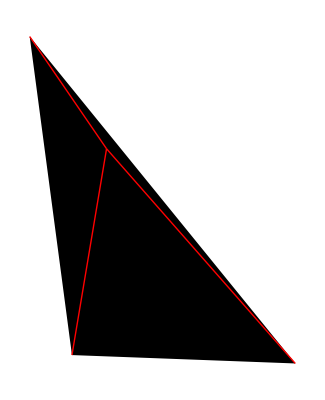

{3,1,2}

containsOrigin[{-340,495},{-153,-910},{835,-947}]

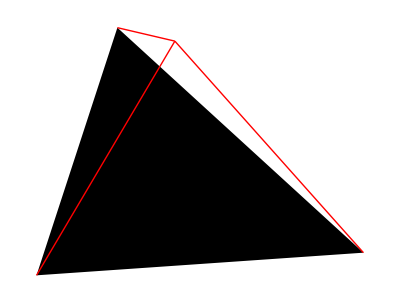

{3,4,1,2}

containsOrigin[{-175,41},{-421,-714},{574,-645}]

```mathematica
p={0,0};
a={-340,495};b={-153,-910};c={835,-947};
Graphics[{Polygon[{a,b,c}],Red,
Line[{p,a}],
Line[{p,b}],
Line[{p,c}]},ImageSize->Tiny]
ConvexHull[{a,b,c,p}]
containsOrigin[a,b,c]
x={-175,41}; y={-421,-714};z={574,-645};
Graphics[{Polygon[{x,y,z}],Red,
Line[{p,x}],
Line[{p,y}],
Line[{p,z}]},ImageSize->Tiny]
ConvexHull[{x,y,z,p}]
containsOrigin[x,y,z]
```

## Problem 103

Let S(A) represent the sum of elements in set A of size n. We shall call it a special sum set if for any two non-empty disjoint subsets, B and C, the following properties are true:

S(B)  S(C); that is, sums of subsets cannot be equal.
If B contains more elements than C then S(B)  S(C).
If S(A) is minimised for a given n, we shall call it an optimum special sum set. The first five optimum special sum sets are given below.

n = 1: {1}
n = 2: {1, 2}
n = 3: {2, 3, 4}
n = 4: {3, 5, 6, 7}
n = 5: {6, 9, 11, 12, 13}

It seems that for a given optimum set, A = {a1, a2, ... , an}, the next optimum set is of the form B = {b, a1+b, a2+b, ... ,an+b}, where b is the "middle" element on the previous row.

By applying this "rule" we would expect the optimum set for n = 6 to be A = {11, 17, 20, 22, 23, 24}, with S(A) = 117. However, this is not the optimum set, as we have merely applied an algorithm to provide a near optimum set. The optimum set for n = 6 is A = {11, 18, 19, 20, 22, 25}, with S(A) = 115 and corresponding set string: 111819202225.

Given that A is an optimum special sum set for n = 7, find its set string.

NOTE: This problem is related to problems 105 and 106.

Problem 104

The Fibonacci sequence is defined by the recurrence relation:

Fn = Fn1 + Fn2, where F1 = 1 and F2 = 1.
It turns out that F541, which contains 113 digits, is the first Fibonacci number for which the last nine digits are 1-9 pandigital (contain all the digits 1 to 9, but not necessarily in order). And F2749, which contains 575 digits, is the first Fibonacci number for which the first nine digits are 1-9 pandigital.

Given that Fk is the first Fibonacci number for which the first nine digits AND the last nine digits are 1-9 pandigital, find k.

Problem 105

Let S(A) represent the sum of elements in set A of size n. We shall call it a special sum set if for any two non-empty disjoint subsets, B and C, the following properties are true:

S(B)  S(C); that is, sums of subsets cannot be equal.
If B contains more elements than C then S(B)  S(C).
For example, {81, 88, 75, 42, 87, 84, 86, 65} is not a special sum set because 65 + 87 + 88 = 75 + 81 + 84, whereas {157, 150, 164, 119, 79, 159, 161, 139, 158} satisfies both rules for all possible subset pair combinations and S(A) = 1286.

Using sets.txt (right click and "Save Link/Target As..."), a 4K text file with one-hundred sets containing seven to twelve elements (the two examples given above are the first two sets in the file), identify all the special sum sets, A1, A2, ..., Ak, and find the value of S(A1) + S(A2) + ... + S(Ak).

NOTE: This problem is related to problems 103 and 106.

Problem 106

Let S(A) represent the sum of elements in set A of size n. We shall call it a special sum set if for any two non-empty disjoint subsets, B and C, the following properties are true:

S(B)  S(C); that is, sums of subsets cannot be equal.
If B contains more elements than C then S(B)  S(C).
For this problem we shall assume that a given set contains n strictly increasing elements and it already satisfies the second rule.

Surprisingly, out of the 25 possible subset pairs that can be obtained from a set for which n = 4, only 1 of these pairs need to be tested for equality (first rule). Similarly, when n = 7, only 70 out of the 966 subset pairs need to be tested.

For n = 12, how many of the 261625 subset pairs that can be obtained need to be tested for equality?

NOTE: This problem is related to problems 103 and 105.

Problem 107

The following undirected network consists of seven vertices and twelve edges with a total weight of 243.


The same network can be represented by the matrix below.

    	A	B	C	D	E	F	G
A	-	16	12	21	-	-	-
B	16	-	-	17	20	-	-
C	12	-	-	28	-	31	-
D	21	17	28	-	18	19	23
E	-	20	-	18	-	-	11
F	-	-	31	19	-	-	27
G	-	-	-	23	11	27	-
However, it is possible to optimise the network by removing some edges and still ensure that all points on the network remain connected. The network which achieves the maximum saving is shown below. It has a weight of 93, representing a saving of 243  93 = 150 from the original network.


Using network.txt (right click and 'Save Link/Target As...'), a 6K text file containing a network with forty vertices, and given in matrix form, find the maximum saving which can be achieved by removing redundant edges whilst ensuring that the network remains connected.

## Problem 108

In the following equation x, y, and n are positive integers.

1/x+1/y=1/n

For n = 4 there are exactly three distinct solutions:

1/5+1/20=1/4
1/6+1/12=1/4
1/8+1/8=1/4

What is the least value of n for which the number of distinct solutions exceeds one-thousand?

NOTE: This problem is an easier version of problem 110; it is strongly advised that you solve this one first.

```mathematica
ClearAll[x,y,n,f,g];
g[m_]:=g[m]=Block[{x,y,n},Length@Solve[1/x+1/y==1/n&&x>0&&y>0&&x≥y/.n->m,{x,y},Integers]]
g[4]==3
```

True

```mathematica
Monitor[Catch[Do[If[g[m]>1000,Throw[m]],{m,2,277200,2}]],m]//Timing
```

$Aborted

## Problem 109

In the game of darts a player throws three darts at a target board which is split into twenty equal sized sections numbered one to twenty.


The score of a dart is determined by the number of the region that the dart lands in. A dart landing outside the red/green outer ring scores zero. The black and cream regions inside this ring represent single scores. However, the red/green outer ring and middle ring score double and treble scores respectively.

At the centre of the board are two concentric circles called the bull region, or bulls-eye. The outer bull is worth 25 points and the inner bull is a double, worth 50 points.

There are many variations of rules but in the most popular game the players will begin with a score 301 or 501 and the first player to reduce their running total to zero is a winner. However, it is normal to play a "doubles out" system, which means that the player must land a double (including the double bulls-eye at the centre of the board) on their final dart to win; any other dart that would reduce their running total to one or lower means the score for that set of three darts is "bust".

When a player is able to finish on their current score it is called a "checkout" and the highest checkout is 170: T20 T20 D25 (two treble 20s and double bull).

There are exactly eleven distinct ways to checkout on a score of 6:


D3	
 	
 
D1	D2	 
S2	D2	 
D2	D1	 
S4	D1	 
S1	S1	D2
S1	T1	D1
S1	S3	D1
D1	D1	D1
D1	S2	D1
S2	S2	D1
Note that D1 D2 is considered different to D2 D1 as they finish on different doubles. However, the combination S1 T1 D1 is considered the same as T1 S1 D1.

In addition we shall not include misses in considering combinations; for example, D3 is the same as 0 D3 and 0 0 D3.

Incredibly there are 42336 distinct ways of checking out in total.

How many distinct ways can a player checkout with a score less than 100?

Problem 110

In the following equation x, y, and n are positive integers.

1

x
+	
1

y
=	
1

n
It can be verified that when n = 1260 there are 113 distinct solutions and this is the least value of n for which the total number of distinct solutions exceeds one hundred.

What is the least value of n for which the number of distinct solutions exceeds four million?

NOTE: This problem is a much more difficult version of problem 108 and as it is well beyond the limitations of a brute force approach it requires a clever implementation.

Problem 111

Considering 4-digit primes containing repeated digits it is clear that they cannot all be the same: 1111 is divisible by 11, 2222 is divisible by 22, and so on. But there are nine 4-digit primes containing three ones:

1117, 1151, 1171, 1181, 1511, 1811, 2111, 4111, 8111

We shall say that M(n, d) represents the maximum number of repeated digits for an n-digit prime where d is the repeated digit, N(n, d) represents the number of such primes, and S(n, d) represents the sum of these primes.

So M(4, 1) = 3 is the maximum number of repeated digits for a 4-digit prime where one is the repeated digit, there are N(4, 1) = 9 such primes, and the sum of these primes is S(4, 1) = 22275. It turns out that for d = 0, it is only possible to have M(4, 0) = 2 repeated digits, but there are N(4, 0) = 13 such cases.

In the same way we obtain the following results for 4-digit primes.

Digit, d	M(4, d)	N(4, d)	S(4, d)
0	2	13	67061
1	3	9	22275
2	3	1	2221
3	3	12	46214
4	3	2	8888
5	3	1	5557
6	3	1	6661
7	3	9	57863
8	3	1	8887
9	3	7	48073
For d = 0 to 9, the sum of all S(4, d) is 273700.

Find the sum of all S(10, d).

## Problem 112 (done)

Working from left-to-right if no digit is exceeded by the digit to its left it is called an increasing number; for example, 134468.

Similarly if no digit is exceeded by the digit to its right it is called a decreasing number; for example, 66420.

We shall call a positive integer that is neither increasing nor decreasing a "bouncy" number; for example, 155349.

Clearly there cannot be any bouncy numbers below one-hundred, but just over half of the numbers below one-thousand (525) are bouncy. In fact, the least number for which the proportion of bouncy numbers first reaches 50% is 538.

Surprisingly, bouncy numbers become more and more common and by the time we reach 21780 the proportion of bouncy numbers is equal to 90%.

Find the least number for which the proportion of bouncy numbers is exactly 99%.

```mathematica
bouncy[n_]:=Block[{a=IntegerDigits[n]},
Block[{s=Sort@a},
a≠s&&a≠Reverse@s]]
bounceUntil[p_]:=Block[{c=0,n=99},While[c/n<p,n++;If[bouncy[n],c++]];n]
bounceUntil[1/2]==538&&bounceUntil[9/10]==21780
```

True

```mathematica
bounceUntil[99/100]//Timing
```

{35.9183,1587000}

## Problem 113

Working from left-to-right if no digit is exceeded by the digit to its left it is called an increasing number; for example, 134468.

Similarly if no digit is exceeded by the digit to its right it is called a decreasing number; for example, 66420.

We shall call a positive integer that is neither increasing nor decreasing a "bouncy" number; for example, 155349.

As n increases, the proportion of bouncy numbers below n increases such that there are only 12951 numbers below one-million that are not bouncy and only 277032 non-bouncy numbers below 1010.

How many numbers below a googol (10100) are not bouncy?

Problem 114

A row measuring seven units in length has red blocks with a minimum length of three units placed on it, such that any two red blocks (which are allowed to be different lengths) are separated by at least one black square. There are exactly seventeen ways of doing this.

						
				
				
				
				
				
		
			
			
			
			
		
		
		
	
	

 
How many ways can a row measuring fifty units in length be filled?

NOTE: Although the example above does not lend itself to the possibility, in general it is permitted to mix block sizes. For example, on a row measuring eight units in length you could use red (3), black (1), and red (4).

Problem 115

NOTE: This is a more difficult version of problem 114.

A row measuring n units in length has red blocks with a minimum length of m units placed on it, such that any two red blocks (which are allowed to be different lengths) are separated by at least one black square.

Let the fill-count function, F(m, n), represent the number of ways that a row can be filled.

For example, F(3, 29) = 673135 and F(3, 30) = 1089155.

That is, for m = 3, it can be seen that n = 30 is the smallest value for which the fill-count function first exceeds one million.

In the same way, for m = 10, it can be verified that F(10, 56) = 880711 and F(10, 57) = 1148904, so n = 57 is the least value for which the fill-count function first exceeds one million.

For m = 50, find the least value of n for which the fill-count function first exceeds one million.

Problem 116

A row of five black square tiles is to have a number of its tiles replaced with coloured oblong tiles chosen from red (length two), green (length three), or blue (length four).

If red tiles are chosen there are exactly seven ways this can be done.

			
			
			
			
		
		
		
 
If green tiles are chosen there are three ways.

		
		
		
 
And if blue tiles are chosen there are two ways.

	
	
Assuming that colours cannot be mixed there are 7 + 3 + 2 = 12 ways of replacing the black tiles in a row measuring five units in length.

How many different ways can the black tiles in a row measuring fifty units in length be replaced if colours cannot be mixed and at least one coloured tile must be used?

NOTE: This is related to problem 117.

Problem 117

Using a combination of black square tiles and oblong tiles chosen from: red tiles measuring two units, green tiles measuring three units, and blue tiles measuring four units, it is possible to tile a row measuring five units in length in exactly fifteen different ways.

				
			
			
			
			
		
		
		
		
		
		
	
	
	
	
 
How many ways can a row measuring fifty units in length be tiled?

NOTE: This is related to problem 116.

## Problem 118

Using all of the digits 1 through 9 and concatenating them freely to form decimal integers, different sets can be formed. Interestingly with the set {2,5,47,89,631}, all of the elements belonging to it are prime.

How many distinct sets containing each of the digits one through nine exactly once contain only prime elements?

## Problem 119 (done)

The number 512 is interesting because it is equal to the sum of its digits raised to some power: 5 + 1 + 2 = 8, and 8^3 = 512. Another example of a number with this property is 614656 = 28^4.

We shall define an to be the nth term of this sequence and insist that a number must contain at least two digits to have a sum.

You are given that a2 = 512 and a10 = 614656.

Find a30.

```mathematica
ClearAll[f];
f[n_]:=Block[{m=Total[IntegerDigits[n]]},m≠1&&IntegerQ[Log[m,n]]]
f[512]
Select[Drop[Union@@Table[n^m,{n,Range[9 11]},{m,Range[8]}],9],f]⟦30⟧//Timing
```

True

{0.015975,248155780267521}

## Problem 120

Let r be the remainder when (a1)n + (a+1)n is divided by a2.

For example, if a = 7 and n = 3, then r = 42: 63 + 83 = 728  42 mod 49. And as n varies, so too will r, but for a = 7 it turns out that rmax = 42.

For 3  a  1000, find  rmax.

## Problem 121

A bag contains one red disc and one blue disc. In a game of chance a player takes a disc at random and its colour is noted. After each turn the disc is returned to the bag, an extra red disc is added, and another disc is taken at random.

The player pays £1 to play and wins if they have taken more blue discs than red discs at the end of the game.

If the game is played for four turns, the probability of a player winning is exactly 11/120, and so the maximum prize fund the banker should allocate for winning in this game would be £10 before they would expect to incur a loss. Note that any payout will be a whole number of pounds and also includes the original £1 paid to play the game, so in the example given the player actually wins £9.

Find the maximum prize fund that should be allocated to a single game in which fifteen turns are played.

## Problem 122

The most naive way of computing n15 requires fourteen multiplications:

n  n  ...  n = n15

But using a "binary" method you can compute it in six multiplications:

n  n = n2
n2  n2 = n4
n4  n4 = n8
n8  n4 = n12
n12  n2 = n14
n14  n = n15

However it is yet possible to compute it in only five multiplications:

n  n = n2
n2  n = n3
n3  n3 = n6
n6  n6 = n12
n12  n3 = n15

We shall define m(k) to be the minimum number of multiplications to compute nk; for example m(15) = 5.

For 1  k  200, find  m(k).

## Problem 123 (done)

Let pn be the nth prime: 2, 3, 5, 7, 11, ..., and let r be the remainder when (pn1)n + (pn+1)n is divided by pn2.

For example, when n = 3, p3 = 5, and 43 + 63 = 280  5 mod 25.

The least value of n for which the remainder first exceeds 109 is 7037.

Find the least value of n for which the remainder first exceeds 1010.

```mathematica
f[n_]:=Block[{p=Prime[n]},Mod[(p-1)^n+(p+1)^n,p^2]]
Select[Range[1,100000,2],f[#]>10^10&,1]//Timing
```

{18.3569,{21035}}

## Problem 124 (done)

The radical of n, rad(n), is the product of distinct prime factors of n. For example, 504 = 23  32  7, so rad(504) = 2  3  7 = 42.

If we calculate rad(n) for 1 <= n <= 10, then sort them on rad(n), and sorting on n if the radical values are equal, we get:

[...blahblah...]

Let E(k) be the kth element in the sorted n column; for example, E(4) = 8 and E(6) = 9.

If rad(n) is sorted for 1≤n≤100000, find E(10000).

```mathematica
rad[n_]:=Times@@(First /@FactorInteger[n])
rad[504]==42
```

True

```mathematica
Sort[Table[{rad[n],n},{n,100000}]][[10000]]//Timing
```

{1.5674,{1947,21417}}

## Problem 125 (done)

The palindromic number 595 is interesting because it can be written as the sum of consecutive squares: 62 + 72 + 82 + 92 + 102 + 112 + 122.

There are exactly eleven palindromes below one-thousand that can be written as consecutive square sums, and the sum of these palindromes is 4164. Note that 1 = 02 + 12 has not been included as this problem is concerned with the squares of positive integers.

Find the sum of all the numbers less than 108 that are both palindromic and can be written as the sum of consecutive squares.

```mathematica
squares = Table[n^2,{n,√(10^8)}];
palindrome[n_]:=Block[{a=IntegerDigits[n]}, a == Reverse@a]
f[max_]:=Block[{palindromes={},arraySize=Length@squares},
For[index=1,index<arraySize,index++,
Block[{sum=0,a=Take[squares,{index,-1}]},
Do[
sum+=n;
If[sum > max,Break[]];
If[sum≠ n&&palindrome[sum],AppendTo[palindromes,sum]],
{n,a}]]];
palindromes]
Total@DeleteDuplicates@f[10^8]//Timing
```

{9.48769,2906969179}

## Problem 126

The minimum number of cubes to cover every visible face on a cuboid measuring 3 x 2 x 1 is twenty-two.


If we then add a second layer to this solid it would require forty-six cubes to cover every visible face, the third layer would require seventy-eight cubes, and the fourth layer would require one-hundred and eighteen cubes to cover every visible face.

However, the first layer on a cuboid measuring 5 x 1 x 1 also requires twenty-two cubes; similarly the first layer on cuboids measuring 5 x 3 x 1, 7 x 2 x 1, and 11 x 1 x 1 all contain forty-six cubes.

We shall define C(n) to represent the number of cuboids that contain n cubes in one of its layers. So C(22) = 2, C(46) = 4, C(78) = 5, and C(118) = 8.

It turns out that 154 is the least value of n for which C(n) = 10.

Find the least value of n for which C(n) = 1000.

Problem 127

The radical of n, rad(n), is the product of distinct prime factors of n. For example, 504 = 23  32  7, so rad(504) = 2  3  7 = 42.

We shall define the triplet of positive integers (a, b, c) to be an abc-hit if:

GCD(a, b) = GCD(a, c) = GCD(b, c) = 1
a  b
a + b = c
rad(abc)  c
For example, (5, 27, 32) is an abc-hit, because:

GCD(5, 27) = GCD(5, 32) = GCD(27, 32) = 1
5  27
5 + 27 = 32
rad(4320) = 30  32
It turns out that abc-hits are quite rare and there are only thirty-one abc-hits for c  1000, with c = 12523.

Find c for c  120000.

Note: This problem has been changed recently, please check that you are using the right parameters.

Problem 128

A hexagonal tile with number 1 is surrounded by a ring of six hexagonal tiles, starting at "12 o'clock" and numbering the tiles 2 to 7 in an anti-clockwise direction.

New rings are added in the same fashion, with the next rings being numbered 8 to 19, 20 to 37, 38 to 61, and so on. The diagram below shows the first three rings.


By finding the difference between tile n and each its six neighbours we shall define PD(n) to be the number of those differences which are prime.

For example, working clockwise around tile 8 the differences are 12, 29, 11, 6, 1, and 13. So PD(8) = 3.

In the same way, the differences around tile 17 are 1, 17, 16, 1, 11, and 10, hence PD(17) = 2.

It can be shown that the maximum value of PD(n) is 3.

If all of the tiles for which PD(n) = 3 are listed in ascending order to form a sequence, the 10th tile would be 271.

Find the 2000th tile in this sequence.

Problem 129

A number consisting entirely of ones is called a repunit. We shall define R(k) to be a repunit of length k; for example, R(6) = 111111.

Given that n is a positive integer and GCD(n, 10) = 1, it can be shown that there always exists a value, k, for which R(k) is divisible by n, and let A(n) be the least such value of k; for example, A(7) = 6 and A(41) = 5.

The least value of n for which A(n) first exceeds ten is 17.

Find the least value of n for which A(n) first exceeds one-million.

Problem 130

A number consisting entirely of ones is called a repunit. We shall define R(k) to be a repunit of length k; for example, R(6) = 111111.

Given that n is a positive integer and GCD(n, 10) = 1, it can be shown that there always exists a value, k, for which R(k) is divisible by n, and let A(n) be the least such value of k; for example, A(7) = 6 and A(41) = 5.

You are given that for all primes, p  5, that p  1 is divisible by A(p). For example, when p = 41, A(41) = 5, and 40 is divisible by 5.

However, there are rare composite values for which this is also true; the first five examples being 91, 259, 451, 481, and 703.

Find the sum of the first twenty-five composite values of n for which
GCD(n, 10) = 1 and n  1 is divisible by A(n).

Problem 131

There are some prime values, p, for which there exists a positive integer, n, such that the expression n3 + n2p is a perfect cube.

For example, when p = 19, 83 + 8219 = 123.

What is perhaps most surprising is that for each prime with this property the value of n is unique, and there are only four such primes below one-hundred.

How many primes below one million have this remarkable property?

Problem 132

A number consisting entirely of ones is called a repunit. We shall define R(k) to be a repunit of length k.

For example, R(10) = 1111111111 = 11412719091, and the sum of these prime factors is 9414.

Find the sum of the first forty prime factors of R(109).

Problem 133

A number consisting entirely of ones is called a repunit. We shall define R(k) to be a repunit of length k; for example, R(6) = 111111.

Let us consider repunits of the form R(10n).

Although R(10), R(100), or R(1000) are not divisible by 17, R(10000) is divisible by 17. Yet there is no value of n for which R(10n) will divide by 19. In fact, it is remarkable that 11, 17, 41, and 73 are the only four primes below one-hundred that can be a factor of R(10n).

Find the sum of all the primes below one-hundred thousand that will never be a factor of R(10n).

Problem 134

Consider the consecutive primes p1 = 19 and p2 = 23. It can be verified that 1219 is the smallest number such that the last digits are formed by p1 whilst also being divisible by p2.

In fact, with the exception of p1 = 3 and p2 = 5, for every pair of consecutive primes, p2  p1, there exist values of n for which the last digits are formed by p1 and n is divisible by p2. Let S be the smallest of these values of n.

Find  S for every pair of consecutive primes with 5  p1  1000000.

Problem 135

Given the positive integers, x, y, and z, are consecutive terms of an arithmetic progression, the least value of the positive integer, n, for which the equation, x2  y2  z2 = n, has exactly two solutions is n = 27:

342  272  202 = 122  92  62 = 27

It turns out that n = 1155 is the least value which has exactly ten solutions.

How many values of n less than one million have exactly ten distinct solutions?

Problem 136

The positive integers, x, y, and z, are consecutive terms of an arithmetic progression. Given that n is a positive integer, the equation, x2  y2  z2 = n, has exactly one solution when n = 20:

132  102  72 = 20

In fact there are twenty-five values of n below one hundred for which the equation has a unique solution.

How many values of n less than fifty million have exactly one solution?

Problem 137

Consider the infinite polynomial series AF(x) = xF1 + x2F2 + x3F3 + ..., where Fk is the kth term in the Fibonacci sequence: 1, 1, 2, 3, 5, 8, ... ; that is, Fk = Fk1 + Fk2, F1 = 1 and F2 = 1.

For this problem we shall be interested in values of x for which AF(x) is a positive integer.

Surprisingly AF(1/2)	 = 	(1/2).1 + (1/2)2.1 + (1/2)3.2 + (1/2)4.3 + (1/2)5.5 + ...
 	 = 	1/2 + 1/4 + 2/8 + 3/16 + 5/32 + ...
 	 = 	2
The corresponding values of x for the first five natural numbers are shown below.

x	AF(x)
21	1
1/2	2
(132)/3	3
(895)/8	4
(343)/5	5
We shall call AF(x) a golden nugget if x is rational, because they become increasingly rarer; for example, the 10th golden nugget is 74049690.

Find the 15th golden nugget.

Problem 138

Consider the isosceles triangle with base length, b = 16, and legs, L = 17.


By using the Pythagorean theorem it can be seen that the height of the triangle, h = (172  82) = 15, which is one less than the base length.

With b = 272 and L = 305, we get h = 273, which is one more than the base length, and this is the second smallest isosceles triangle with the property that h = b  1.

Find  L for the twelve smallest isosceles triangles for which h = b  1 and b, L are positive integers.

Problem 139

Let (a, b, c) represent the three sides of a right angle triangle with integral length sides. It is possible to place four such triangles together to form a square with length c.

For example, (3, 4, 5) triangles can be placed together to form a 5 by 5 square with a 1 by 1 hole in the middle and it can be seen that the 5 by 5 square can be tiled with twenty-five 1 by 1 squares.


However, if (5, 12, 13) triangles were used then the hole would measure 7 by 7 and these could not be used to tile the 13 by 13 square.

Given that the perimeter of the right triangle is less than one-hundred million, how many Pythagorean triangles would allow such a tiling to take place?

Problem 140

Consider the infinite polynomial series AG(x) = xG1 + x2G2 + x3G3 + ..., where Gk is the kth term of the second order recurrence relation Gk = Gk1 + Gk2, G1 = 1 and G2 = 4; that is, 1, 4, 5, 9, 14, 23, ... .

For this problem we shall be concerned with values of x for which AG(x) is a positive integer.

The corresponding values of x for the first five natural numbers are shown below.

x	AG(x)
(51)/4	1
2/5	2
(222)/6	3
(1375)/14	4
1/2	5
We shall call AG(x) a golden nugget if x is rational, because they become increasingly rarer; for example, the 20th golden nugget is 211345365.

Find the sum of the first thirty golden nuggets.

Problem 141

A positive integer, n, is divided by d and the quotient and remainder are q and r respectively. In addition d, q, and r are consecutive positive integer terms in a geometric sequence, but not necessarily in that order.

For example, 58 divided by 6 has quotient 9 and remainder 4. It can also be seen that 4, 6, 9 are consecutive terms in a geometric sequence (common ratio 3/2).
We will call such numbers, n, progressive.

Some progressive numbers, such as 9 and 10404 = 1022, happen to also be perfect squares.
The sum of all progressive perfect squares below one hundred thousand is 124657.

Find the sum of all progressive perfect squares below one trillion (1012).

Problem 142

Find the smallest x + y + z with integers x  y  z  0 such that x + y, x  y, x + z, x  z, y + z, y  z are all perfect squares.

Problem 143

Let ABC be a triangle with all interior angles being less than 120 degrees. Let X be any point inside the triangle and let XA = p, XB = q, and XC = r.

Fermat challenged Torricelli to find the position of X such that p + q + r was minimised.

Torricelli was able to prove that if equilateral triangles AOB, BNC and AMC are constructed on each side of triangle ABC, the circumscribed circles of AOB, BNC, and AMC will intersect at a single point, T, inside the triangle. Moreover he proved that T, called the Torricelli/Fermat point, minimises p + q + r. Even more remarkable, it can be shown that when the sum is minimised, AN = BM = CO = p + q + r and that AN, BM and CO also intersect at T.


If the sum is minimised and a, b, c, p, q and r are all positive integers we shall call triangle ABC a Torricelli triangle. For example, a = 399, b = 455, c = 511 is an example of a Torricelli triangle, with p + q + r = 784.

Find the sum of all distinct values of p + q + r  120000 for Torricelli triangles.

Note: This problem has been changed recently, please check that you are using the right parameters.

Problem 144

In laser physics, a "white cell" is a mirror system that acts as a delay line for the laser beam. The beam enters the cell, bounces around on the mirrors, and eventually works its way back out.

The specific white cell we will be considering is an ellipse with the equation 4x2 + y2 = 100

The section corresponding to 0.01  x  +0.01 at the top is missing, allowing the light to enter and exit through the hole.


The light beam in this problem starts at the point (0.0,10.1) just outside the white cell, and the beam first impacts the mirror at (1.4,-9.6).

Each time the laser beam hits the surface of the ellipse, it follows the usual law of reflection "angle of incidence equals angle of reflection." That is, both the incident and reflected beams make the same angle with the normal line at the point of incidence.

In the figure on the left, the red line shows the first two points of contact between the laser beam and the wall of the white cell; the blue line shows the line tangent to the ellipse at the point of incidence of the first bounce.

The slope m of the tangent line at any point (x,y) of the given ellipse is: m = 4x/y

The normal line is perpendicular to this tangent line at the point of incidence.

The animation on the right shows the first 10 reflections of the beam.

How many times does the beam hit the internal surface of the white cell before exiting?

## Problem 145

Some positive integers n have the property that the sum [ n + reverse(n) ] consists entirely of odd (decimal) digits. For instance, 36 + 63 = 99 and 409 + 904 = 1313. We will call such numbers reversible; so 36, 63, 409, and 904 are reversible. Leading zeroes are not allowed in either n or reverse(n).

There are 120 reversible numbers below one-thousand.

How many reversible numbers are there below one-billion (109)?

## Problem 146

The smallest positive integer n for which the numbers n2+1, n2+3, n2+7, n2+9, n2+13, and n2+27 are consecutive primes is 10. The sum of all such integers n below one-million is 1242490.

What is the sum of all such integers n below 150 million?

Problem 147

In a 3x2 cross-hatched grid, a total of 37 different rectangles could be situated within that grid as indicated in the sketch.


There are 5 grids smaller than 3x2, vertical and horizontal dimensions being important, i.e. 1x1, 2x1, 3x1, 1x2 and 2x2. If each of them is cross-hatched, the following number of different rectangles could be situated within those smaller grids:

1x1: 1 
2x1: 4 
3x1: 8 
1x2: 4 
2x2: 18

Adding those to the 37 of the 3x2 grid, a total of 72 different rectangles could be situated within 3x2 and smaller grids.

How many different rectangles could be situated within 47x43 and smaller grids?

Problem 148

We can easily verify that none of the entries in the first seven rows of Pascal's triangle are divisible by 7:

 	 	 	 	 	 	 1
 	 	 	 	 	 1	 	 1
 	 	 	 	 1	 	 2	 	 1
 	 	 	 1	 	 3	 	 3	 	 1
 	 	 1	 	 4	 	 6	 	 4	 	 1
 	 1	 	 5	 	10	 	10	 	 5	 	 1
1	 	 6	 	15	 	20	 	15	 	 6	 	 1
However, if we check the first one hundred rows, we will find that only 2361 of the 5050 entries are not divisible by 7.

Find the number of entries which are not divisible by 7 in the first one billion (109) rows of Pascal's triangle.

Problem 149

Looking at the table below, it is easy to verify that the maximum possible sum of adjacent numbers in any direction (horizontal, vertical, diagonal or anti-diagonal) is 16 (= 8 + 7 + 1).

2	5	3	2
9	6	5	1
3	2	7	3
1	8	4	  8
Now, let us repeat the search, but on a much larger scale:

First, generate four million pseudo-random numbers using a specific form of what is known as a "Lagged Fibonacci Generator":

For 1  k  55, sk = [100003  200003k + 300007k3] (modulo 1000000)  500000.
For 56  k  4000000, sk = [sk24 + sk55 + 1000000] (modulo 1000000)  500000.

Thus, s10 = 393027 and s100 = 86613.

The terms of s are then arranged in a 20002000 table, using the first 2000 numbers to fill the first row (sequentially), the next 2000 numbers to fill the second row, and so on.

Finally, find the greatest sum of (any number of) adjacent entries in any direction (horizontal, vertical, diagonal or anti-diagonal).

Problem 150

In a triangular array of positive and negative integers, we wish to find a sub-triangle such that the sum of the numbers it contains is the smallest possible.

In the example below, it can be easily verified that the marked triangle satisfies this condition having a sum of 42.


We wish to make such a triangular array with one thousand rows, so we generate 500500 pseudo-random numbers sk in the range 219, using a type of random number generator (known as a Linear Congruential Generator) as follows:

t := 0 
for k = 1 up to k = 500500: 
    t := (615949*t + 797807) modulo 220 
    sk := t219

Thus: s1 = 273519, s2 = 153582, s3 = 450905 etc

Our triangular array is then formed using the pseudo-random numbers thus:

s1 
s2  s3 
s4  s5  s6  
s7  s8  s9  s10 
...
Sub-triangles can start at any element of the array and extend down as far as we like (taking-in the two elements directly below it from the next row, the three elements directly below from the row after that, and so on). 
The "sum of a sub-triangle" is defined as the sum of all the elements it contains. 
Find the smallest possible sub-triangle sum.

Problem 151

A printing shop runs 16 batches (jobs) every week and each batch requires a sheet of special colour-proofing paper of size A5.

Every Monday morning, the foreman opens a new envelope, containing a large sheet of the special paper with size A1.

He proceeds to cut it in half, thus getting two sheets of size A2. Then he cuts one of them in half to get two sheets of size A3 and so on until he obtains the A5-size sheet needed for the first batch of the week.

All the unused sheets are placed back in the envelope.


At the beginning of each subsequent batch, he takes from the envelope one sheet of paper at random. If it is of size A5, he uses it. If it is larger, he repeats the 'cut-in-half' procedure until he has what he needs and any remaining sheets are always placed back in the envelope.

Excluding the first and last batch of the week, find the expected number of times (during each week) that the foreman finds a single sheet of paper in the envelope.

Give your answer rounded to six decimal places using the format x.xxxxxx .

Problem 152

There are several ways to write the number 1/2 as a sum of inverse squares using distinct integers.

For instance, the numbers {2,3,4,5,7,12,15,20,28,35} can be used:



In fact, only using integers between 2 and 45 inclusive, there are exactly three ways to do it, the remaining two being: {2,3,4,6,7,9,10,20,28,35,36,45} and {2,3,4,6,7,9,12,15,28,30,35,36,45}.

How many ways are there to write the number 1/2 as a sum of inverse squares using distinct integers between 2 and 80 inclusive?

Problem 153

As we all know the equation x2=-1 has no solutions for real x. 
If we however introduce the imaginary number i this equation has two solutions: x=i and x=-i. 
If we go a step further the equation (x-3)2=-4 has two complex solutions: x=3+2i and x=3-2i. 
x=3+2i and x=3-2i are called each others' complex conjugate. 
Numbers of the form a+bi are called complex numbers. 
In general a+bi and abi are each other's complex conjugate.

A Gaussian Integer is a complex number a+bi such that both a and b are integers. 
The regular integers are also Gaussian integers (with b=0). 
To distinguish them from Gaussian integers with b  0 we call such integers "rational integers." 
A Gaussian integer is called a divisor of a rational integer n if the result is also a Gaussian integer. 
If for example we divide 5 by 1+2i we can simplify  in the following manner: 
Multiply numerator and denominator by the complex conjugate of 1+2i: 12i. 
The result is  . 
So 1+2i is a divisor of 5. 
Note that 1+i is not a divisor of 5 because . 
Note also that if the Gaussian Integer (a+bi) is a divisor of a rational integer n, then its complex conjugate (abi) is also a divisor of n.

In fact, 5 has six divisors such that the real part is positive: {1, 1 + 2i, 1  2i, 2 + i, 2  i, 5}. 
The following is a table of all of the divisors for the first five positive rational integers:

n	 Gaussian integer divisors
with positive real part	Sum s(n) of 
these divisors
1	1	1
2	1, 1+i, 1-i, 2	5
3	1, 3	4
4	1, 1+i, 1-i, 2, 2+2i, 2-2i,4	13
5	1, 1+2i, 1-2i, 2+i, 2-i, 5	12
For divisors with positive real parts, then, we have: .

For 1  n  105,  s(n)=17924657155.

What is  s(n) for 1  n  108?

Problem 154

A triangular pyramid is constructed using spherical balls so that each ball rests on exactly three balls of the next lower level.


Then, we calculate the number of paths leading from the apex to each position:

A path starts at the apex and progresses downwards to any of the three spheres directly below the current position.

Consequently, the number of paths to reach a certain position is the sum of the numbers immediately above it (depending on the position, there are up to three numbers above it).

The result is Pascal's pyramid and the numbers at each level n are the coefficients of the trinomial expansion (x + y + z)n.

How many coefficients in the expansion of (x + y + z)200000 are multiples of 1012?

Problem 155

An electric circuit uses exclusively identical capacitors of the same value C. 
The capacitors can be connected in series or in parallel to form sub-units, which can then be connected in series or in parallel with other capacitors or other sub-units to form larger sub-units, and so on up to a final circuit.

Using this simple procedure and up to n identical capacitors, we can make circuits having a range of different total capacitances. For example, using up to n=3 capacitors of 60 F each, we can obtain the following 7 distinct total capacitance values:


If we denote by D(n) the number of distinct total capacitance values we can obtain when using up to n equal-valued capacitors and the simple procedure described above, we have: D(1)=1, D(2)=3, D(3)=7 ...

Find D(18).

Reminder : When connecting capacitors C1, C2 etc in parallel, the total capacitance is CT = C1 + C2 +..., 
whereas when connecting them in series, the overall capacitance is given by: 

Problem 156

Starting from zero the natural numbers are written down in base 10 like this: 
0 1 2 3 4 5 6 7 8 9 10 11 12....

Consider the digit d=1. After we write down each number n, we will update the number of ones that have occurred and call this number f(n,1). The first values for f(n,1), then, are as follows:

n	f(n,1)
0	0
1	1
2	1
3	1
4	1
5	1
6	1
7	1
8	1
9	1
10	2
11	4
12	5
Note that f(n,1) never equals 3. 
So the first two solutions of the equation f(n,1)=n are n=0 and n=1. The next solution is n=199981.

In the same manner the function f(n,d) gives the total number of digits d that have been written down after the number n has been written. 
In fact, for every digit d  0, 0 is the first solution of the equation f(n,d)=n.

Let s(d) be the sum of all the solutions for which f(n,d)=n. 
You are given that s(1)=22786974071.

Find   s(d) for 1  d  9.

Note: if, for some n, f(n,d)=n for more than one value of d this value of n is counted again for every value of d for which f(n,d)=n.

Problem 157

Consider the diophantine equation 1/a+1/b= p/10n with a, b, p, n positive integers and a  b.
For n=1 this equation has 20 solutions that are listed below:

1/1+1/1=20/10	1/1+1/2=15/10	1/1+1/5=12/10	1/1+1/10=11/10	1/2+1/2=10/10
1/2+1/5=7/10	1/2+1/10=6/10	1/3+1/6=5/10	1/3+1/15=4/10	1/4+1/4=5/10
1/4+1/20=3/10	1/5+1/5=4/10	1/5+1/10=3/10	1/6+1/30=2/10	1/10+1/10=2/10
1/11+1/110=1/10	1/12+1/60=1/10	1/14+1/35=1/10	1/15+1/30=1/10	1/20+1/20=1/10
How many solutions has this equation for 1  n  9?

Problem 158

Taking three different letters from the 26 letters of the alphabet, character strings of length three can be formed.
Examples are 'abc', 'hat' and 'zyx'.
When we study these three examples we see that for 'abc' two characters come lexicographically after its neighbour to the left.
For 'hat' there is exactly one character that comes lexicographically after its neighbour to the left. For 'zyx' there are zero characters that come lexicographically after its neighbour to the left.
In all there are 10400 strings of length 3 for which exactly one character comes lexicographically after its neighbour to the left.

We now consider strings of n  26 different characters from the alphabet.
For every n, p(n) is the number of strings of length n for which exactly one character comes lexicographically after its neighbour to the left.

What is the maximum value of p(n)?

Problem 159

A composite number can be factored many different ways. For instance, not including multiplication by one, 24 can be factored in 7 distinct ways:

24 = 2x2x2x3
24 = 2x3x4
24 = 2x2x6
24 = 4x6
24 = 3x8
24 = 2x12
24 = 24
Recall that the digital root of a number, in base 10, is found by adding together the digits of that number, and repeating that process until a number is arrived at that is less than 10. Thus the digital root of 467 is 8.

We shall call a Digital Root Sum (DRS) the sum of the digital roots of the individual factors of our number.
The chart below demonstrates all of the DRS values for 24.

Factorisation	Digital Root Sum
2x2x2x3
9
2x3x4
9
2x2x6
10
4x6
10
3x8
11
2x12
5
24
6
The maximum Digital Root Sum of 24 is 11.
The function mdrs(n) gives the maximum Digital Root Sum of n. So mdrs(24)=11.
Find mdrs(n) for 1  n  1,000,000.

Problem 160

For any N, let f(N) be the last five digits before the trailing zeroes in N!.
For example,

9! = 362880 so f(9)=36288
10! = 3628800 so f(10)=36288
20! = 2432902008176640000 so f(20)=17664

Find f(1,000,000,000,000)

Problem 161

A triomino is a shape consisting of three squares joined via the edges. There are two basic forms:



If all possible orientations are taken into account there are six:



Any n by m grid for which nxm is divisible by 3 can be tiled with triominoes.
If we consider tilings that can be obtained by reflection or rotation from another tiling as different there are 41 ways a 2 by 9 grid can be tiled with triominoes:



In how many ways can a 9 by 12 grid be tiled in this way by triominoes?

Problem 162

In the hexadecimal number system numbers are represented using 16 different digits:

0,1,2,3,4,5,6,7,8,9,A,B,C,D,E,F
The hexadecimal number AF when written in the decimal number system equals 10x16+15=175.

In the 3-digit hexadecimal numbers 10A, 1A0, A10, and A01 the digits 0,1 and A are all present.
Like numbers written in base ten we write hexadecimal numbers without leading zeroes.

How many hexadecimal numbers containing at most sixteen hexadecimal digits exist with all of the digits 0,1, and A present at least once?
Give your answer as a hexadecimal number.

(A,B,C,D,E and F in upper case, without any leading or trailing code that marks the number as hexadecimal and without leading zeroes , e.g. 1A3F and not: 1a3f and not 0x1a3f and not $1A3F and not #1A3F and not 0000001A3F)

Problem 163

Consider an equilateral triangle in which straight lines are drawn from each vertex to the middle of the opposite side, such as in the size 1 triangle in the sketch below.


Sixteen triangles of either different shape or size or orientation or location can now be observed in that triangle. Using size 1 triangles as building blocks, larger triangles can be formed, such as the size 2 triangle in the above sketch. One-hundred and four triangles of either different shape or size or orientation or location can now be observed in that size 2 triangle.

It can be observed that the size 2 triangle contains 4 size 1 triangle building blocks. A size 3 triangle would contain 9 size 1 triangle building blocks and a size n triangle would thus contain n2 size 1 triangle building blocks.

If we denote T(n) as the number of triangles present in a triangle of size n, then

T(1) = 16
T(2) = 104

Find T(36).

Problem 164

How many 20 digit numbers n (without any leading zero) exist such that no three consecutive digits of n have a sum greater than 9?

Problem 165

A segment is uniquely defined by its two endpoints.
By considering two line segments in plane geometry there are three possibilities:
the segments have zero points, one point, or infinitely many points in common.

Moreover when two segments have exactly one point in common it might be the case that that common point is an endpoint of either one of the segments or of both. If a common point of two segments is not an endpoint of either of the segments it is an interior point of both segments.
We will call a common point T of two segments L1 and L2 a true intersection point of L1 and L2 if T is the only common point of L1 and L2 and T is an interior point of both segments.

Consider the three segments L1, L2, and L3:

L1: (27, 44) to (12, 32)
L2: (46, 53) to (17, 62)
L3: (46, 70) to (22, 40)

It can be verified that line segments L2 and L3 have a true intersection point. We note that as the one of the end points of L3: (22,40) lies on L1 this is not considered to be a true point of intersection. L1 and L2 have no common point. So among the three line segments, we find one true intersection point.

Now let us do the same for 5000 line segments. To this end, we generate 20000 numbers using the so-called "Blum Blum Shub" pseudo-random number generator.

s0 = 290797

sn+1 = snsn (modulo 50515093)

tn = sn (modulo 500)

To create each line segment, we use four consecutive numbers tn. That is, the first line segment is given by:

(t1, t2) to (t3, t4)

The first four numbers computed according to the above generator should be: 27, 144, 12 and 232. The first segment would thus be (27,144) to (12,232).

How many distinct true intersection points are found among the 5000 line segments?

Problem 166

A 4x4 grid is filled with digits d, 0  d  9.

It can be seen that in the grid

6 3 3 0
5 0 4 3
0 7 1 4
1 2 4 5

the sum of each row and each column has the value 12. Moreover the sum of each diagonal is also 12.

In how many ways can you fill a 4x4 grid with the digits d, 0  d  9 so that each row, each column, and both diagonals have the same sum?

Problem 167

For two positive integers a and b, the Ulam sequence U(a,b) is defined by U(a,b)1 = a, U(a,b)2 = b and for k > 2, U(a,b)k is the smallest integer greater than U(a,b)(k-1) which can be written in exactly one way as the sum of two distinct previous members of U(a,b).

For example, the sequence U(1,2) begins with
1, 2, 3 = 1 + 2, 4 = 1 + 3, 6 = 2 + 4, 8 = 2 + 6, 11 = 3 + 8;
5 does not belong to it because 5 = 1 + 4 = 2 + 3 has two representations as the sum of two previous members, likewise 7 = 1 + 6 = 3 + 4.

Find U(2,2n+1)k for 2  n 10, where k = 1011.

Problem 168

Consider the number 142857. We can right-rotate this number by moving the last digit (7) to the front of it, giving us 714285.
It can be verified that 714285=5142857.
This demonstrates an unusual property of 142857: it is a divisor of its right-rotation.

Find the last 5 digits of the sum of all integers n, 10  n  10100, that have this property.

Problem 169

Define f(0)=1 and f(n) to be the number of different ways n can be expressed as a sum of integer powers of 2 using each power no more than twice.

For example, f(10)=5 since there are five different ways to express 10:

1 + 1 + 8
1 + 1 + 4 + 4
1 + 1 + 2 + 2 + 4
2 + 4 + 4
2 + 8

What is f(1025)?

Problem 170

Take the number 6 and multiply it by each of 1273 and 9854:

6  1273 = 7638
6  9854 = 59124

By concatenating these products we get the 1 to 9 pandigital 763859124. We will call 763859124 the "concatenated product of 6 and (1273,9854)". Notice too, that the concatenation of the input numbers, 612739854, is also 1 to 9 pandigital.

The same can be done for 0 to 9 pandigital numbers.

What is the largest 0 to 9 pandigital 10-digit concatenated product of an integer with two or more other integers, such that the concatenation of the input numbers is also a 0 to 9 pandigital 10-digit number?

Problem 171

For a positive integer n, let f(n) be the sum of the squares of the digits (in base 10) of n, e.g.

f(3) = 32 = 9,
f(25) = 22 + 52 = 4 + 25 = 29,
f(442) = 42 + 42 + 22 = 16 + 16 + 4 = 36

Find the last nine digits of the sum of all n, 0  n  1020, such that f(n) is a perfect square.

Problem 172

How many 18-digit numbers n (without leading zeros) are there such that no digit occurs more than three times in n?

Problem 173

We shall define a square lamina to be a square outline with a square "hole" so that the shape possesses vertical and horizontal symmetry. For example, using exactly thirty-two square tiles we can form two different square laminae:


With one-hundred tiles, and not necessarily using all of the tiles at one time, it is possible to form forty-one different square laminae.

Using up to one million tiles how many different square laminae can be formed?

Problem 174

We shall define a square lamina to be a square outline with a square "hole" so that the shape possesses vertical and horizontal symmetry.

Given eight tiles it is possible to form a lamina in only one way: 3x3 square with a 1x1 hole in the middle. However, using thirty-two tiles it is possible to form two distinct laminae.


If t represents the number of tiles used, we shall say that t = 8 is type L(1) and t = 32 is type L(2).

Let N(n) be the number of t  1000000 such that t is type L(n); for example, N(15) = 832.

What is  N(n) for 1  n  10?

Problem 175

Define f(0)=1 and f(n) to be the number of ways to write n as a sum of powers of 2 where no power occurs more than twice. 

For example, f(10)=5 since there are five different ways to express 10:
10 = 8+2 = 8+1+1 = 4+4+2 = 4+2+2+1+1 = 4+4+1+1

It can be shown that for every fraction p/q (p0, q0) there exists at least one integer n such that
f(n)/f(n-1)=p/q.

For instance, the smallest n for which f(n)/f(n-1)=13/17 is 241.
The binary expansion of 241 is 11110001.
Reading this binary number from the most significant bit to the least significant bit there are 4 one's, 3 zeroes and 1 one. We shall call the string 4,3,1 the Shortened Binary Expansion of 241.

Find the Shortened Binary Expansion of the smallest n for which
f(n)/f(n-1)=123456789/987654321.

Give your answer as comma separated integers, without any whitespaces.
Problem 176

The four rectangular triangles with sides (9,12,15), (12,16,20), (5,12,13) and (12,35,37) all have one of the shorter sides (catheti) equal to 12. It can be shown that no other integer sided rectangular triangle exists with one of the catheti equal to 12.

Find the smallest integer that can be the length of a cathetus of exactly 47547 different integer sided rectangular triangles.

Problem 177

Let ABCD be a convex quadrilateral, with diagonals AC and BD. At each vertex the diagonal makes an angle with each of the two sides, creating eight corner angles.



For example, at vertex A, the two angles are CAD, CAB.

We call such a quadrilateral for which all eight corner angles have integer values when measured in degrees an "integer angled quadrilateral". An example of an integer angled quadrilateral is a square, where all eight corner angles are 45°. Another example is given by DAC = 20°, BAC = 60°, ABD = 50°, CBD = 30°, BCA = 40°, DCA = 30°, CDB = 80°, ADB = 50°.

What is the total number of non-similar integer angled quadrilaterals?

Note: In your calculations you may assume that a calculated angle is integral if it is within a tolerance of 10-9 of an integer value.

Problem 178

Consider the number 45656. 
It can be seen that each pair of consecutive digits of 45656 has a difference of one.
A number for which every pair of consecutive digits has a difference of one is called a step number.
A pandigital number contains every decimal digit from 0 to 9 at least once.
How many pandigital step numbers less than 1040 are there?

## Problem 179 (done)

Find the number of integers 1<n<107, for which n and n+1 have the same number of positive divisors. For example, 14 has the positive divisors 1, 2, 7, 14 while 15 has 1, 3, 5, 15.

```mathematica
AbsoluteTiming@Count[Partition[Table[Length@Divisors[n],{n,2,10^7}],2,1],{n_,n_}]
```

{146.28217,986262}

```mathematica
AbsoluteTiming@Count[Partition[ParallelTable[Length@Divisors[n],{n,2,10^7}],2,1],{n_,n_}]
```

{88.854895,986262}

```mathematica
AbsoluteTiming@∑_(n=2)^(10^7) Boole[Length[Divisors[n]]==Length[Divisors[n+1]]]
```

{283.71155,986262}

## Problem 180

For any integer n, consider the three functions

f1,n(x,y,z) = xn+1 + yn+1  zn+1
f2,n(x,y,z) = (xy + yz + zx)*(xn-1 + yn-1  zn-1)
f3,n(x,y,z) = xyz*(xn-2 + yn-2  zn-2)

and their combination

fn(x,y,z) = f1,n(x,y,z) + f2,n(x,y,z)  f3,n(x,y,z)

We call (x,y,z) a golden triple of order k if x, y, and z are all rational numbers of the form a / b with
0  a  b  k and there is (at least) one integer n, so that fn(x,y,z) = 0.

Let s(x,y,z) = x + y + z.
Let t = u / v be the sum of all distinct s(x,y,z) for all golden triples (x,y,z) of order 35.
All the s(x,y,z) and t must be in reduced form.

Find u + v.

## Problem 181

Having three black objects B and one white object W they can be grouped in 7 ways like this:

(BBBW)	(B,BBW)	(B,B,BW)	(B,B,B,W)	(B,BB,W)	(BBB,W)	(BB,BW)
In how many ways can sixty black objects B and forty white objects W be thus grouped?

## Problem 182

The RSA encryption is based on the following procedure:

Generate two distinct primes p and q.
Compute n=pq and φ=(p-1)(q-1).
Find an integer e, 1eφ, such that gcd(e,φ)=1.

A message in this system is a number in the interval [0,n-1].
A text to be encrypted is then somehow converted to messages (numbers in the interval [0,n-1]).
To encrypt the text, for each message, m, c=me mod n is calculated.

To decrypt the text, the following procedure is needed: calculate d such that ed=1 mod φ, then for each encrypted message, c, calculate m=cd mod n.

There exist values of e and m such that me mod n=m.
We call messages m for which me mod n=m unconcealed messages.

An issue when choosing e is that there should not be too many unconcealed messages. 
For instance, let p=19 and q=37.
Then n=19*37=703 and φ=18*36=648.
If we choose e=181, then, although gcd(181,648)=1 it turns out that all possible messages
m (0mn-1) are unconcealed when calculating me mod n.
For any valid choice of e there exist some unconcealed messages.
It's important that the number of unconcealed messages is at a minimum.

Choose p=1009 and q=3643.
Find the sum of all values of e, 1eφ(1009,3643) and gcd(e,φ)=1, so that the number of unconcealed messages for this value of e is at a minimum.

## Problem 183

Let N be a positive integer and let N be split into k equal parts, r = N/k, so that N = r + r + ... + r.
Let P be the product of these parts, P = r  r  ...  r = rk.

For example, if 11 is split into five equal parts, 11 = 2.2 + 2.2 + 2.2 + 2.2 + 2.2, then P = 2.25 = 51.53632.

Let M(N) = Pmax for a given value of N.

It turns out that the maximum for N = 11 is found by splitting eleven into four equal parts which leads to Pmax = (11/4)4; that is, M(11) = 14641/256 = 57.19140625, which is a terminating decimal.

However, for N = 8 the maximum is achieved by splitting it into three equal parts, so M(8) = 512/27, which is a non-terminating decimal.

Let D(N) = N if M(N) is a non-terminating decimal and D(N) = -N if M(N) is a terminating decimal.

For example, ΣD(N) for 5  N  100 is 2438.

Find ΣD(N) for 5  N  10000.

## Problem 184

Consider the set Ir of points (x,y) with integer co-ordinates in the interior of the circle with radius r, centered at the origin, i.e. x2 + y2  r2.

For a radius of 2, I2 contains the nine points (0,0), (1,0), (1,1), (0,1), (-1,1), (-1,0), (-1,-1), (0,-1) and (1,-1). There are eight triangles having all three vertices in I2 which contain the origin in the interior. Two of them are shown below, the others are obtained from these by rotation.



For a radius of 3, there are 360 triangles containing the origin in the interior and having all vertices in I3 and for I5 the number is 10600.

How many triangles are there containing the origin in the interior and having all three vertices in I105?

## Problem 185

The game Number Mind is a variant of the well known game Master Mind.

Instead of coloured pegs, you have to guess a secret sequence of digits. After each guess you're only told in how many places you've guessed the correct digit. So, if the sequence was 1234 and you guessed 2036, you'd be told that you have one correct digit; however, you would NOT be told that you also have another digit in the wrong place.

For instance, given the following guesses for a 5-digit secret sequence,

90342 ;2 correct
70794 ;0 correct
39458 ;2 correct
34109 ;1 correct
51545 ;2 correct
12531 ;1 correct

The correct sequence 39542 is unique.

Based on the following guesses,

5616185650518293 ;2 correct
3847439647293047 ;1 correct
5855462940810587 ;3 correct
9742855507068353 ;3 correct
4296849643607543 ;3 correct
3174248439465858 ;1 correct
4513559094146117 ;2 correct
7890971548908067 ;3 correct
8157356344118483 ;1 correct
2615250744386899 ;2 correct
8690095851526254 ;3 correct
6375711915077050 ;1 correct
6913859173121360 ;1 correct
6442889055042768 ;2 correct
2321386104303845 ;0 correct
2326509471271448 ;2 correct
5251583379644322 ;2 correct
1748270476758276 ;3 correct
4895722652190306 ;1 correct
3041631117224635 ;3 correct
1841236454324589 ;3 correct
2659862637316867 ;2 correct

Find the unique 16-digit secret sequence.

## Problem 186

Here are the records from a busy telephone system with one million users:

RecNr	Caller	Called
1	200007	100053
2	600183	500439
3	600863	701497
...	...	...
The telephone number of the caller and the called number in record n are Caller(n) = S2n-1 and Called(n) = S2n where S1,2,3,... come from the "Lagged Fibonacci Generator":

For 1  k  55, Sk = [100003 - 200003k + 300007k3] (modulo 1000000)
For 56  k, Sk = [Sk-24 + Sk-55] (modulo 1000000)

If Caller(n) = Called(n) then the user is assumed to have misdialled and the call fails; otherwise the call is successful.

From the start of the records, we say that any pair of users X and Y are friends if X calls Y or vice-versa. Similarly, X is a friend of a friend of Z if X is a friend of Y and Y is a friend of Z; and so on for longer chains.

The Prime Minister's phone number is 524287. After how many successful calls, not counting misdials, will 99% of the users (including the PM) be a friend, or a friend of a friend etc., of the Prime Minister?

## Problem 187 (done)

A composite is a number containing at least two prime factors. For example, 15 = 3  5; 9 = 3  3; 12 = 2  2  3.

There are ten composites below thirty containing precisely two, not necessarily distinct, prime factors: 4, 6, 9, 10, 14, 15, 21, 22, 25, 26.

How many composite integers, n  108, have precisely two, not necessarily distinct, prime factors?

```mathematica
seed=Select[Range[50],PrimeOmega[#]==2&];
Length@seed+ParallelSum[Not[Divisible[n,4]||Divisible[n,6]||Divisible[n,9]||Divisible[n,10]||Divisible[n,14]||Divisible[n,15]||Divisible[n,21]||Divisible[n,22]||Divisible[n,25]||Divisible[n,26]||Divisible[n,33]||Divisible[n,34]||Divisible[n,35]||Divisible[n,38]||Divisible[n,39]||Divisible[n,46]||Divisible[n,49]]&&PrimeOmega[n]==2//Boole,{n,10^8}]//AbsoluteTiming
```

{1673.68893,17427258}

Fuck me runnin’:

```mathematica
n=10^8;
AbsoluteTiming[∑_(i=2)^(√n) If[PrimeQ[i],PrimePi[n/i]-PrimePi[i]+1,0]]
```

{1.32137,17427258}

```mathematica
Total@Table[PrimePi[n/i]-PrimePi[i]+1,{i,primesBelow[10^4]}]/.n->10^8
```

17427258

```mathematica
∑_i^primesBelow[10^4] (PrimePi[n/i]-PrimePi[i]+1)//AbsoluteTiming
```

{1.27384,17427258}

## Problem 188 (done)

The hyperexponentiation or tetration of a number a by a positive integer b, denoted by a↑↑b or ba, is recursively defined by:

a↑↑1 = a,
a↑↑(k+1) = a(a↑↑k).

Thus we have e.g. 3↑↑2 = 33 = 27, hence 3↑↑3 = 327 = 7625597484987 and 3↑↑4 is roughly 103.6383346400240996*10^12.

Find the last 8 digits of 1777↑↑1855.

```mathematica
powertower[a_,b_,m_]:=Nest[PowerMod[a,#,m]&,a,b-1]
powertower[1777,1855,10^8]//Timing
```

{0.004807,95962097}

## Problem 189

Consider the following configuration of 64 triangles:


We wish to colour the interior of each triangle with one of three colours: red, green or blue, so that no two neighbouring triangles have the same colour. Such a colouring shall be called valid. Here, two triangles are said to be neighbouring if they share an edge.
Note: if they only share a vertex, then they are not neighbours.

For example, here is a valid colouring of the above grid:


A colouring C' which is obtained from a colouring C by rotation or reflection is considered distinct from C unless the two are identical.

How many distinct valid colourings are there for the above configuration?

Problem 190

Let Sm = (x1, x2, ... , xm) be the m-tuple of positive real numbers with x1 + x2 + ... + xm = m for which Pm = x1 * x22 * ... * xmm is maximised.

For example, it can be verified that [P10] = 4112 ([ ] is the integer part function).

Find Σ[Pm] for 2  m  15.

Problem 191

A particular school offers cash rewards to children with good attendance and punctuality. If they are absent for three consecutive days or late on more than one occasion then they forfeit their prize.

During an n-day period a trinary string is formed for each child consisting of L's (late), O's (on time), and A's (absent).

Although there are eighty-one trinary strings for a 4-day period that can be formed, exactly forty-three strings would lead to a prize:

OOOO OOOA OOOL OOAO OOAA OOAL OOLO OOLA OAOO OAOA
OAOL OAAO OAAL OALO OALA OLOO OLOA OLAO OLAA AOOO
AOOA AOOL AOAO AOAA AOAL AOLO AOLA AAOO AAOA AAOL
AALO AALA ALOO ALOA ALAO ALAA LOOO LOOA LOAO LOAA
LAOO LAOA LAAO

How many "prize" strings exist over a 30-day period?

Problem 192

Let x be a real number.
A best approximation to x for the denominator bound d is a rational number r/s in reduced form, with s  d, such that any rational number which is closer to x than r/s has a denominator larger than d:

|p/q-x|  |r/s-x|  q  d
For example, the best approximation to 13 for the denominator bound 20 is 18/5 and the best approximation to 13 for the denominator bound 30 is 101/28.

Find the sum of all denominators of the best approximations to n for the denominator bound 1012, where n is not a perfect square and 1  n 100000.

Problem 193

A positive integer n is called squarefree, if no square of a prime divides n, thus 1, 2, 3, 5, 6, 7, 10, 11 are squarefree, but not 4, 8, 9, 12.

How many squarefree numbers are there below 250?

Problem 194

Consider graphs built with the units A:  and B: , where the units are glued along the vertical edges as in the graph .

A configuration of type (a,b,c) is a graph thus built of a units A and b units B, where the graph's vertices are coloured using up to c colours, so that no two adjacent vertices have the same colour.
The compound graph above is an example of a configuration of type (2,2,6), in fact of type (2,2,c) for all c  4.

Let N(a,b,c) be the number of configurations of type (a,b,c).
For example, N(1,0,3) = 24, N(0,2,4) = 92928 and N(2,2,3) = 20736.

Find the last 8 digits of N(25,75,1984).

Problem 195

Let's call an integer sided triangle with exactly one angle of 60 degrees a 60-degree triangle.
Let r be the radius of the inscribed circle of such a 60-degree triangle.

There are 1234 60-degree triangles for which r  100. 
Let T(n) be the number of 60-degree triangles for which r  n, so
T(100) = 1234,  T(1000) = 22767, and  T(10000) = 359912.

Find T(1053779).

Problem 196

Build a triangle from all positive integers in the following way:

 1
 2  3
 4  5  6
 7  8  9 10
11 12 13 14 15
16 17 18 19 20 21
22 23 24 25 26 27 28
29 30 31 32 33 34 35 36
37 38 39 40 41 42 43 44 45
46 47 48 49 50 51 52 53 54 55
56 57 58 59 60 61 62 63 64 65 66
. . .

Each positive integer has up to eight neighbours in the triangle.

A set of three primes is called a prime triplet if one of the three primes has the other two as neighbours in the triangle.

For example, in the second row, the prime numbers 2 and 3 are elements of some prime triplet.

If row 8 is considered, it contains two primes which are elements of some prime triplet, i.e. 29 and 31.
If row 9 is considered, it contains only one prime which is an element of some prime triplet: 37.

Define S(n) as the sum of the primes in row n which are elements of any prime triplet.
Then S(8)=60 and S(9)=37.

You are given that S(10000)=950007619.

Find  S(5678027) + S(7208785).

Problem 197

Given is the function f(x) = 230.403243784-x2  10-9 (   is the floor-function),
the sequence un is defined by u0 = -1 and un+1 = f(un).

Find un + un+1 for n = 1012.
Give your answer with 9 digits after the decimal point.

Problem 198

A best approximation to a real number x for the denominator bound d is a rational number r/s (in reduced form) with s  d, so that any rational number p/q which is closer to x than r/s has q  d.

Usually the best approximation to a real number is uniquely determined for all denominator bounds. However, there are some exceptions, e.g. 9/40 has the two best approximations 1/4 and 1/5 for the denominator bound 6. We shall call a real number x ambiguous, if there is at least one denominator bound for which x possesses two best approximations. Clearly, an ambiguous number is necessarily rational.

How many ambiguous numbers x = p/q, 0  x  1/100, are there whose denominator q does not exceed 108?

Problem 199

Three circles of equal radius are placed inside a larger circle such that each pair of circles is tangent to one another and the inner circles do not overlap. There are four uncovered "gaps" which are to be filled iteratively with more tangent circles.


At each iteration, a maximally sized circle is placed in each gap, which creates more gaps for the next iteration. After 3 iterations (pictured), there are 108 gaps and the fraction of the area which is not covered by circles is 0.06790342, rounded to eight decimal places.

What fraction of the area is not covered by circles after 10 iterations?
Give your answer rounded to eight decimal places using the format x.xxxxxxxx .

Problem 200

We shall define a sqube to be a number of the form, p2q3, where p and q are distinct primes.
For example, 200 = 5223 or 120072949 = 232613.

The first five squbes are 72, 108, 200, 392, and 500.

Interestingly, 200 is also the first number for which you cannot change any single digit to make a prime; we shall call such numbers, prime-proof. The next prime-proof sqube which contains the contiguous sub-string "200" is 1992008.

Find the 200th prime-proof sqube containing the contiguous sub-string "200".

Problem 201

For any set A of numbers, let sum(A) be the sum of the elements of A.
Consider the set B = {1,3,6,8,10,11}.
There are 20 subsets of B containing three elements, and their sums are:

sum({1,3,6}) = 10,
sum({1,3,8}) = 12,
sum({1,3,10}) = 14,
sum({1,3,11}) = 15,
sum({1,6,8}) = 15,
sum({1,6,10}) = 17,
sum({1,6,11}) = 18,
sum({1,8,10}) = 19,
sum({1,8,11}) = 20,
sum({1,10,11}) = 22,
sum({3,6,8}) = 17,
sum({3,6,10}) = 19,
sum({3,6,11}) = 20,
sum({3,8,10}) = 21,
sum({3,8,11}) = 22,
sum({3,10,11}) = 24,
sum({6,8,10}) = 24,
sum({6,8,11}) = 25,
sum({6,10,11}) = 27,
sum({8,10,11}) = 29.

Some of these sums occur more than once, others are unique.
For a set A, let U(A,k) be the set of unique sums of k-element subsets of A, in our example we find U(B,3) = {10,12,14,18,21,25,27,29} and sum(U(B,3)) = 156.

Now consider the 100-element set S = {12, 22, ... , 1002}.
S has 100891344545564193334812497256 50-element subsets.

Determine the sum of all integers which are the sum of exactly one of the 50-element subsets of S, i.e. find sum(U(S,50)).

## Problem 202

Three mirrors are arranged in the shape of an equilateral triangle, with their reflective surfaces pointing inwards. There is an infinitesimal gap at each vertex of the triangle through which a laser beam may pass.

Label the vertices A, B and C. There are 2 ways in which a laser beam may enter vertex C, bounce off 11 surfaces, then exit through the same vertex: one way is shown below; the other is the reverse of that.


There are 80840 ways in which a laser beam may enter vertex C, bounce off 1000001 surfaces, then exit through the same vertex.

In how many ways can a laser beam enter at vertex C, bounce off 12017639147 surfaces, then exit through the same vertex?

## Problem 203 (done)

The binomial coefficients nCk can be arranged in triangular form, Pascal's triangle, like this:

1	
1		1	
1		2		1	
1		3		3		1	
1		4		6		4		1	
1		5		10		10		5		1	
1		6		15		20		15		6		1	
1		7		21		35		35		21		7		1
.........

It can be seen that the first eight rows of Pascal's triangle contain twelve distinct numbers: 1, 2, 3, 4, 5, 6, 7, 10, 15, 20, 21 and 35.

A positive integer n is called squarefree if no square of a prime divides n. Of the twelve distinct numbers in the first eight rows of Pascal's triangle, all except 4 and 20 are squarefree. The sum of the distinct squarefree numbers in the first eight rows is 105.

Find the sum of the distinct squarefree numbers in the first 51 rows of Pascal's triangle.

```mathematica
squarefree[rows_]:=Block[{pascal=Sort@DeleteDuplicates@Flatten@Table[Binomial[n,k],{n,0,rows-1},{k,0,n}]},Select[pascal,FreeQ[#*1/primesBelow[Sqrt@#]^2,_Integer]&]]
```

```mathematica
squarefree[8]//Total//Timing
```

{0.001689,105}

```mathematica
squarefree[51]//Total//Timing
```

{128.374,34029210557338}

Damnit...

```mathematica
Total@DeleteDuplicates@Select[Flatten@Table[Binomial[n,k],{n,0,51-1},{k,0,n}],SquareFreeQ]//Timing
```

{0.030773,34029210557338}

## Problem 204

A Hamming number is a positive number which has no prime factor larger than 5.
So the first few Hamming numbers are 1, 2, 3, 4, 5, 6, 8, 9, 10, 12, 15.
There are 1105 Hamming numbers not exceeding 108.

We will call a positive number a generalised Hamming number of type n, if it has no prime factor larger than n.
Hence the Hamming numbers are the generalised Hamming numbers of type 5.

How many generalised Hamming numbers of type 100 are there which don't exceed 109?

## Problem 205

Peter has nine four-sided (pyramidal) dice, each with faces numbered 1, 2, 3, 4.
Colin has six six-sided (cubic) dice, each with faces numbered 1, 2, 3, 4, 5, 6.

Peter and Colin roll their dice and compare totals: the highest total wins. The result is a draw if the totals are equal.

What is the probability that Pyramidal Pete beats Cubic Colin? Give your answer rounded to seven decimal places in the form 0.abcdefg

## Problem 206 (done)

Find the unique positive integer whose square has the form 1_2_3_4_5_6_7_8_9_0, where each "_" is a single digit.

```mathematica
p260[n_]:=MatchQ[IntegerDigits@n,{1,_,2,_,3,_,4,_,5,_,6,_,7,_,8,_,9,_,0}]
max=Ceiling@√1929394959697989990+73376;
min=Floor@√1020304050607080900-1010;
endings=Select[Table[n,{n,1,100000}],MatchQ[IntegerDigits@(#^2),{__,7,_,8,_,9,_,0}]&];

p260[1020304050607080900]&&p260[1929394959697989990];
Timing@Catch[Do[
Do[
If[p260[(n+m)^2],Throw[n+m]],
{m,endings}],
{n,min,max,100000}]]
```

{1.7374,1389019170}

```mathematica
max
```

1389026624

## Problem 207

For some positive integers k, there exists an integer partition of the form   4t = 2t + k,
where 4t, 2t, and k are all positive integers and t is a real number.

The first two such partitions are 41 = 21 + 2 and 41.5849625... = 21.5849625... + 6.

Partitions where t is also an integer are called perfect.
For any m  1 let P(m) be the proportion of such partitions that are perfect with k  m.
Thus P(6) = 1/2.

In the following table are listed some values of P(m)

   P(5) = 1/1
   P(10) = 1/2
   P(15) = 2/3
   P(20) = 1/2
   P(25) = 1/2
   P(30) = 2/5
   ...
   P(180) = 1/4
   P(185) = 3/13

Find the smallest m for which P(m)  1/12345

Problem 208

A robot moves in a series of one-fifth circular arcs (72°), with a free choice of a clockwise or an anticlockwise arc for each step, but no turning on the spot.

One of 70932 possible closed paths of 25 arcs starting northward is


Given that the robot starts facing North, how many journeys of 70 arcs in length can it take that return it, after the final arc, to its starting position?
(Any arc may be traversed multiple times.)

Problem 209

A k-input binary truth table is a map from k input bits (binary digits, 0 [false] or 1 [true]) to 1 output bit. For example, the 2-input binary truth tables for the logical AND and XOR functions are:

x	y	x AND y
0	0	0
0	1	0
1	0	0
1	1	1
x	y	x XOR y
0	0	0
0	1	1
1	0	1
1	1	0

How many 6-input binary truth tables, τ, satisfy the formula

τ(a, b, c, d, e, f) AND τ(b, c, d, e, f, a XOR (b AND c)) = 0

for all 6-bit inputs (a, b, c, d, e, f)?

Problem 210

Consider the set S(r) of points (x,y) with integer coordinates satisfying |x| + |y|  r. 
Let O be the point (0,0) and C the point (r/4,r/4). 
Let N(r) be the number of points B in S(r), so that the triangle OBC has an obtuse angle, i.e. the largest angle α satisfies 90°<α<180°.
So, for example, N(4)=24 and N(8)=100.
What is N(1,000,000,000)?

Problem 211

For a positive integer n, let σ2(n) be the sum of the squares of its divisors. For example,

σ2(10) = 1 + 4 + 25 + 100 = 130.
Find the sum of all n, 0  n  64,000,000 such that σ2(n) is a perfect square.

Problem 212

An axis-aligned cuboid, specified by parameters { (x0,y0,z0), (dx,dy,dz) }, consists of all points (X,Y,Z) such that x0  X  x0+dx, y0  Y  y0+dy and z0  Z  z0+dz. The volume of the cuboid is the product, dx  dy  dz. The combined volume of a collection of cuboids is the volume of their union and will be less than the sum of the individual volumes if any cuboids overlap.

Let C1,...,C50000 be a collection of 50000 axis-aligned cuboids such that Cn has parameters

x0 = S6n-5 modulo 10000
y0 = S6n-4 modulo 10000
z0 = S6n-3 modulo 10000
dx = 1 + (S6n-2 modulo 399)
dy = 1 + (S6n-1 modulo 399)
dz = 1 + (S6n modulo 399)

where S1,...,S300000 come from the "Lagged Fibonacci Generator":

For 1  k  55, Sk = [100003 - 200003k + 300007k3]   (modulo 1000000)
For 56  k, Sk = [Sk-24 + Sk-55]   (modulo 1000000)

Thus, C1 has parameters {(7,53,183),(94,369,56)}, C2 has parameters {(2383,3563,5079),(42,212,344)}, and so on.

The combined volume of the first 100 cuboids, C1,...,C100, is 723581599.

What is the combined volume of all 50000 cuboids, C1,...,C50000 ?

Problem 213

A 3030 grid of squares contains 900 fleas, initially one flea per square.
When a bell is rung, each flea jumps to an adjacent square at random (usually 4 possibilities, except for fleas on the edge of the grid or at the corners).

What is the expected number of unoccupied squares after 50 rings of the bell? Give your answer rounded to six decimal places.

Problem 214

Let φ be Euler's totient function, i.e. for a natural number n, φ(n) is the number of k, 1  k  n, for which gcd(k,n) = 1.

By iterating φ, each positive integer generates a decreasing chain of numbers ending in 1.
E.g. if we start with 5 the sequence 5,4,2,1 is generated.
Here is a listing of all chains with length 4:

5,4,2,1
7,6,2,1
8,4,2,1
9,6,2,1
10,4,2,1
12,4,2,1
14,6,2,1
18,6,2,1
Only two of these chains start with a prime, their sum is 12.

What is the sum of all primes less than 40000000 which generate a chain of length 25?

Problem 215

Consider the problem of building a wall out of 21 and 31 bricks (horizontalvertical dimensions) such that, for extra strength, the gaps between horizontally-adjacent bricks never line up in consecutive layers, i.e. never form a "running crack".

For example, the following 93 wall is not acceptable due to the running crack shown in red:


There are eight ways of forming a crack-free 93 wall, written W(9,3) = 8.

Calculate W(32,10).

Problem 216

Consider numbers t(n) of the form t(n) = 2n2-1 with n  1.
The first such numbers are 7, 17, 31, 49, 71, 97, 127 and 161.
It turns out that only 49 = 7*7 and 161 = 7*23 are not prime.
For n  10000 there are 2202 numbers t(n) that are prime.

How many numbers t(n) are prime for n  50,000,000 ?

Problem 217

A positive integer with k (decimal) digits is called balanced if its first k/2 digits sum to the same value as its last k/2 digits, where x, pronounced ceiling of x, is the smallest integer  x, thus π = 4 and 5 = 5.

So, for example, all palindromes are balanced, as is 13722.

Let T(n) be the sum of all balanced numbers less than 10n. 
Thus: T(1) = 45, T(2) = 540 and T(5) = 334795890.

Find T(47) mod 315

Problem 218

Consider the right angled triangle with sides a=7, b=24 and c=25. The area of this triangle is 84, which is divisible by the perfect numbers 6 and 28.
Moreover it is a primitive right angled triangle as gcd(a,b)=1 and gcd(b,c)=1.
Also c is a perfect square.

We will call a right angled triangle perfect if
-it is a primitive right angled triangle
-its hypotenuse is a perfect square

We will call a right angled triangle super-perfect if
-it is a perfect right angled triangle and
-its area is a multiple of the perfect numbers 6 and 28.

How many perfect right-angled triangles with c1016 exist that are not super-perfect?

Problem 219

Let A and B be bit strings (sequences of 0's and 1's).
If A is equal to the leftmost length(A) bits of B, then A is said to be a prefix of B.
For example, 00110 is a prefix of 001101001, but not of 00111 or 100110.

A prefix-free code of size n is a collection of n distinct bit strings such that no string is a prefix of any other. For example, this is a prefix-free code of size 6:

0000, 0001, 001, 01, 10, 11

Now suppose that it costs one penny to transmit a '0' bit, but four pence to transmit a '1'.
Then the total cost of the prefix-free code shown above is 35 pence, which happens to be the cheapest possible for the skewed pricing scheme in question.
In short, we write Cost(6) = 35.

What is Cost(109) ?

Problem 220

Let D0 be the two-letter string "Fa". For n1, derive Dn from Dn-1 by the string-rewriting rules:

"a"  "aRbFR"
"b"  "LFaLb"

Thus, D0 = "Fa", D1 = "FaRbFR", D2 = "FaRbFRRLFaLbFR", and so on.

These strings can be interpreted as instructions to a computer graphics program, with "F" meaning "draw forward one unit", "L" meaning "turn left 90 degrees", "R" meaning "turn right 90 degrees", and "a" and "b" being ignored. The initial position of the computer cursor is (0,0), pointing up towards (0,1).

Then Dn is an exotic drawing known as the Heighway Dragon of order n. For example, D10 is shown below; counting each "F" as one step, the highlighted spot at (18,16) is the position reached after 500 steps.


What is the position of the cursor after 1012 steps in D50 ?
Give your answer in the form x,y with no spaces.

Problem 221

We shall call a positive integer A an "Alexandrian integer", if there exist integers p, q, r such that:

A = p · q · r    and  	
1
A
=	
1
p
+	
1
q
+	
1
r
For example, 630 is an Alexandrian integer (p = 5, q = 7, r = 18). In fact, 630 is the 6th Alexandrian integer, the first 6 Alexandrian integers being: 6, 42, 120, 156, 420 and 630.

Find the 150000th Alexandrian integer.

Problem 222

What is the length of the shortest pipe, of internal radius 50mm, that can fully contain 21 balls of radii 30mm, 31mm, ..., 50mm?

Give your answer in micrometres (10-6 m) rounded to the nearest integer.

Problem 223

Let us call an integer sided triangle with sides a  b  c barely acute if the sides satisfy 
a2 + b2 = c2 + 1.

How many barely acute triangles are there with perimeter  25,000,000?

Problem 224

Let us call an integer sided triangle with sides a  b  c barely obtuse if the sides satisfy 
a2 + b2 = c2 - 1.

How many barely obtuse triangles are there with perimeter  75,000,000?

Problem 225

The sequence 1, 1, 1, 3, 5, 9, 17, 31, 57, 105, 193, 355, 653, 1201 ...
is defined by T1 = T2 = T3 = 1 and Tn = Tn-1 + Tn-2 + Tn-3.

It can be shown that 27 does not divide any terms of this sequence.
In fact, 27 is the first odd number with this property.

Find the 124th odd number that does not divide any terms of the above sequence.

Problem 226

The blancmange curve is the set of points (x,y) such that 0  x  1 and  ,
where s(x) = the distance from x to the nearest integer.

The area under the blancmange curve is equal to .bd, shown in pink in the diagram below.


Let C be the circle with centre (.bc,.bd) and radius .bc, shown in black in the diagram.

What area under the blancmange curve is enclosed by C?
Give your answer rounded to eight decimal places in the form 0.abcdefgh

Problem 227

"The Chase" is a game played with two dice and an even number of players.

The players sit around a table; the game begins with two opposite players having one die each. On each turn, the two players with a die roll it.
If a player rolls a 1, he passes the die to his neighbour on the left; if he rolls a 6, he passes the die to his neighbour on the right; otherwise, he keeps the die for the next turn.
The game ends when one player has both dice after they have been rolled and passed; that player has then lost.

In a game with 100 players, what is the expected number of turns the game lasts?

Give your answer rounded to ten significant digits.

Problem 228

Let Sn be the regular n-sided polygon – or shape – whose vertices vk (k = 1,2,…,n) have coordinates:

xk   =   cos( 2k-1/n 180° )
yk   =   sin( 2k-1/n 180° )
Each Sn is to be interpreted as a filled shape consisting of all points on the perimeter and in the interior.

The Minkowski sum, S+T, of two shapes S and T is the result of adding every point in S to every point in T, where point addition is performed coordinate-wise: (u, v) + (x, y) = (u+x, v+y).

For example, the sum of S3 and S4 is the six-sided shape shown in pink below:


How many sides does S1864 + S1865 + … + S1909 have?

Problem 229

Consider the number 3600. It is very special, because

3600 = 482 +     362

3600 = 202 + 2402

3600 = 302 + 3302

3600 = 452 + 7152

Similarly, we find that 88201 = 992 + 2802 = 2872 + 2542 = 2832 + 3522 = 1972 + 7842.

In 1747, Euler proved which numbers are representable as a sum of two squares. We are interested in the numbers n which admit representations of all of the following four types:

n = a12 +   b12

n = a22 + 2 b22

n = a32 + 3 b32

n = a72 + 7 b72,
where the ak and bk are positive integers.

There are 75373 such numbers that do not exceed 107.
How many such numbers are there that do not exceed 2109?

Problem 230

For any two strings of digits, A and B, we define FA,B to be the sequence (A,B,AB,BAB,ABBAB,...) in which each term is the concatenation of the previous two.

Further, we define DA,B(n) to be the nth digit in the first term of FA,B that contains at least n digits.

Example:

Let A=1415926535, B=8979323846. We wish to find DA,B(35), say.

The first few terms of FA,B are:
1415926535
8979323846
14159265358979323846
897932384614159265358979323846
14159265358979323846897932384614159265358979323846
Then DA,B(35) is the 35th digit in the fifth term, which is 9.

Now we use for A the first 100 digits of π behind the decimal point:

14159265358979323846264338327950288419716939937510 
58209749445923078164062862089986280348253421170679

and for B the next hundred digits:

82148086513282306647093844609550582231725359408128 
48111745028410270193852110555964462294895493038196 .

Find n = 0,1,...,17   10n DA,B((127+19n)7n) .

Problem 231

The binomial coefficient 10C3 = 120.
120 = 23  3  5 = 2  2  2  3  5, and 2 + 2 + 2 + 3 + 5 = 14.
So the sum of the terms in the prime factorisation of 10C3 is 14. 

Find the sum of the terms in the prime factorisation of 20000000C15000000.

Problem 232

Two players share an unbiased coin and take it in turns to play "The Race". On Player 1's turn, he tosses the coin once: if it comes up Heads, he scores one point; if it comes up Tails, he scores nothing. On Player 2's turn, she chooses a positive integer T and tosses the coin T times: if it comes up all Heads, she scores 2T-1 points; otherwise, she scores nothing. Player 1 goes first. The winner is the first to 100 or more points.

On each turn Player 2 selects the number, T, of coin tosses that maximises the probability of her winning.

What is the probability that Player 2 wins?

Give your answer rounded to eight decimal places in the form 0.abcdefgh .

## Problem 233

Let f(N) be the number of points with integer coordinates that are on a circle passing through (0,0), (N,0),(0,N), and (N,N).

It can be shown that f(10000) = 36.

What is the sum of all positive integers N≤10^11 such that f(N) = 420 ?

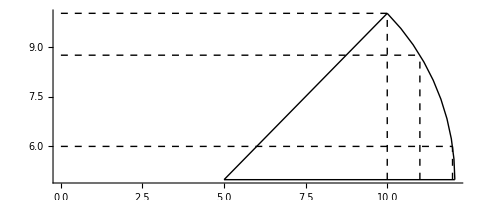

12

36

```mathematica
f[n_]:=f[n]=Module[{m=n/2,r=(n √2)/2},4+8 Count[Table[√(r^2-x^2),{x,Floor[n-m]+1,Floor[r]}],_Integer]]
g[n_]:=Module[{m=n/2,r=(n √2)/2},Module[{c={m,m}},Graphics[{Circle[c,r,{0,π/4}],Line[{c,{n,n}}],Line[{c,{m+r,m}}],Dashed,Line[{{n+0,m},{n+0,n}}],Line[{{0,n},{n,n}}],Line[{{n+1,m},{n+1,m+√(r^2-(n+1-m)^2)}}],Line[{{0,m+√(r^2-(n+1-m)^2)},{n+1,m+√(r^2-(n+1-m)^2)}}],Line[{{n+2,m},{n+2,m+√(r^2-(n+2-m)^2)}}],Line[{{0,m+√(r^2-(n+2-m)^2)},{n+2,m+√(r^2-(n+2-m)^2)}}]},Axes->True,AxesOrigin->{0,0}]]]
g[10]
f[10]
f[10000]
```

```mathematica
SquaresR[2,10000^2]
```

36

```mathematica
Select[Range[1000000],SquaresR[2,#^2]==420&]
```

{359125,469625,612625,718250,781625,866125,933725,939250}

```mathematica
FactorInteger@{359125,469625,612625,718250,781625,866125,933725,939250}//ColumnForm
```

{{5,3},{13,2},{17,1}}
{{5,3},{13,1},{17,2}}
{{5,3},{13,2},{29,1}}
{{2,1},{5,3},{13,2},{17,1}}
{{5,3},{13,2},{37,1}}
{{5,3},{13,2},{41,1}}
{{5,2},{13,3},{17,1}}
{{2,1},{5,3},{13,1},{17,2}}

## Problem 234

For an integer n  4, we define the lower prime square root of n, denoted by lps(n), as the largest prime  n and the upper prime square root of n, ups(n), as the smallest prime  n.

So, for example, lps(4) = 2 = ups(4), lps(1000) = 31, ups(1000) = 37.
Let us call an integer n  4 semidivisible, if one of lps(n) and ups(n) divides n, but not both.

The sum of the semidivisible numbers not exceeding 15 is 30, the numbers are 8, 10 and 12.
15 is not semidivisible because it is a multiple of both lps(15) = 3 and ups(15) = 5.
As a further example, the sum of the 92 semidivisible numbers up to 1000 is 34825.

What is the sum of all semidivisible numbers not exceeding 999966663333 ?

Problem 235

Given is the arithmetic-geometric sequence u(k) = (900-3k)rk-1.
Let s(n) = Σk=1...nu(k).

Find the value of r for which s(5000) = -600,000,000,000.

Give your answer rounded to 12 places behind the decimal point.

Problem 236

Suppliers 'A' and 'B' provided the following numbers of products for the luxury hamper market:

Product	'A'	'B'
Beluga Caviar	5248	640
Christmas Cake	1312	1888
Gammon Joint	2624	3776
Vintage Port	5760	3776
Champagne Truffles	3936	5664
Although the suppliers try very hard to ship their goods in perfect condition, there is inevitably some spoilage - i.e. products gone bad.

The suppliers compare their performance using two types of statistic:

The five per-product spoilage rates for each supplier are equal to the number of products gone bad divided by the number of products supplied, for each of the five products in turn.
The overall spoilage rate for each supplier is equal to the total number of products gone bad divided by the total number of products provided by that supplier.
To their surprise, the suppliers found that each of the five per-product spoilage rates was worse (higher) for 'B' than for 'A' by the same factor (ratio of spoilage rates), m>1; and yet, paradoxically, the overall spoilage rate was worse for 'A' than for 'B', also by a factor of m.

There are thirty-five m1 for which this surprising result could have occurred, the smallest of which is 1476/1475.

What's the largest possible value of m?
Give your answer as a fraction reduced to its lowest terms, in the form u/v.

Problem 237

Let T(n) be the number of tours over a 4  n playing board such that:

The tour starts in the top left corner.
The tour consists of moves that are up, down, left, or right one square.
The tour visits each square exactly once.
The tour ends in the bottom left corner.
The diagram shows one tour over a 4  10 board:


T(10) is 2329. What is T(1012) modulo 108?

Problem 238

Create a sequence of numbers using the "Blum Blum Shub" pseudo-random number generator:

s0	=	14025256
sn+1	=	sn2 mod 20300713
Concatenate these numbers  s0s1s2… to create a string w of infinite length.
Then, w = 14025256741014958470038053646…

For a positive integer k, if no substring of w exists with a sum of digits equal to k, p(k) is defined to be zero. If at least one substring of w exists with a sum of digits equal to k, we define p(k) = z, where z is the starting position of the earliest such substring.

For instance:

The substrings 1, 14, 1402, … 
with respective sums of digits equal to 1, 5, 7, …
start at position 1, hence p(1) = p(5) = p(7) = … = 1.

The substrings 4, 402, 4025, …
with respective sums of digits equal to 4, 6, 11, …
start at position 2, hence p(4) = p(6) = p(11) = … = 2.

The substrings 02, 0252, …
with respective sums of digits equal to 2, 9, …
start at position 3, hence p(2) = p(9) = … = 3.

Note that substring 025 starting at position 3, has a sum of digits equal to 7, but there was an earlier substring (starting at position 1) with a sum of digits equal to 7, so p(7) = 1, not 3.

We can verify that, for 0 < k  103,  p(k) = 4742.

Find  p(k), for 0 < k  2·1015.

Problem 239

A set of disks numbered 1 through 100 are placed in a line in random order.

What is the probability that we have a partial derangement such that exactly 22 prime number discs are found away from their natural positions?
(Any number of non-prime disks may also be found in or out of their natural positions.)

Give your answer rounded to 12 places behind the decimal point in the form 0.abcdefghijkl.

Problem 240

There are 1111 ways in which five 6-sided dice (sides numbered 1 to 6) can be rolled so that the top three sum to 15. Some examples are: 

D1,D2,D3,D4,D5 = 4,3,6,3,5 
D1,D2,D3,D4,D5 = 4,3,3,5,6 
D1,D2,D3,D4,D5 = 3,3,3,6,6 
D1,D2,D3,D4,D5 = 6,6,3,3,3 

In how many ways can twenty 12-sided dice (sides numbered 1 to 12) be rolled so that the top ten sum to 70?

Problem 241

For a positive integer n, let σ(n) be the sum of all divisors of n, so e.g. σ(6) = 1 + 2 + 3 + 6 = 12.

A perfect number, as you probably know, is a number with σ(n) = 2n.

Let us define the perfection quotient of a positive integer as	p(n)	= 	
σ(n)

n
.
Find the sum of all positive integers n  1018 for which p(n) has the form k + 1⁄2, where k is an integer.

Problem 242

Given the set {1,2,...,n}, we define f(n,k) as the number of its k-element subsets with an odd sum of elements. For example, f(5,3) = 4, since the set {1,2,3,4,5} has four 3-element subsets having an odd sum of elements, i.e.: {1,2,4}, {1,3,5}, {2,3,4} and {2,4,5}.

When all three values n, k and f(n,k) are odd, we say that they make 
an odd-triplet [n,k,f(n,k)].

There are exactly five odd-triplets with n  10, namely:
[1,1,f(1,1) = 1], [5,1,f(5,1) = 3], [5,5,f(5,5) = 1], [9,1,f(9,1) = 5] and [9,9,f(9,9) = 1].

How many odd-triplets are there with n  1012 ?

Problem 244

You probably know the game Fifteen Puzzle. Here, instead of numbered tiles, we have seven red tiles and eight blue tiles.

A move is denoted by the uppercase initial of the direction (Left, Right, Up, Down) in which the tile is slid, e.g. starting from configuration (S), by the sequence LULUR we reach the configuration (E):

(S)		, (E)	
For each path, its checksum is calculated by (pseudocode):

checksum = 0
checksum = (checksum  243 + m1) mod 100 000 007
checksum = (checksum  243 + m2) mod 100 000 007
   …
checksum = (checksum  243 + mn) mod 100 000 007
where mk is the ASCII value of the kth letter in the move sequence and the ASCII values for the moves are:
L	76
R	82
U	85
D	68
For the sequence LULUR given above, the checksum would be 19761398.

Now, starting from configuration (S), find all shortest ways to reach configuration (T).

(S)		, (T)	
What is the sum of all checksums for the paths having the minimal length?

Problem 245

We shall call a fraction that cannot be cancelled down a resilient fraction.
Furthermore we shall define the resilience of a denominator, R(d), to be the ratio of its proper fractions that are resilient; for example, R(12) = 4⁄11.

The resilience of a number d  1 is then	
φ(d)

d - 1
, where φ is Euler's totient function.
We further define the coresilience of a number n  1 as C(n)	= 	
n - φ(n)

n - 1
.
The coresilience of a prime p is C(p)	= 	
1

p - 1
.
Find the sum of all composite integers 1  n  21011, for which C(n) is a unit fraction.

Note: the upper limit has been changed recently. Check out that you use the right upper limit.

Problem 246

A definition for an ellipse is:
Given a circle c with centre M and radius r and a point G such that d(G,M)r, the locus of the points that are equidistant from c and G form an ellipse.

The construction of the points of the ellipse is shown below.

Given are the points M(-2000,1500) and G(8000,1500).
Given is also the circle c with centre M and radius 15000.
The locus of the points that are equidistant from G and c form an ellipse e.
From a point P outside e the two tangents t1 and t2 to the ellipse are drawn.
Let the points where t1 and t2 touch the ellipse be R and S.


For how many lattice points P is angle RPS greater than 45 degrees?

Problem 247

Consider the region constrained by 1  x and 0  y  1/x.

Let S1 be the largest square that can fit under the curve.
Let S2 be the largest square that fits in the remaining area, and so on. 
Let the index of Sn be the pair (left, below) indicating the number of squares to the left of Sn and the number of squares below Sn.


The diagram shows some such squares labelled by number. 
S2 has one square to its left and none below, so the index of S2 is (1,0).
It can be seen that the index of S32 is (1,1) as is the index of S50. 
50 is the largest n for which the index of Sn is (1,1).

What is the largest n for which the index of Sn is (3,3)?

Problem 248

The first number n for which φ(n)=13! is 6227180929.

Find the 150,000th such number.

Note: The number to find has been changed recently. Check out that you have computed the right number.

Problem 249

Let S = {2, 3, 5, ..., 4999} be the set of prime numbers less than 5000.

Find the number of subsets of S, the sum of whose elements is a prime number.
Enter the rightmost 16 digits as your answer.

Problem 250

Find the number of non-empty subsets of {11, 22, 33,..., 250250250250}, the sum of whose elements is divisible by 250. Enter the rightmost 16 digits as your answer.

Problem 251

A triplet of positive integers (a,b,c) is called a Cardano Triplet if it satisfies the condition:


For example, (2,1,5) is a Cardano Triplet.

There exist 149 Cardano Triplets for which a+b+c  1000.

Find how many Cardano Triplets exist such that a+b+c  110,000,000.

Note: This problem has been changed recently, please check that you are using the right parameters.

Problem 252

Given a set of points on a plane, we define a convex hole to be a convex polygon having as vertices any of the given points and not containing any of the given points in its interior (in addition to the vertices, other given points may lie on the perimeter of the polygon).

As an example, the image below shows a set of twenty points and a few such convex holes. The convex hole shown as a red heptagon has an area equal to 1049694.5 square units, which is the highest possible area for a convex hole on the given set of points.


For our example, we used the first 20 points (T2k1, T2k), for k = 1,2,…,20, produced with the pseudo-random number generator:

S0	= 	290797 
Sn+1	= 	Sn2 mod 50515093
Tn	= 	( Sn mod 2000 )  1000 
i.e. (527, 144), (488, 732), (454, 947), …

What is the maximum area for a convex hole on the set containing the first 500 points in the pseudo-random sequence?
Specify your answer including one digit after the decimal point.

Problem 253

A small child has a "number caterpillar" consisting of forty jigsaw pieces, each with one number on it, which, when connected together in a line, reveal the numbers 1 to 40 in order.

Every night, the child's father has to pick up the pieces of the caterpillar that have been scattered across the play room. He picks up the pieces at random and places them in the correct order.
As the caterpillar is built up in this way, it forms distinct segments that gradually merge together.
The number of segments starts at zero (no pieces placed), generally increases up to about eleven or twelve, then tends to drop again before finishing at a single segment (all pieces placed).

For example:

Piece Placed	Segments So Far
12	1
4	2
29	3
6	4
34	5
5	4
35	4
…	…
Let M be the maximum number of segments encountered during a random tidy-up of the caterpillar.
For a caterpillar of ten pieces, the number of possibilities for each M is

M	Possibilities
1	512      
2	250912      
3	1815264      
4	1418112      
5	144000      
so the most likely value of M is 3 and the average value is 385643⁄113400 = 3.400732, rounded to six decimal places.

The most likely value of M for a forty-piece caterpillar is 11; but what is the average value of M?

Give your answer rounded to six decimal places.

Problem 254

Define f(n) as the sum of the factorials of the digits of n. For example, f(342) = 3! + 4! + 2! = 32.

Define sf(n) as the sum of the digits of f(n). So sf(342) = 3 + 2 = 5.

Define g(i) to be the smallest positive integer n such that sf(n) = i. Though sf(342) is 5, sf(25) is also 5, and it can be verified that g(5) is 25.

Define sg(i) as the sum of the digits of g(i). So sg(5) = 2 + 5 = 7.

Further, it can be verified that g(20) is 267 and  sg(i) for 1  i  20 is 156.

What is  sg(i) for 1  i  150?

Problem 255

We define the rounded-square-root of a positive integer n as the square root of n rounded to the nearest integer.

The following procedure (essentially Heron's method adapted to integer arithmetic) finds the rounded-square-root of n:

Let d be the number of digits of the number n.
If d is odd, set x0 = 210(d-1)⁄2.
If d is even, set x0 = 710(d-2)⁄2.
Repeat:



until xk+1 = xk.

As an example, let us find the rounded-square-root of n = 4321.
n has 4 digits, so x0 = 710(4-2)⁄2 = 70.
 
Since x2 = x1, we stop here.
So, after just two iterations, we have found that the rounded-square-root of 4321 is 66 (the actual square root is 65.7343137…).

The number of iterations required when using this method is surprisingly low.
For example, we can find the rounded-square-root of a 5-digit integer (10,000  n  99,999) with an average of 3.2102888889 iterations (the average value was rounded to 10 decimal places).

Using the procedure described above, what is the average number of iterations required to find the rounded-square-root of a 14-digit number (1013  n  1014)?
Give your answer rounded to 10 decimal places.

Note: The symbols x and x represent the floor function and ceiling function respectively.

Problem 256

Tatami are rectangular mats, used to completely cover the floor of a room, without overlap.

Assuming that the only type of available tatami has dimensions 12, there are obviously some limitations for the shape and size of the rooms that can be covered.

For this problem, we consider only rectangular rooms with integer dimensions a, b and even size s = a·b.
We use the term 'size' to denote the floor surface area of the room, and — without loss of generality — we add the condition a  b.

There is one rule to follow when laying out tatami: there must be no points where corners of four different mats meet.
For example, consider the two arrangements below for a 44 room:


The arrangement on the left is acceptable, whereas the one on the right is not: a red "X" in the middle, marks the point where four tatami meet.

Because of this rule, certain even-sized rooms cannot be covered with tatami: we call them tatami-free rooms.
Further, we define T(s) as the number of tatami-free rooms of size s.

The smallest tatami-free room has size s = 70 and dimensions 710.
All the other rooms of size s = 70 can be covered with tatami; they are: 170, 235 and 514.
Hence, T(70) = 1.

Similarly, we can verify that T(1320) = 5 because there are exactly 5 tatami-free rooms of size s = 1320:
2066, 2260, 2455, 3044 and 3340.
In fact, s = 1320 is the smallest room-size s for which T(s) = 5.

Find the smallest room-size s for which T(s) = 200.

Problem 257

Given is an integer sided triangle ABC with sides a  b  c. (AB = c, BC = a and AC = b).
The angular bisectors of the triangle intersect the sides at points E, F and G (see picture below).


The segments EF, EG and FG partition the triangle ABC into four smaller triangles: AEG, BFE, CGF and EFG.
It can be proven that for each of these four triangles the ratio area(ABC)/area(subtriangle) is rational.
However, there exist triangles for which some or all of these ratios are integral.

How many triangles ABC with perimeter100,000,000 exist so that the ratio area(ABC)/area(AEG) is integral?

Problem 258

A sequence is defined as:

gk = 1, for 0  k  1999
gk = gk-2000 + gk-1999, for k  2000.
Find gk mod 20092010 for k = 1018.

Problem 259

A positive integer will be called reachable if it can result from an arithmetic expression obeying the following rules:

Uses the digits 1 through 9, in that order and exactly once each.
Any successive digits can be concatenated (for example, using the digits 2, 3 and 4 we obtain the number 234).
Only the four usual binary arithmetic operations (addition, subtraction, multiplication and division) are allowed.
Each operation can be used any number of times, or not at all.
Unary minus is not allowed.
Any number of (possibly nested) parentheses may be used to define the order of operations.
For example, 42 is reachable, since (1/23) * ((4*5)-6) * (78-9) = 42.

What is the sum of all positive reachable integers?

Problem 260

A game is played with three piles of stones and two players.
At her turn, a player removes one or more stones from the piles. However, if she takes stones from more than one pile, she must remove the same number of stones from each of the selected piles.

In other words, the player chooses some N>0 and removes:

N stones from any single pile; or
N stones from each of any two piles (2N total); or
N stones from each of the three piles (3N total).
The player taking the last stone(s) wins the game.
A winning configuration is one where the first player can force a win.
For example, (0,0,13), (0,11,11) and (5,5,5) are winning configurations because the first player can immediately remove all stones.

A losing configuration is one where the second player can force a win, no matter what the first player does.
For example, (0,1,2) and (1,3,3) are losing configurations: any legal move leaves a winning configuration for the second player.

Consider all losing configurations (xi,yi,zi) where xi  yi  zi  100.
We can verify that Σ(xi+yi+zi) = 173895 for these.

Find Σ(xi+yi+zi) where (xi,yi,zi) ranges over the losing configurations
with xi  yi  zi  1000.

Problem 261

Let us call a positive integer k a square-pivot, if there is a pair of integers m  0 and n  k, such that the sum of the (m+1) consecutive squares up to k equals the sum of the m consecutive squares from (n+1) on:

(k-m)2 + ... + k2 = (n+1)2 + ... + (n+m)2.
Some small square-pivots are

4: 32 + 42 = 52
21: 202 + 212 = 292
24: 212 + 222 + 232 + 242 = 252 + 262 + 272
110: 1082 + 1092 + 1102 = 1332 + 1342
Find the sum of all distinct square-pivots  1010.

Problem 262

The following equation represents the continuous topography of a mountainous region, giving the elevation h at any point (x,y):


A mosquito intends to fly from A(200,200) to B(1400,1400), without leaving the area given by 0 ≤ x, y ≤ 1600.

Because of the intervening mountains, it first rises straight up to a point A', having elevation f. Then, while remaining at the same elevation f, it flies around any obstacles until it arrives at a point B' directly above B.

First, determine fmin which is the minimum constant elevation allowing such a trip from A to B, while remaining in the specified area.
Then, find the length of the shortest path between A' and B', while flying at that constant elevation fmin.

Give that length as your answer, rounded to three decimal places.

Note: For convenience, the elevation function shown above is repeated below, in a form suitable for most programming languages:
h=( 5000-0.005*(x*x+y*y+x*y)+12.5*(x+y) ) * exp( -abs(0.000001*(x*x+y*y)-0.0015*(x+y)+0.7) )

Problem 263

Consider the number 6. The divisors of 6 are: 1,2,3 and 6.
Every number from 1 up to and including 6 can be written as a sum of distinct divisors of 6:
1=1, 2=2, 3=1+2, 4=1+3, 5=2+3, 6=6.
A number n is called a practical number if every number from 1 up to and including n can be expressed as a sum of distinct divisors of n.

A pair of consecutive prime numbers with a difference of six is called a sexy pair (since "sex" is the Latin word for "six"). The first sexy pair is (23, 29).

We may occasionally find a triple-pair, which means three consecutive sexy prime pairs, such that the second member of each pair is the first member of the next pair.

We shall call a number n such that :

(n-9, n-3), (n-3,n+3), (n+3, n+9) form a triple-pair, and
the numbers n-8, n-4, n, n+4 and n+8 are all practical,
an engineers' paradise.
Find the sum of the first four engineers' paradises.

Problem 264

Consider all the triangles having:

All their vertices on lattice points.
Circumcentre at the origin O.
Orthocentre at the point H(5, 0).
There are nine such triangles having a perimeter  50.
Listed and shown in ascending order of their perimeter, they are:

A(-4, 3), B(5, 0), C(4, -3)
A(4, 3), B(5, 0), C(-4, -3)
A(-3, 4), B(5, 0), C(3, -4)


A(3, 4), B(5, 0), C(-3, -4)
A(0, 5), B(5, 0), C(0, -5)
A(1, 8), B(8, -1), C(-4, -7)


A(8, 1), B(1, -8), C(-4, 7)
A(2, 9), B(9, -2), C(-6, -7)
A(9, 2), B(2, -9), C(-6, 7)

The sum of their perimeters, rounded to four decimal places, is 291.0089.

Find all such triangles with a perimeter  105.
Enter as your answer the sum of their perimeters rounded to four decimal places.

Problem 265

2N binary digits can be placed in a circle so that all the N-digit clockwise subsequences are distinct.

For N=3, two such circular arrangements are possible, ignoring rotations:


For the first arrangement, the 3-digit subsequences, in clockwise order, are:
000, 001, 010, 101, 011, 111, 110 and 100.

Each circular arrangement can be encoded as a number by concatenating the binary digits starting with the subsequence of all zeros as the most significant bits and proceeding clockwise. The two arrangements for N=3 are thus represented as 23 and 29:

00010111 2 = 23
00011101 2 = 29
Calling S(N) the sum of the unique numeric representations, we can see that S(3) = 23 + 29 = 52.

Find S(5).

Problem 266

The divisors of 12 are: 1,2,3,4,6 and 12.
The largest divisor of 12 that does not exceed the square root of 12 is 3.
We shall call the largest divisor of an integer n that does not exceed the square root of n the pseudo square root (PSR) of n.
It can be seen that PSR(3102)=47.

Let p be the product of the primes below 190.
Find PSR(p) mod 1016.

Problem 267

You are given a unique investment opportunity.

Starting with £1 of capital, you can choose a fixed proportion, f, of your capital to bet on a fair coin toss repeatedly for 1000 tosses.

Your return is double your bet for heads and you lose your bet for tails.

For example, if f = 1/4, for the first toss you bet £0.25, and if heads comes up you win £0.5 and so then have £1.5. You then bet £0.375 and if the second toss is tails, you have £1.125.

Choosing f to maximize your chances of having at least £1,000,000,000 after 1,000 flips, what is the chance that you become a billionaire?

All computations are assumed to be exact (no rounding), but give your answer rounded to 12 digits behind the decimal point in the form 0.abcdefghijkl.

Problem 268

It can be verified that there are 23 positive integers less than 1000 that are divisible by at least four distinct primes less than 100.

Find how many positive integers less than 1016 are divisible by at least four distinct primes less than 100.

Problem 269

A root or zero of a polynomial P(x) is a solution to the equation P(x) = 0. 
Define Pn as the polynomial whose coefficients are the digits of n.
For example, P5703(x) = 5x3 + 7x2 + 3.

We can see that:

Pn(0) is the last digit of n,
Pn(1) is the sum of the digits of n,
Pn(10) is n itself.
Define Z(k) as the number of positive integers, n, not exceeding k for which the polynomial Pn has at least one integer root.

It can be verified that Z(100 000) is 14696.

What is Z(1016)?

Problem 270

A square piece of paper with integer dimensions NN is placed with a corner at the origin and two of its sides along the x- and y-axes. Then, we cut it up respecting the following rules:

We only make straight cuts between two points lying on different sides of the square, and having integer coordinates.
Two cuts cannot cross, but several cuts can meet at the same border point.
Proceed until no more legal cuts can be made.
Counting any reflections or rotations as distinct, we call C(N) the number of ways to cut an NN square. For example, C(1) = 2 and C(2) = 30 (shown below).


What is C(30) mod 108 ?

Problem 271

For a positive number n, define S(n) as the sum of the integers x, for which 1xn and
x31 mod n.

When n=91, there are 8 possible values for x, namely : 9, 16, 22, 29, 53, 74, 79, 81.
Thus, S(91)=9+16+22+29+53+74+79+81=363.

Find S(13082761331670030).

Problem 272

For a positive number n, define C(n) as the number of the integers x, for which 1xn and
x31 mod n.

When n=91, there are 8 possible values for x, namely : 9, 16, 22, 29, 53, 74, 79, 81.
Thus, C(91)=8.

Find the sum of the positive numbers n1011 for which C(n)=242.

Problem 273

Consider equations of the form: a2 + b2 = N, 0  a  b, a, b and N integer.

For N=65 there are two solutions:

a=1, b=8 and a=4, b=7.

We call S(N) the sum of the values of a of all solutions of a2 + b2 = N, 0  a  b, a, b and N integer.

Thus S(65) = 1 + 4 = 5.

Find S(N), for all squarefree N only divisible by primes of the form 4k+1 with 4k+1  150.

Problem 274

For each integer p  1 coprime to 10 there is a positive divisibility multiplier m  p which preserves divisibility by p for the following function on any positive integer, n:

f(n) = (all but the last digit of n) + (the last digit of n) * m

That is, if m is the divisibility multiplier for p, then f(n) is divisible by p if and only if n is divisible by p.

(When n is much larger than p, f(n) will be less than n and repeated application of f provides a multiplicative divisibility test for p.)

For example, the divisibility multiplier for 113 is 34.

f(76275) = 7627 + 5 * 34 = 7797 : 76275 and 7797 are both divisible by 113
f(12345) = 1234 + 5 * 34 = 1404 : 12345 and 1404 are both not divisible by 113

The sum of the divisibility multipliers for the primes that are coprime to 10 and less than 1000 is 39517. What is the sum of the divisibility multipliers for the primes that are coprime to 10 and less than 107?

Problem 275

Let us define a balanced sculpture of order n as follows:

A polyomino made up of n+1 tiles known as the blocks (n tiles)
and the plinth (remaining tile);
the plinth has its centre at position (x = 0, y = 0);
the blocks have y-coordinates greater than zero (so the plinth is the unique lowest tile);
the centre of mass of all the blocks, combined, has x-coordinate equal to zero.
When counting the sculptures, any arrangements which are simply reflections about the y-axis, are not counted as distinct. For example, the 18 balanced sculptures of order 6 are shown below; note that each pair of mirror images (about the y-axis) is counted as one sculpture:


There are 964 balanced sculptures of order 10 and 360505 of order 15.
How many balanced sculptures are there of order 18?

Problem 276

Consider the triangles with integer sides a, b and c with a  b  c.
An integer sided triangle (a,b,c) is called primitive if gcd(a,b,c)=1. 
How many primitive integer sided triangles exist with a perimeter not exceeding 10 000 000?

Problem 277

A modified Collatz sequence of integers is obtained from a starting value a1 in the following way:

an+1 = an/3 if an is divisible by 3. We shall denote this as a large downward step, "D".

an+1 = (4an + 2)/3 if an divided by 3 gives a remainder of 1. We shall denote this as an upward step, "U".

an+1 = (2an - 1)/3 if an divided by 3 gives a remainder of 2. We shall denote this as a small downward step, "d".

The sequence terminates when some an = 1.

Given any integer, we can list out the sequence of steps.
For instance if a1=231, then the sequence {an}={231,77,51,17,11,7,10,14,9,3,1} corresponds to the steps "DdDddUUdDD".

Of course, there are other sequences that begin with that same sequence "DdDddUUdDD....".
For instance, if a1=1004064, then the sequence is DdDddUUdDDDdUDUUUdDdUUDDDUdDD.
In fact, 1004064 is the smallest possible a1  106 that begins with the sequence DdDddUUdDD.

What is the smallest a1  1015 that begins with the sequence "UDDDUdddDDUDDddDdDddDDUDDdUUDd"?

Problem 278

Given the values of integers 1  a1  a2 ...  an, consider the linear combination
q1a1 + q2a2 + ... + qnan = b, using only integer values qk  0.

Note that for a given set of ak, it may be that not all values of b are possible.
For instance, if a1 = 5 and a2 = 7, there are no q1  0 and q2  0 such that b could be
1, 2, 3, 4, 6, 8, 9, 11, 13, 16, 18 or 23. 
In fact, 23 is the largest impossible value of b for a1 = 5 and a2 = 7.
We therefore call f(5, 7) = 23.
Similarly, it can be shown that f(6, 10, 15)=29 and f(14, 22, 77) = 195.

Find  f(p*q,p*r,q*r), where p, q and r are prime numbers and p < q  r  5000.

Problem 279

How many triangles are there with integral sides, at least one integral angle (measured in degrees), and a perimeter that does not exceed 108?

Problem 280

A laborious ant walks randomly on a 5x5 grid. The walk starts from the central square. At each step, the ant moves to an adjacent square at random, without leaving the grid; thus there are 2, 3 or 4 possible moves at each step depending on the ant's position.

At the start of the walk, a seed is placed on each square of the lower row. When the ant isn't carrying a seed and reaches a square of the lower row containing a seed, it will start to carry the seed. The ant will drop the seed on the first empty square of the upper row it eventually reaches.

What's the expected number of steps until all seeds have been dropped in the top row? 
Give your answer rounded to 6 decimal places.

Problem 281

You are given a pizza (perfect circle) that has been cut into m·n equal pieces and you want to have exactly one topping on each slice.

Let f(m,n) denote the number of ways you can have toppings on the pizza with m different toppings (m  2), using each topping on exactly n slices (n  1). 
Reflections are considered distinct, rotations are not.

Thus, for instance, f(2,1) = 1, f(2,2) = f(3,1) = 2 and f(3,2) = 16. 
f(3,2) is shown below:


Find the sum of all f(m,n) such that f(m,n)  1015.

Problem 282

For non-negative integers m, n, the Ackermann function A(m, n) is defined as follows:


For example A(1, 0) = 2, A(2, 2) = 7 and A(3, 4) = 125.

Find A(n, n) and give your answer mod 148.

Problem 283

Consider the triangle with sides 6, 8 and 10. It can be seen that the perimeter and the area are both equal to 24. So the area/perimeter ratio is equal to 1.
Consider also the triangle with sides 13, 14 and 15. The perimeter equals 42 while the area is equal to 84. So for this triangle the area/perimeter ratio is equal to 2.

Find the sum of the perimeters of all integer sided triangles for which the area/perimeter ratios are equal to positive integers not exceeding 1000.

Problem 284

The 3-digit number 376 in the decimal numbering system is an example of numbers with the special property that its square ends with the same digits: 3762 = 141376. Let's call a number with this property a steady square.

Steady squares can also be observed in other numbering systems. In the base 14 numbering system, the 3-digit number c37 is also a steady square: c372 = aa0c37, and the sum of its digits is c+3+7=18 in the same numbering system. The letters a, b, c and d are used for the 10, 11, 12 and 13 digits respectively, in a manner similar to the hexadecimal numbering system.

For 1  n  9, the sum of the digits of all the n-digit steady squares in the base 14 numbering system is 2d8 (582 decimal). Steady squares with leading 0's are not allowed.

Find the sum of the digits of all the n-digit steady squares in the base 14 numbering system for
1  n  10000 (decimal) and give your answer in the base 14 system using lower case letters where necessary.

Problem 285

Albert chooses a positive integer k, then two real numbers a, b are randomly chosen in the interval [0,1] with uniform distribution.
The square root of the sum (k·a+1)2 + (k·b+1)2 is then computed and rounded to the nearest integer. If the result is equal to k, he scores k points; otherwise he scores nothing.

For example, if k = 6, a = 0.2 and b = 0.85, then (k·a+1)2 + (k·b+1)2 = 42.05.
The square root of 42.05 is 6.484... and when rounded to the nearest integer, it becomes 6.
This is equal to k, so he scores 6 points.

It can be shown that if he plays 10 turns with k = 1, k = 2, ..., k = 10, the expected value of his total score, rounded to five decimal places, is 10.20914.

If he plays 105 turns with k = 1, k = 2, k = 3, ..., k = 105, what is the expected value of his total score, rounded to five decimal places?

Problem 286

Barbara is a mathematician and a basketball player. She has found that the probability of scoring a point when shooting from a distance x is exactly (1 - x/q), where q is a real constant greater than 50.

During each practice run, she takes shots from distances x = 1, x = 2, ..., x = 50 and, according to her records, she has precisely a 2 % chance to score a total of exactly 20 points.

Find q and give your answer rounded to 10 decimal places.

Problem 287

The quadtree encoding allows us to describe a 2N2N black and white image as a sequence of bits (0 and 1). Those sequences are to be read from left to right like this:

the first bit deals with the complete 2N2N region;
"0" denotes a split: 
the current 2n2n region is divided into 4 sub-regions of dimension 2n-12n-1,
the next bits contains the description of the top left, top right, bottom left and bottom right sub-regions - in that order;
"10" indicates that the current region contains only black pixels;
"11" indicates that the current region contains only white pixels.
Consider the following 44 image (colored marks denote places where a split can occur):


This image can be described by several sequences, for example : "001010101001011111011010101010", of length 30, or
"0100101111101110", of length 16, which is the minimal sequence for this image.

For a positive integer N, define DN as the 2N2N image with the following coloring scheme:

the pixel with coordinates x = 0, y = 0 corresponds to the bottom left pixel,
if (x - 2N-1)2 + (y - 2N-1)2  22N-2 then the pixel is black,
otherwise the pixel is white.
What is the length of the minimal sequence describing D24 ?

Problem 288

For any prime p the number N(p,q) is defined by N(p,q) = n=0 to q Tn*pn
with Tn generated by the following random number generator:

S0 = 290797
Sn+1 = Sn2 mod 50515093
Tn = Sn mod p

Let Nfac(p,q) be the factorial of N(p,q).
Let NF(p,q) be the number of factors p in Nfac(p,q).

You are given that NF(3,10000) mod 320=624955285.

Find NF(61,107) mod 6110

Problem 289

Let C(x,y) be a circle passing through the points (x, y), (x, y+1), (x+1, y) and (x+1, y+1).

For positive integers m and n, let E(m,n) be a configuration which consists of the m·n circles:
{ C(x,y): 0 ≤ x < m, 0 ≤ y < n, x and y are integers }

An Eulerian cycle on E(m,n) is a closed path that passes through each arc exactly once.
Many such paths are possible on E(m,n), but we are only interested in those which are not self-crossing: A non-crossing path just touches itself at lattice points, but it never crosses itself.

The image below shows E(3,3) and an example of an Eulerian non-crossing path.

Let L(m,n) be the number of Eulerian non-crossing paths on E(m,n).
For example, L(1,2) = 2, L(2,2) = 37 and L(3,3) = 104290.

Find L(6,10) mod 1010.

Problem 290

How many integers 0  n < 1018 have the property that the sum of the digits of n equals the sum of digits of 137n?

Problem 291

A prime number p is called a Panaitopol prime if  for some positive integers
x and y.

Find how many Panaitopol primes are less than 51015.

Problem 292

We shall define a pythagorean polygon to be a convex polygon with the following properties:
there are at least three vertices,
no three vertices are aligned,
each vertex has integer coordinates,
each edge has integer length.
For a given integer n, define P(n) as the number of distinct pythagorean polygons for which the perimeter is  n.
Pythagorean polygons should be considered distinct as long as none is a translation of another.

You are given that P(4) = 1, P(30) = 3655 and P(60) = 891045.
Find P(120).

Problem 293

An even positive integer N will be called admissible, if it is a power of 2 or its distinct prime factors are consecutive primes.
The first twelve admissible numbers are 2,4,6,8,12,16,18,24,30,32,36,48.

If N is admissible, the smallest integer M  1 such that N+M is prime, will be called the pseudo-Fortunate number for N.

For example, N=630 is admissible since it is even and its distinct prime factors are the consecutive primes 2,3,5 and 7.
The next prime number after 631 is 641; hence, the pseudo-Fortunate number for 630 is M=11.
It can also be seen that the pseudo-Fortunate number for 16 is 3.

Find the sum of all distinct pseudo-Fortunate numbers for admissible numbers N less than 109.

Problem 294

For a positive integer k, define d(k) as the sum of the digits of k in its usual decimal representation. Thus d(42) = 4+2 = 6.

For a positive integer n, define S(n) as the number of positive integers k < 10n with the following properties :

k is divisible by 23 and
d(k) = 23.
You are given that S(9) = 263626 and S(42) = 6377168878570056.
Find S(1112) and give your answer mod 109.

Problem 295

We call the convex area enclosed by two circles a lenticular hole if:

The centres of both circles are on lattice points.
The two circles intersect at two distinct lattice points.
The interior of the convex area enclosed by both circles does not contain any lattice points.
Consider the circles:
C0: x2+y2=25
C1: (x+4)2+(y-4)2=1
C2: (x-12)2+(y-4)2=65

The circles C0, C1 and C2 are drawn in the picture below.


C0 and C1 form a lenticular hole, as well as C0 and C2.

We call an ordered pair of positive real numbers (r1, r2) a lenticular pair if there exist two circles with radii r1 and r2 that form a lenticular hole. We can verify that (1, 5) and (5, 65) are the lenticular pairs of the example above.

Let L(N) be the number of distinct lenticular pairs (r1, r2) for which 0  r1  r2  N.
We can verify that L(10) = 30 and L(100) = 3442.

Find L(100 000).

Problem 296

Given is an integer sided triangle ABC with BC  AC  AB.
k is the angular bisector of angle ACB.
m is the tangent at C to the circumscribed circle of ABC.
n is a line parallel to m through B.
The intersection of n and k is called E.


How many triangles ABC with a perimeter not exceeding 100 000 exist such that BE has integral length?

Problem 297

Each new term in the Fibonacci sequence is generated by adding the previous two terms.
Starting with 1 and 2, the first 10 terms will be: 1, 2, 3, 5, 8, 13, 21, 34, 55, 89.

Every positive integer can be uniquely written as a sum of nonconsecutive terms of the Fibonacci sequence. For example, 100 = 3 + 8 + 89.
Such a sum is called the Zeckendorf representation of the number.

For any integer n>0, let z(n) be the number of terms in the Zeckendorf representation of n.
Thus, z(5) = 1, z(14) = 2, z(100) = 3 etc.
Also, for 0n106, ∑ z(n) = 7894453.

Find ∑ z(n) for 0n1017.

Problem 298

Larry and Robin play a memory game involving of a sequence of random numbers between 1 and 10, inclusive, that are called out one at a time. Each player can remember up to 5 previous numbers. When the called number is in a player's memory, that player is awarded a point. If it's not, the player adds the called number to his memory, removing another number if his memory is full.

Both players start with empty memories. Both players always add new missed numbers to their memory but use a different strategy in deciding which number to remove:
Larry's strategy is to remove the number that hasn't been called in the longest time.
Robin's strategy is to remove the number that's been in the memory the longest time.

Example game:
Turn	Called
number	Larry's
memory	Larry's
score	Robin's
memory	Robin's
score
1	1	1	0	1	0
2	2	1,2	0	1,2	0
3	4	1,2,4	0	1,2,4	0
4	6	1,2,4,6	0	1,2,4,6	0
5	1	1,2,4,6	1	1,2,4,6	1
6	8	1,2,4,6,8	1	1,2,4,6,8	1
7	10	1,4,6,8,10	1	2,4,6,8,10	1
8	2	1,2,6,8,10	1	2,4,6,8,10	2
9	4	1,2,4,8,10	1	2,4,6,8,10	3
10	1	1,2,4,8,10	2	1,4,6,8,10	3
Denoting Larry's score by L and Robin's score by R, what is the expected value of |L-R| after 50 turns? Give your answer rounded to eight decimal places using the format x.xxxxxxxx .

Problem 299

Four points with integer coordinates are selected:
A(a, 0), B(b, 0), C(0, c) and D(0, d), with 0  a  b and 0  c  d.
Point P, also with integer coordinates, is chosen on the line AC so that the three triangles ABP, CDP and BDP are all similar.


It is easy to prove that the three triangles can be similar, only if a=c.

So, given that a=c, we are looking for triplets (a,b,d) such that at least one point P (with integer coordinates) exists on AC, making the three triangles ABP, CDP and BDP all similar.

For example, if (a,b,d)=(2,3,4), it can be easily verified that point P(1,1) satisfies the above condition. Note that the triplets (2,3,4) and (2,4,3) are considered as distinct, although point P(1,1) is common for both.

If b+d  100, there are 92 distinct triplets (a,b,d) such that point P exists.
If b+d  100 000, there are 320471 distinct triplets (a,b,d) such that point P exists.

If b+d  100 000 000, how many distinct triplets (a,b,d) are there such that point P exists?

Problem 300

In a very simplified form, we can consider proteins as strings consisting of hydrophobic (H) and polar (P) elements, e.g. HHPPHHHPHHPH. 
For this problem, the orientation of a protein is important; e.g. HPP is considered distinct from PPH. Thus, there are 2n distinct proteins consisting of n elements.

When one encounters these strings in nature, they are always folded in such a way that the number of H-H contact points is as large as possible, since this is energetically advantageous.
As a result, the H-elements tend to accumulate in the inner part, with the P-elements on the outside.
Natural proteins are folded in three dimensions of course, but we will only consider protein folding in two dimensions.

The figure below shows two possible ways that our example protein could be folded (H-H contact points are shown with red dots).


The folding on the left has only six H-H contact points, thus it would never occur naturally.
On the other hand, the folding on the right has nine H-H contact points, which is optimal for this string.

Assuming that H and P elements are equally likely to occur in any position along the string, the average number of H-H contact points in an optimal folding of a random protein string of length 8 turns out to be 850 / 28=3.3203125.

What is the average number of H-H contact points in an optimal folding of a random protein string of length 15?
Give your answer using as many decimal places as necessary for an exact result.

Problem 301

Nim is a game played with heaps of stones, where two players take it in turn to remove any number of stones from any heap until no stones remain.

We'll consider the three-heap normal-play version of Nim, which works as follows:
- At the start of the game there are three heaps of stones.
- On his turn the player removes any positive number of stones from any single heap.
- The first player unable to move (because no stones remain) loses.

If (n1,n2,n3) indicates a Nim position consisting of heaps of size n1, n2 and n3 then there is a simple function X(n1,n2,n3) — that you may look up or attempt to deduce for yourself — that returns:

zero if, with perfect strategy, the player about to move will eventually lose; or
non-zero if, with perfect strategy, the player about to move will eventually win.
For example X(1,2,3) = 0 because, no matter what the current player does, his opponent can respond with a move that leaves two heaps of equal size, at which point every move by the current player can be mirrored by his opponent until no stones remain; so the current player loses. To illustrate:
- current player moves to (1,2,1)
- opponent moves to (1,0,1)
- current player moves to (0,0,1)
- opponent moves to (0,0,0), and so wins.

For how many positive integers n  230 does X(n,2n,3n) = 0 ?

Problem 302

A positive integer n is powerful if p2 is a divisor of n for every prime factor p in n.

A positive integer n is a perfect power if n can be expressed as a power of another positive integer.

A positive integer n is an Achilles number if n is powerful but not a perfect power. For example, 864 and 1800 are Achilles numbers: 864 = 25·33 and 1800 = 23·32·52.

We shall call a positive integer S a Strong Achilles number if both S and φ(S) are Achilles numbers.1
For example, 864 is a Strong Achilles number: φ(864) = 288 = 25·32. However, 1800 isn't a Strong Achilles number because: φ(1800) = 480 = 25·31·51.

There are 7 Strong Achilles numbers below 104 and 656 below 108.

How many Strong Achilles numbers are there below 1018?

1 φ denotes Euler's totient function.

Problem 303

For a positive integer n, define f(n) as the least positive multiple of n that, written in base 10, uses only digits  2.

Thus f(2)=2, f(3)=12, f(7)=21, f(42)=210, f(89)=1121222.

Also, .

Find .

Problem 304

For any positive integer n the function next_prime(n) returns the smallest prime p 
such that pn.

The sequence a(n) is defined by:
a(1)=next_prime(1014) and a(n)=next_prime(a(n-1)) for n1.

The fibonacci sequence f(n) is defined by: f(0)=0, f(1)=1 and f(n)=f(n-1)+f(n-2) for n1.

The sequence b(n) is defined as f(a(n)).

Find b(n) for 1n100 000. Give your answer mod 1234567891011.

Problem 305

Let's call S the (infinite) string that is made by concatenating the consecutive positive integers (starting from 1) written down in base 10.
Thus, S = 1234567891011121314151617181920212223242...

It's easy to see that any number will show up an infinite number of times in S.

Let's call f(n) the starting position of the nth occurrence of n in S.
For example, f(1)=1, f(5)=81, f(12)=271 and f(7780)=111111365.

Find f(3k) for 1k13.

Problem 306

The following game is a classic example of Combinatorial Game Theory:

Two players start with a strip of n white squares and they take alternate turns.
On each turn, a player picks two contiguous white squares and paints them black.
The first player who cannot make a move loses.

If n = 1, there are no valid moves, so the first player loses automatically.
If n = 2, there is only one valid move, after which the second player loses.
If n = 3, there are two valid moves, but both leave a situation where the second player loses.
If n = 4, there are three valid moves for the first player; she can win the game by painting the two middle squares.
If n = 5, there are four valid moves for the first player (shown below in red); but no matter what she does, the second player (blue) wins.

So, for 1  n  5, there are 3 values of n for which the first player can force a win.
Similarly, for 1  n  50, there are 40 values of n for which the first player can force a win.

For 1  n  1 000 000, how many values of n are there for which the first player can force a win?

Problem 307

k defects are randomly distributed amongst n integrated-circuit chips produced by a factory (any number of defects may be found on a chip and each defect is independent of the other defects).

Let p(k,n) represent the probability that there is a chip with at least 3 defects.
For instance p(3,7)  0.0204081633.

Find p(20 000, 1 000 000) and give your answer rounded to 10 decimal places in the form 0.abcdefghij

Problem 308

A program written in the programming language Fractran consists of a list of fractions.

The internal state of the Fractran Virtual Machine is a positive integer, which is initially set to a seed value. Each iteration of a Fractran program multiplies the state integer by the first fraction in the list which will leave it an integer.

For example, one of the Fractran programs that John Horton Conway wrote for prime-generation consists of the following 14 fractions:
17
91
,	
78
85
,	
19
51
,	
23
38
,	
29
33
,	
77
29
,	
95
23
,	
77
19
,	
1
17
,	
11
13
,	
13
11
,	
15
2
,	
1
7
,	
55
1
.
Starting with the seed integer 2, successive iterations of the program produce the sequence:
15, 825, 725, 1925, 2275, 425, ..., 68, 4, 30, ..., 136, 8, 60, ..., 544, 32, 240, ...

The powers of 2 that appear in this sequence are 22, 23, 25, ...
It can be shown that all the powers of 2 in this sequence have prime exponents and that all the primes appear as exponents of powers of 2, in proper order!

If someone uses the above Fractran program to solve Project Euler Problem 7 (find the 10001st prime), how many iterations would be needed until the program produces 210001st prime ?

Problem 309

In the classic "Crossing Ladders" problem, we are given the lengths x and y of two ladders resting on the opposite walls of a narrow, level street. We are also given the height h above the street where the two ladders cross and we are asked to find the width of the street (w).


Here, we are only concerned with instances where all four variables are positive integers.
For example, if x = 70, y = 119 and h = 30, we can calculate that w = 56.

In fact, for integer values x, y, h and 0 < x < y < 200, there are only five triplets (x,y,h) producing integer solutions for w:
(70, 119, 30), (74, 182, 21), (87, 105, 35), (100, 116, 35) and (119, 175, 40).

For integer values x, y, h and 0 < x < y < 1 000 000, how many triplets (x,y,h) produce integer solutions for w?

Problem 310

Alice and Bob play the game Nim Square.
Nim Square is just like ordinary three-heap normal play Nim, but the players may only remove a square number of stones from a heap.
The number of stones in the three heaps is represented by the ordered triple (a,b,c).
If 0abc29 then the number of losing positions for the next player is 1160.

Find the number of losing positions for the next player if 0abc100 000.

Problem 311

ABCD is a convex, integer sided quadrilateral with 1  AB  BC  CD  AD.
BD has integer length. O is the midpoint of BD. AO has integer length.
We'll call ABCD a biclinic integral quadrilateral if AO = CO  BO = DO.
For example, the following quadrilateral is a biclinic integral quadrilateral:
AB = 19, BC = 29, CD = 37, AD = 43, BD = 48 and AO = CO = 23.


Let B(N) be the number of distinct biclinic integral quadrilaterals ABCD that satisfy AB2+BC2+CD2+AD2  N.
We can verify that B(10 000) = 49 and B(1 000 000) = 38239.

Find B(10 000 000 000).

Problem 312

- A Sierpiński graph of order-1 (S1) is an equilateral triangle.
- Sn+1 is obtained from Sn by positioning three copies of Sn so that every pair of copies has one common corner.


Let C(n) be the number of cycles that pass exactly once through all the vertices of Sn.
For example, C(3) = 8 because eight such cycles can be drawn on S3, as shown below:


It can also be verified that :
C(1) = C(2) = 1
C(5) = 71328803586048
C(10 000) mod 108 = 37652224
C(10 000) mod 138 = 617720485
Find C(C(C(10 000))) mod 138.

Problem 313

In a sliding game a counter may slide horizontally or vertically into an empty space. The objective of the game is to move the red counter from the top left corner of a grid to the bottom right corner; the space always starts in the bottom right corner. For example, the following sequence of pictures show how the game can be completed in five moves on a 2 by 2 grid.


Let S(m,n) represent the minimum number of moves to complete the game on an m by n grid. For example, it can be verified that S(5,4) = 25.


There are exactly 5482 grids for which S(m,n) = p2, where p  100 is prime.

How many grids does S(m,n) = p2, where p  106 is prime?

Problem 314

The moon has been opened up, and land can be obtained for free, but there is a catch. You have to build a wall around the land that you stake out, and building a wall on the moon is expensive. Every country has been allotted a 500 m by 500 m square area, but they will possess only that area which they wall in. 251001 posts have been placed in a rectangular grid with 1 meter spacing. The wall must be a closed series of straight lines, each line running from post to post.

The bigger countries of course have built a 2000 m wall enclosing the entire 250 000 m2 area. The Duchy of Grand Fenwick, has a tighter budget, and has asked you (their Royal Programmer) to compute what shape would get best maximum enclosed-area/wall-length ratio.

You have done some preliminary calculations on a sheet of paper. For a 2000 meter wall enclosing the 250 000 m2 area the enclosed-area/wall-length ratio is 125.
Although not allowed , but to get an idea if this is anything better: if you place a circle inside the square area touching the four sides the area will be equal to π*2502 m2 and the perimeter will be π*500 m, so the enclosed-area/wall-length ratio will also be 125.

However, if you cut off from the square four triangles with sides 75 m, 75 m and 752 m the total area becomes 238750 m2 and the perimeter becomes 1400+3002 m. So this gives an enclosed-area/wall-length ratio of 130.87, which is significantly better.


Find the maximum enclosed-area/wall-length ratio.
Give your answer rounded to 8 places behind the decimal point in the form abc.defghijk.

Problem 315


Sam and Max are asked to transform two digital clocks into two "digital root" clocks.
A digital root clock is a digital clock that calculates digital roots step by step.

When a clock is fed a number, it will show it and then it will start the calculation, showing all the intermediate values until it gets to the result.
For example, if the clock is fed the number 137, it will show: "137"  "11"  "2" and then it will go black, waiting for the next number.

Every digital number consists of some light segments: three horizontal (top, middle, bottom) and four vertical (top-left, top-right, bottom-left, bottom-right).
Number "1" is made of vertical top-right and bottom-right, number "4" is made by middle horizontal and vertical top-left, top-right and bottom-right. Number "8" lights them all.

The clocks consume energy only when segments are turned on/off.
To turn on a "2" will cost 5 transitions, while a "7" will cost only 4 transitions.

Sam and Max built two different clocks.

Sam's clock is fed e.g. number 137: the clock shows "137", then the panel is turned off, then the next number ("11") is turned on, then the panel is turned off again and finally the last number ("2") is turned on and, after some time, off.
For the example, with number 137, Sam's clock requires:
"137"	:	(2 + 5 + 4)  2 = 22 transitions ("137" on/off).
"11"	:	(2 + 2)  2 = 8 transitions ("11" on/off).
"2"	:	(5)  2 = 10 transitions ("2" on/off).
For a grand total of 40 transitions.
Max's clock works differently. Instead of turning off the whole panel, it is smart enough to turn off only those segments that won't be needed for the next number.
For number 137, Max's clock requires:
"137"

:

2 + 5 + 4 = 11 transitions ("137" on)
7 transitions (to turn off the segments that are not needed for number "11").
"11"


:


0 transitions (number "11" is already turned on correctly)
3 transitions (to turn off the first "1" and the bottom part of the second "1"; 
the top part is common with number "2").
"2"

:

4 tansitions (to turn on the remaining segments in order to get a "2")
5 transitions (to turn off number "2").
For a grand total of 30 transitions.
Of course, Max's clock consumes less power than Sam's one.
The two clocks are fed all the prime numbers between A = 107 and B = 2107. 
Find the difference between the total number of transitions needed by Sam's clock and that needed by Max's one.

Problem 316

Let p = p1 p2 p3 ... be an infinite sequence of random digits, selected from {0,1,2,3,4,5,6,7,8,9} with equal probability.
It can be seen that p corresponds to the real number 0.p1 p2 p3 .... 
It can also be seen that choosing a random real number from the interval [0,1) is equivalent to choosing an infinite sequence of random digits selected from {0,1,2,3,4,5,6,7,8,9} with equal probability.

For any positive integer n with d decimal digits, let k be the smallest index such that 
pk, pk+1, ...pk+d-1 are the decimal digits of n, in the same order.
Also, let g(n) be the expected value of k; it can be proven that g(n) is always finite and, interestingly, always an integer number.

For example, if n = 535, then
for p = 31415926535897...., we get k = 9
for p = 355287143650049560000490848764084685354..., we get k = 36
etc and we find that g(535) = 1008.

Given that , find 

Note:  represents the floor function.
Problem 317

A firecracker explodes at a height of 100 m above level ground. It breaks into a large number of very small fragments, which move in every direction; all of them have the same initial velocity of 20 m/s.

We assume that the fragments move without air resistance, in a uniform gravitational field with g=9.81 m/s2.

Find the volume (in m3) of the region through which the fragments move before reaching the ground. Give your answer rounded to four decimal places.

Problem 318

Consider the real number 2+3.
When we calculate the even powers of 2+3 we get:
(2+3)2 = 9.898979485566356...
(2+3)4 = 97.98979485566356...
(2+3)6 = 969.998969071069263...
(2+3)8 = 9601.99989585502907...
(2+3)10 = 95049.999989479221...
(2+3)12 = 940897.9999989371855...
(2+3)14 = 9313929.99999989263...
(2+3)16 = 92198401.99999998915...
It looks like that the number of consecutive nines at the beginning of the fractional part of these powers is non-decreasing.
In fact it can be proven that the fractional part of (2+3)2n approaches 1 for large n.

Consider all real numbers of the form p+q with p and q positive integers and pq, such that the fractional part of (p+q)2n approaches 1 for large n.

Let C(p,q,n) be the number of consecutive nines at the beginning of the fractional part of 
(p+q)2n.

Let N(p,q) be the minimal value of n such that C(p,q,n)  2011.

Find N(p,q) for p+q  2011.

Problem 319

Let x1, x2,..., xn be a sequence of length n such that:

x1 = 2
for all 1  i  n : xi-1  xi
for all i and j with 1  i, j  n : (xi) j  (xj + 1)i
There are only five such sequences of length 2, namely: {2,4}, {2,5}, {2,6}, {2,7} and {2,8}.
There are 293 such sequences of length 5; three examples are given below:
{2,5,11,25,55}, {2,6,14,36,88}, {2,8,22,64,181}.

Let t(n) denote the number of such sequences of length n.
You are given that t(10) = 86195 and t(20) = 5227991891.

Find t(1010) and give your answer modulo 109.

Problem 320

Let N(i) be the smallest integer n such that n! is divisible by (i!)1234567890

Let S(u)=N(i) for 10  i  u.

S(1000)=614538266565663.

Find S(1 000 000) mod 1018.

Problem 321

A horizontal row comprising of 2n + 1 squares has n red counters placed at one end and n blue counters at the other end, being separated by a single empty square in the centre. For example, when n = 3.


A counter can move from one square to the next (slide) or can jump over another counter (hop) as long as the square next to that counter is unoccupied.


Let M(n) represent the minimum number of moves/actions to completely reverse the positions of the coloured counters; that is, move all the red counters to the right and all the blue counters to the left.

It can be verified M(3) = 15, which also happens to be a triangle number.

If we create a sequence based on the values of n for which M(n) is a triangle number then the first five terms would be: 
1, 3, 10, 22, and 63, and their sum would be 99.

Find the sum of the first forty terms of this sequence.

Problem 322

Let T(m, n) be the number of the binomial coefficients iCn that are divisible by 10 for n  i  m(i, m and n are positive integers).
You are given that T(109, 107-10) = 989697000.

Find T(1018, 1012-10).

Problem 323

Let y0, y1, y2,... be a sequence of random unsigned 32 bit integers
(i.e. 0  yi  232, every value equally likely).

For the sequence xi the following recursion is given:
x0 = 0 and
xi = xi-1 | yi-1, for i  0. ( | is the bitwise-OR operator)
It can be seen that eventually there will be an index N such that xi = 232 -1 (a bit-pattern of all ones) for all i  N.

Find the expected value of N. 
Give your answer rounded to 10 digits after the decimal point.

Problem 324

Let f(n) represent the number of ways one can fill a 33n tower with blocks of 211. 
You're allowed to rotate the blocks in any way you like; however, rotations, reflections etc of the tower itself are counted as distinct.

For example (with q = 100000007) :
f(2) = 229,
f(4) = 117805,
f(10) mod q = 96149360,
f(103) mod q = 24806056,
f(106) mod q = 30808124.

Find f(1010000) mod 100000007.

Problem 325

A game is played with two piles of stones and two players. At her turn, a player removes a number of stones from the larger pile. The number of stones she removes must be a positive multiple of the number of stones in the smaller pile.

E.g., let the ordered pair(6,14) describe a configuration with 6 stones in the smaller pile and 14 stones in the larger pile, then the first player can remove 6 or 12 stones from the larger pile.

The player taking all the stones from a pile wins the game.

A winning configuration is one where the first player can force a win. For example, (1,5), (2,6) and (3,12) are winning configurations because the first player can immediately remove all stones in the second pile.

A losing configuration is one where the second player can force a win, no matter what the first player does. For example, (2,3) and (3,4) are losing configurations: any legal move leaves a winning configuration for the second player.

Define S(N) as the sum of (xi+yi) for all losing configurations (xi,yi), 0  xi  yi  N. We can verify that S(10) = 211 and S(104) = 230312207313.

Find S(1016) mod 710.

Problem 326

Let an be a sequence recursively defined by: .

So the first 10 elements of an are: 1,1,0,3,0,3,5,4,1,9.

Let f(N,M) represent the number of pairs (p,q) such that:


It can be seen that f(10,10)=4 with the pairs (3,3), (5,5), (7,9) and (9,10).

You are also given that f(104,103)=97158.

Find f(1012,106).

Problem 327

A series of three rooms are connected to each other by automatic doors.


Each door is operated by a security card. Once you enter a room the door automatically closes and that security card cannot be used again. A machine at the start will dispense an unlimited number of cards, but each room (including the starting room) contains scanners and if they detect that you are holding more than three security cards or if they detect an unattended security card on the floor, then all the doors will become permanently locked. However, each room contains a box where you may safely store any number of security cards for use at a later stage.

If you simply tried to travel through the rooms one at a time then as you entered room 3 you would have used all three cards and would be trapped in that room forever!

However, if you make use of the storage boxes, then escape is possible. For example, you could enter room 1 using your first card, place one card in the storage box, and use your third card to exit the room back to the start. Then after collecting three more cards from the dispensing machine you could use one to enter room 1 and collect the card you placed in the box a moment ago. You now have three cards again and will be able to travel through the remaining three doors. This method allows you to travel through all three rooms using six security cards in total.

It is possible to travel through six rooms using a total of 123 security cards while carrying a maximum of 3 cards.

Let C be the maximum number of cards which can be carried at any time.

Let R be the number of rooms to travel through.

Let M(C,R) be the minimum number of cards required from the dispensing machine to travel through R rooms carrying up to a maximum of C cards at any time.

For example, M(3,6)=123 and M(4,6)=23.
And, ΣM(C,6)=146 for 3  C  4.

You are given that ΣM(C,10)=10382 for 3  C  10.

Find ΣM(C,30) for 3  C  40.

Problem 328

We are trying to find a hidden number selected from the set of integers {1, 2, ..., n} by asking questions. Each number (question) we ask, has a cost equal to the number asked and we get one of three possible answers:
"Your guess is lower than the hidden number", or
"Yes, that's it!", or
"Your guess is higher than the hidden number".
Given the value of n, an optimal strategy minimizes the total cost (i.e. the sum of all the questions asked) for the worst possible case. E.g.

If n=3, the best we can do is obviously to ask the number "2". The answer will immediately lead us to find the hidden number (at a total cost = 2).

If n=8, we might decide to use a "binary search" type of strategy: Our first question would be "4" and if the hidden number is higher than 4 we will need one or two additional questions.
Let our second question be "6". If the hidden number is still higher than 6, we will need a third question in order to discriminate between 7 and 8.
Thus, our third question will be "7" and the total cost for this worst-case scenario will be 4+6+7=17.

We can improve considerably the worst-case cost for n=8, by asking "5" as our first question.
If we are told that the hidden number is higher than 5, our second question will be "7", then we'll know for certain what the hidden number is (for a total cost of 5+7=12).
If we are told that the hidden number is lower than 5, our second question will be "3" and if the hidden number is lower than 3 our third question will be "1", giving a total cost of 5+3+1=9.
Since 12>9, the worst-case cost for this strategy is 12. That's better than what we achieved previously with the "binary search" strategy; it is also better than or equal to any other strategy.
So, in fact, we have just described an optimal strategy for n=8.

Let C(n) be the worst-case cost achieved by an optimal strategy for n, as described above.
Thus C(1) = 0, C(2) = 1, C(3) = 2 and C(8) = 12.
Similarly, C(100) = 400 and C(n) = 17575.

Find C(n).

Problem 329

Susan has a prime frog.
Her frog is jumping around over 500 squares numbered 1 to 500. He can only jump one square to the left or to the right, with equal probability, and he cannot jump outside the range [1;500].
(if it lands at either end, it automatically jumps to the only available square on the next move.)

When he is on a square with a prime number on it, he croaks 'P' (PRIME) with probability 2/3 or 'N' (NOT PRIME) with probability 1/3 just before jumping to the next square.
When he is on a square with a number on it that is not a prime he croaks 'P' with probability 1/3 or 'N' with probability 2/3 just before jumping to the next square.

Given that the frog's starting position is random with the same probability for every square, and given that she listens to his first 15 croaks, what is the probability that she hears the sequence PPPPNNPPPNPPNPN?

Give your answer as a fraction p/q in reduced form.
Problem 330

An infinite sequence of real numbers a(n) is defined for all integers n as follows:

For example,
a(0) =	
1
1!
+	
1
2!
+	
1
3!
+ ... = e  1
a(1) =	
e  1
1!
+	
1
2!
+	
1
3!
+ ... = 2e  3
a(2) =	
2e  3
1!
+	
e  1
2!
+	
1
3!
+ ... =	
7
2
e  6
with e = 2.7182818... being Euler's constant.
It can be shown that a(n) is of the form	
A(n) e + B(n)
n!
for integers A(n) and B(n).
For example a(10) =	
328161643 e  652694486
10!
.
Find A(109) + B(109) and give your answer mod 77 777 777.

Problem 331

NN disks are placed on a square game board. Each disk has a black side and white side.

At each turn, you may choose a disk and flip all the disks in the same row and the same column as this disk: thus 2N-1 disks are flipped. The game ends when all disks show their white side. The following example shows a game on a 55 board.


It can be proven that 3 is the minimal number of turns to finish this game.

The bottom left disk on the NN board has coordinates (0,0);
the bottom right disk has coordinates (N-1,0) and the top left disk has coordinates (0,N-1).

Let CN be the following configuration of a board with NN disks:
A disk at (x,y) satisfying , shows its black side; otherwise, it shows its white side. C5 is shown above.

Let T(N) be the minimal number of turns to finish a game starting from configuration CN or 0 if configuration CN is unsolvable.
We have shown that T(5)=3. You are also given that T(10)=29 and T(1 000)=395253.

Find .

Problem 332

A spherical triangle is a figure formed on the surface of a sphere by three great circular arcs intersecting pairwise in three vertices.


Let C(r) be the sphere with the centre (0,0,0) and radius r.
Let Z(r) be the set of points on the surface of C(r) with integer coordinates.
Let T(r) be the set of spherical triangles with vertices in Z(r). Degenerate spherical triangles, formed by three points on the same great arc, are not included in T(r).
Let A(r) be the area of the smallest spherical triangle in T(r).

For example A(14) is 3.294040 rounded to six decimal places.

Find  A(r). Give your answer rounded to six decimal places.

Problem 333

All positive integers can be partitioned in such a way that each and every term of the partition can be expressed as 2ix3j, where i,j  0.

Let's consider only those such partitions where none of the terms can divide any of the other terms. 
For example, the partition of 17 = 2 + 6 + 9 = (21x30 + 21x31 + 20x32) would not be valid since 2 can divide 6. Neither would the partition 17 = 16 + 1 = (24x30 + 20x30) since 1 can divide 16. The only valid partition of 17 would be 8 + 9 = (23x30 + 20x32).

Many integers have more than one valid partition, the first being 11 having the following two partitions. 
11 = 2 + 9 = (21x30 + 20x32) 
11 = 8 + 3 = (23x30 + 20x31)

Let's define P(n) as the number of valid partitions of n. For example, P(11) = 2.

Let's consider only the prime integers q which would have a single valid partition such as P(17).

The sum of the primes q 100 such that P(q)=1 equals 233.

Find the sum of the primes q 1000000 such that P(q)=1.

Problem 334

In Plato's heaven, there exist an infinite number of bowls in a straight line.
Each bowl either contains some or none of a finite number of beans.
A child plays a game, which allows only one kind of move: removing two beans from any bowl, and putting one in each of the two adjacent bowls.
The game ends when each bowl contains either one or no beans.

For example, consider two adjacent bowls containing 2 and 3 beans respectively, all other bowls being empty. The following eight moves will finish the game:


You are given the following sequences:
t0 = 123456.
ti =		
ti-1
2
,		 if ti-1 is even
	
ti-1
2
	 926252,	 if ti-1 is odd
where x is the floor function
and  is the bitwise XOR operator.
bi = ( ti mod 211) + 1.
The first two terms of the last sequence are b1 = 289 and b2 = 145.
If we start with b1 and b2 beans in two adjacent bowls, 3419100 moves would be required to finish the game.

Consider now 1500 adjacent bowls containing b1, b2,..., b1500 beans respectively, all other bowls being empty. Find how many moves it takes before the game ends.

Problem 335

Whenever Peter feels bored, he places some bowls, containing one bean each, in a circle. After this, he takes all the beans out of a certain bowl and drops them one by one in the bowls going clockwise. He repeats this, starting from the bowl he dropped the last bean in, until the initial situation appears again. For example with 5 bowls he acts as follows:


So with 5 bowls it takes Peter 15 moves to return to the initial situation.

Let M(x) represent the number of moves required to return to the initial situation, starting with x bowls. Thus, M(5) = 15. It can also be verified that M(100) = 10920.

Find M(2k+1). Give your answer modulo 79.

Problem 336

A train is used to transport four carriages in the order: ABCD. However, sometimes when the train arrives to collect the carriages they are not in the correct order. 
To rearrange the carriages they are all shunted on to a large rotating turntable. After the carriages are uncoupled at a specific point the train moves off the turntable pulling the carriages still attached with it. The remaining carriages are rotated 180 degrees. All of the carriages are then rejoined and this process is repeated as often as necessary in order to obtain the least number of uses of the turntable.
Some arrangements, such as ADCB, can be solved easily: the carriages are separated between A and D, and after DCB are rotated the correct order has been achieved.

However, Simple Simon, the train driver, is not known for his efficiency, so he always solves the problem by initially getting carriage A in the correct place, then carriage B, and so on.

Using four carriages, the worst possible arrangements for Simon, which we shall call maximix arrangements, are DACB and DBAC; each requiring him five rotations (although, using the most efficient approach, they could be solved using just three rotations). The process he uses for DACB is shown below.


It can be verified that there are 24 maximix arrangements for six carriages, of which the tenth lexicographic maximix arrangement is DFAECB.

Find the 2011th lexicographic maximix arrangement for eleven carriages.

Problem 337

Let {a1, a2,..., an} be an integer sequence of length n such that:

a1 = 6
for all 1  i < n : φ(ai) < φ(ai+1) < ai < ai+1 1
Let S(N) be the number of such sequences with an  N.
For example, S(10) = 4: {6}, {6, 8}, {6, 8, 9} and {6, 10}.
We can verify that S(100) = 482073668 and S(10 000) mod 108 = 73808307.

Find S(20 000 000) mod 108.

1 φ denotes Euler's totient function.

Problem 338

A rectangular sheet of grid paper with integer dimensions w  h is given. Its grid spacing is 1.
When we cut the sheet along the grid lines into two pieces and rearrange those pieces without overlap, we can make new rectangles with different dimensions.

For example, from a sheet with dimensions 9  4 , we can make rectangles with dimensions 18  2, 12  3 and 6  6 by cutting and rearranging as below:


Similarly, from a sheet with dimensions 9  8 , we can make rectangles with dimensions 18  4 and 12  6 .

For a pair w and h, let F(w,h) be the number of distinct rectangles that can be made from a sheet with dimensions w  h .
For example, F(2,1) = 0, F(2,2) = 1, F(9,4) = 3 and F(9,8) = 2. 
Note that rectangles congruent to the initial one are not counted in F(w,h).
Note also that rectangles with dimensions w  h and dimensions h  w are not considered distinct.

For an integer N, let G(N) be the sum of F(w,h) for all pairs w and h which satisfy 0  h  w  N.
We can verify that G(10) = 55, G(103) = 971745 and G(105) = 9992617687.

Find G(1012). Give your answer modulo 108.

Problem 339

"And he came towards a valley, through which ran a river; and the borders of the valley were wooded, and on each side of the river were level meadows. And on one side of the river he saw a flock of white sheep, and on the other a flock of black sheep. And whenever one of the white sheep bleated, one of the black sheep would cross over and become white; and when one of the black sheep bleated, one of the white sheep would cross over and become black."
en.wikisource.org

Initially each flock consists of n sheep. Each sheep (regardless of colour) is equally likely to be the next sheep to bleat. After a sheep has bleated and a sheep from the other flock has crossed over, Peredur may remove a number of white sheep in order to maximize the expected final number of black sheep. Let E(n) be the expected final number of black sheep if Peredur uses an optimal strategy.

You are given that E(5) = 6.871346 rounded to 6 places behind the decimal point.
Find E(10 000) and give your answer rounded to 6 places behind the decimal point.

Problem 340

For fixed integers a, b, c, define the crazy function F(n) as follows:
F(n) = n - c for all n  b 
F(n) = F(a + F(a + F(a + F(a + n)))) for all n  b.

Also, define S(a, b, c) = .

For example, if a = 50, b = 2000 and c = 40, then F(0) = 3240 and F(2000) = 2040.
Also, S(50, 2000, 40) = 5204240.

Find the last 9 digits of S(217, 721, 127).

Problem 341

The Golomb's self-describing sequence {G(n)} is the only nondecreasing sequence of natural numbers such that n appears exactly G(n) times in the sequence. The values of G(n) for the first few n are

n	1	2	3	4	5	6	7	8	9	10	11	12	13	14	15	…
G(n)	1	2	2	3	3	4	4	4	5	5	5	6	6	6	6	…
You are given that G(103) = 86, G(106) = 6137.
You are also given that ΣG(n3) = 153506976 for 1  n  103.

Find ΣG(n3) for 1  n  106.

Problem 342

Consider the number 50.
502 = 2500 = 22  54, so φ(2500) = 2  4  53 = 8  53 = 23  53. 1
So 2500 is a square and φ(2500) is a cube.

Find the sum of all numbers n, 1 < n  1010 such that φ(n2) is a cube.

1 φ denotes Euler's totient function.

Problem 343

For any positive integer k, a finite sequence ai of fractions xi/yi is defined by:
a1 = 1/k and
ai = (xi-1+1)/(yi-1-1) reduced to lowest terms for i>1.
When ai reaches some integer n, the sequence stops. (That is, when yi=1.)
Define f(k) = n. 
For example, for k = 20:

1/20  2/19  3/18 = 1/6  2/5  3/4  4/3  5/2  6/1 = 6

So f(20) = 6.

Also f(1) = 1, f(2) = 2, f(3) = 1 and Σf(k3) = 118937 for 1  k  100.

Find Σf(k3) for 1  k  2106.

Problem 344

One variant of N.G. de Bruijn's silver dollar game can be described as follows:

On a strip of squares a number of coins are placed, at most one coin per square. Only one coin, called the silver dollar, has any value. Two players take turns making moves. At each turn a player must make either a regular or a special move.

A regular move consists of selecting one coin and moving it one or more squares to the left. The coin cannot move out of the strip or jump on or over another coin.

Alternatively, the player can choose to make the special move of pocketing the leftmost coin rather than making a regular move. If no regular moves are possible, the player is forced to pocket the leftmost coin.

The winner is the player who pockets the silver dollar.


A winning configuration is an arrangement of coins on the strip where the first player can force a win no matter what the second player does.

Let W(n,c) be the number of winning configurations for a strip of n squares, c worthless coins and one silver dollar.

You are given that W(10,2) = 324 and W(100,10) = 1514704946113500.

Find W(1 000 000, 100) modulo the semiprime 1000 036 000 099 (= 1 000 003 · 1 000 033).

Problem 345

We define the Matrix Sum of a matrix as the maximum sum of matrix elements with each element being the only one in his row and column. For example, the Matrix Sum of the matrix below equals 3315 ( = 863 + 383 + 343 + 959 + 767):

  7  53 183 439 863
497 383 563  79 973
287  63 343 169 583
627 343 773 959 943
767 473 103 699 303
Find the Matrix Sum of:

  7  53 183 439 863 497 383 563  79 973 287  63 343 169 583
627 343 773 959 943 767 473 103 699 303 957 703 583 639 913
447 283 463  29  23 487 463 993 119 883 327 493 423 159 743
217 623   3 399 853 407 103 983  89 463 290 516 212 462 350
960 376 682 962 300 780 486 502 912 800 250 346 172 812 350
870 456 192 162 593 473 915  45 989 873 823 965 425 329 803
973 965 905 919 133 673 665 235 509 613 673 815 165 992 326
322 148 972 962 286 255 941 541 265 323 925 281 601  95 973
445 721  11 525 473  65 511 164 138 672  18 428 154 448 848
414 456 310 312 798 104 566 520 302 248 694 976 430 392 198
184 829 373 181 631 101 969 613 840 740 778 458 284 760 390
821 461 843 513  17 901 711 993 293 157 274  94 192 156 574
 34 124   4 878 450 476 712 914 838 669 875 299 823 329 699
815 559 813 459 522 788 168 586 966 232 308 833 251 631 107
813 883 451 509 615  77 281 613 459 205 380 274 302  35 805
Problem 346

The number 7 is special, because 7 is 111 written in base 2, and 11 written in base 6 
(i.e. 710 = 116 = 1112). In other words, 7 is a repunit in at least two bases b > 1.

We shall call a positive integer with this property a strong repunit. It can be verified that there are 8 strong repunits below 50: {1,7,13,15,21,31,40,43}.
Furthermore, the sum of all strong repunits below 1000 equals 15864.

Find the sum of all strong repunits below 1012.
Problem 347

The largest integer  100 that is only divisible by both the primes 2 and 3 is 96, as 96=32*3=25*3. For two distinct primes p and q let M(p,q,N) be the largest positive integer N only divisible by both p and q and M(p,q,N)=0 if such a positive integer does not exist.

E.g. M(2,3,100)=96.
M(3,5,100)=75 and not 90 because 90 is divisible by 2 ,3 and 5.
Also M(2,73,100)=0 because there does not exist a positive integer  100 that is divisible by both 2 and 73.

Let S(N) be the sum of all distinct M(p,q,N). S(100)=2262.

Find S(10 000 000).

Problem 348

Many numbers can be expressed as the sum of a square and a cube. Some of them in more than one way.

Consider the palindromic numbers that can be expressed as the sum of a square and a cube, both greater than 1, in exactly 4 different ways.
For example, 5229225 is a palindromic number and it can be expressed in exactly 4 different ways:

22852 + 203
22232 + 663
18102 + 1253
11972 + 1563

Find the sum of the five smallest such palindromic numbers.

Problem 349

An ant moves on a regular grid of squares that are coloured either black or white.
The ant is always oriented in one of the cardinal directions (left, right, up or down) and moves from square to adjacent square according to the following rules:
- if it is on a black square, it flips the color of the square to white, rotates 90 degrees counterclockwise and moves forward one square.
- if it is on a white square, it flips the color of the square to black, rotates 90 degrees clockwise and moves forward one square.
Starting with a grid that is entirely white, how many squares are black after 1018 moves of the ant?

Problem 350

A list of size n is a sequence of n natural numbers.
Examples are (2,4,6), (2,6,4), (10,6,15,6), and (11).

The greatest common divisor, or gcd, of a list is the largest natural number that divides all entries of the list. 
Examples: gcd(2,6,4) = 2, gcd(10,6,15,6) = 1 and gcd(11) = 11.

The least common multiple, or lcm, of a list is the smallest natural number divisible by each entry of the list. 
Examples: lcm(2,6,4) = 12, lcm(10,6,15,6) = 30 and lcm(11) = 11.

Let f(G, L, N) be the number of lists of size N with gcd  G and lcm  L. For example:

f(10, 100, 1) = 91.
f(10, 100, 2) = 327.
f(10, 100, 3) = 1135.
f(10, 100, 1000) mod 1014 = 3286053.

Find f(106, 1012, 1018) mod 1014.

Problem 351

A hexagonal orchard of order n is a triangular lattice made up of points within a regular hexagon with side n. The following is an example of a hexagonal orchard of order 5:


Highlighted in green are the points which are hidden from the center by a point closer to it. It can be seen that for a hexagonal orchard of order 5, 30 points are hidden from the center.

Let H(n) be the number of points hidden from the center in a hexagonal orchard of order n.

H(5) = 30. H(10) = 138. H(1 000) = 1177848.

Find H(100 000 000).

Problem 352

Each one of the 25 sheep in a flock must be tested for a rare virus, known to affect 2% of the sheep population. An accurate and extremely sensitive PCR test exists for blood samples, producing a clear positive / negative result, but it is very time-consuming and expensive.

Because of the high cost, the vet-in-charge suggests that instead of performing 25 separate tests, the following procedure can be used instead:

The sheep are split into 5 groups of 5 sheep in each group. For each group, the 5 samples are mixed together and a single test is performed. Then,

If the result is negative, all the sheep in that group are deemed to be virus-free.
If the result is positive, 5 additional tests will be performed (a separate test for each animal) to determine the affected individual(s).
Since the probability of infection for any specific animal is only 0.02, the first test (on the pooled samples) for each group will be:

Negative (and no more tests needed) with probability 0.985 = 0.9039207968.
Positive (5 additional tests needed) with probability 1 - 0.9039207968 = 0.0960792032.
Thus, the expected number of tests for each group is 1 + 0.0960792032  5 = 1.480396016.
Consequently, all 5 groups can be screened using an average of only 1.480396016  5 = 7.40198008 tests, which represents a huge saving of more than 70% !

Although the scheme we have just described seems to be very efficient, it can still be improved considerably (always assuming that the test is sufficiently sensitive and that there are no adverse effects caused by mixing different samples). E.g.:

We may start by running a test on a mixture of all the 25 samples. It can be verified that in about 60.35% of the cases this test will be negative, thus no more tests will be needed. Further testing will only be required for the remaining 39.65% of the cases.
If we know that at least one animal in a group of 5 is infected and the first 4 individual tests come out negative, there is no need to run a test on the fifth animal (we know that it must be infected).
We can try a different number of groups / different number of animals in each group, adjusting those numbers at each level so that the total expected number of tests will be minimised.
To simplify the very wide range of possibilities, there is one restriction we place when devising the most cost-efficient testing scheme: whenever we start with a mixed sample, all the sheep contributing to that sample must be fully screened (i.e. a verdict of infected / virus-free must be reached for all of them) before we start examining any other animals.

For the current example, it turns out that the most cost-efficient testing scheme (we'll call it the optimal strategy) requires an average of just 4.155452 tests!
Using the optimal strategy, let T(s,p) represent the average number of tests needed to screen a flock of s sheep for a virus having probability p to be present in any individual.
Thus, rounded to six decimal places, T(25, 0.02) = 4.155452 and T(25, 0.10) = 12.702124.

Find ΣT(10000, p) for p=0.01, 0.02, 0.03, ... 0.50.
Give your answer rounded to six decimal places.

Problem 353

A moon could be described by the sphere C(r) with centre (0,0,0) and radius r.

There are stations on the moon at the points on the surface of C(r) with integer coordinates. The station at (0,0,r) is called North Pole station, the station at (0,0,-r) is called South Pole station.

All stations are connected with each other via the shortest road on the great arc through the stations. A journey between two stations is risky. If d is the length of the road between two stations, (d/(π r))2 is a measure for the risk of the journey (let us call it the risk of the road). If the journey includes more than two stations, the risk of the journey is the sum of risks of the used roads.

A direct journey from the North Pole station to the South Pole station has the length πr and risk 1. The journey from the North Pole station to the South Pole station via (0,r,0) has the same length, but a smaller risk: (.bdπr/(πr))2+(.bdπr/(πr))2=0.5.

The minimal risk of a journey from the North Pole station to the South Pole station on C(r) is M(r).

You are given that M(7)=0.1784943998 rounded to 10 digits behind the decimal point.

Find M(2n-1) for 1n15.

Give your answer rounded to 10 digits behind the decimal point in the form a.bcdefghijk.

Problem 354

Consider a honey bee's honeycomb where each cell is a perfect regular hexagon with side length 1.


One particular cell is occupied by the queen bee.
For a positive real number L, let B(L) count the cells with distance L from the queen bee cell (all distances are measured from centre to centre); you may assume that the honeycomb is large enough to accommodate for any distance we wish to consider. 
For example, B(3) = 6, B(21) = 12 and B(111 111 111) = 54.

Find the number of L  5·1011 such that B(L) = 450.

Problem 355

Define Co(n) to be the maximal possible sum of a set of mutually co-prime elements from {1, 2, ..., n}.
For example Co(10) is 30 and hits that maximum on the subset {1, 5, 7, 8, 9}.

You are given that Co(30) = 193 and Co(100) = 1356.

Find Co(200000).

Problem 356

Let an be the largest real root of a polynomial g(x) = x3 - 2n·x2 + n.
For example, a2 = 3.86619826...

Find the last eight digits of.

Note:  represents the floor function.

Problem 357

Consider the divisors of 30: 1,2,3,5,6,10,15,30.
It can be seen that for every divisor d of 30, d+30/d is prime.

Find the sum of all positive integers n not exceeding 100 000 000
such that for every divisor d of n, d+n/d is prime.

Problem 358

A cyclic number with n digits has a very interesting property:
When it is multiplied by 1, 2, 3, 4, ... n, all the products have exactly the same digits, in the same order, but rotated in a circular fashion!

The smallest cyclic number is the 6-digit number 142857 :
142857  1 = 142857
142857  2 = 285714
142857  3 = 428571
142857  4 = 571428
142857  5 = 714285
142857  6 = 857142

The next cyclic number is 0588235294117647 with 16 digits :
0588235294117647  1 = 0588235294117647
0588235294117647  2 = 1176470588235294
0588235294117647  3 = 1764705882352941
...
0588235294117647  16 = 9411764705882352

Note that for cyclic numbers, leading zeros are important.

There is only one cyclic number for which, the eleven leftmost digits are 00000000137 and the five rightmost digits are 56789 (i.e., it has the form 00000000137...56789 with an unknown number of digits in the middle). Find the sum of all its digits.

Problem 359

An infinite number of people (numbered 1, 2, 3, etc.) are lined up to get a room at Hilbert's newest infinite hotel. The hotel contains an infinite number of floors (numbered 1, 2, 3, etc.), and each floor contains an infinite number of rooms (numbered 1, 2, 3, etc.).

Initially the hotel is empty. Hilbert declares a rule on how the nth person is assigned a room: person n gets the first vacant room in the lowest numbered floor satisfying either of the following:

the floor is empty
the floor is not empty, and if the latest person taking a room in that floor is person m, then m + n is a perfect square
Person 1 gets room 1 in floor 1 since floor 1 is empty. 
Person 2 does not get room 2 in floor 1 since 1 + 2 = 3 is not a perfect square. 
Person 2 instead gets room 1 in floor 2 since floor 2 is empty. 
Person 3 gets room 2 in floor 1 since 1 + 3 = 4 is a perfect square.

Eventually, every person in the line gets a room in the hotel.

Define P(f, r) to be n if person n occupies room r in floor f, and 0 if no person occupies the room. Here are a few examples: 
P(1, 1) = 1 
P(1, 2) = 3 
P(2, 1) = 2 
P(10, 20) = 440 
P(25, 75) = 4863 
P(99, 100) = 19454

Find the sum of all P(f, r) for all positive f and r such that f  r = 71328803586048 and give the last 8 digits as your answer.

Problem 360
Given two points (x1,y1,z1) and (x2,y2,z2) in three dimensional space, the Manhattan distance between those points is defined as 
|x1-x2|+|y1-y2|+|z1-z2|.

Let C(r) be a sphere with radius r and center in the origin O(0,0,0).
Let I(r) be the set of all points with integer coordinates on the surface of C(r).
Let S(r) be the sum of the Manhattan distances of all elements of I(r) to the origin O.

E.g. S(45)=34518.

Find S(1010).

## Problem 357 (done)

Consider the divisors of 30: 1,2,3,5,6,10,15,30.
It can be seen that for every divisor d of 30, d+30/d is prime.
Find the sum of all positive integers n not exceeding 100 000 000
such that for every divisor d of n, d+n/d is prime.

```mathematica
AbsoluteTiming[ParallelSum[With[{m=Prime[n]-1},
If[all[Divisors[m],PrimeQ[#1+m/#1]&],m,0]],
{n,PrimePi[10^8]}]]
```

{119.2678,1739023853137}

```mathematica
AbsoluteTiming[ParallelSum[With[{m=Prime[n]-1},If[Mod[m,4]≠0&&all[Divisors[m],PrimeQ[#1+m/#1]&],m,0]],
{n,PrimePi[10^8]}]]
```

{77.88626,1739023853137}

## Problem 361

The Thue-Morse sequence {Tn} is a binary sequence satisfying:

T0 = 0
T2n = Tn
T2n+1 = 1 - Tn
The first several terms of {Tn} are given as follows:
01101001100101101001011001101001....

We define {An} as the sorted sequence of integers such that the binary expression of each element appears as a subsequence in {Tn}. For example, the decimal number 18 is expressed as 10010 in binary. 10010 appears in {Tn} (T8 to T12), so 18 is an element of {An}. The decimal number 14 is expressed as 1110 in binary. 1110 never appears in {Tn}, so 14 is not an element of {An}.

The first several terms of An are given as follows:
n	0	1	2	3	4	5	6	7	8	9	10	11	12	…
An	0	1	2	3	4	5	6	9	10	11	12	13	18	…
We can also verify that A100 = 3251 and A1000 = 80852364498.

Find the last 9 digits of ∑_k^18 A_(10^k).

```mathematica
t[0]=0;
t[n_]:=t[n/2]/;EvenQ[n]
t[n_] := 1-t[(n-1)/2]/;OddQ[n]
x=Table[t[n],{n,0,100000}];
y=IntegerString[FromDigits[x,2],2];
match2[s1_,s2_]:=StringPosition[s1,s2]=!={}
```

```mathematica
Select[Range[10000],match2[y,IntegerString[#,2]]&]
```

```mathematica
match2[y,IntegerString[80852364498,2]]
```

True

```mathematica
StringPosition[y,IntegerString[80852364498,2],1]
```

{{44,80}}

## Problem 362

Consider the number 54.
54 can be factored in 7 distinct ways into one or more factors larger than 1:
54, 2 27, 3 18, 6 9, 3 3 6, 2 3 9 and 2 3 3 3.
If we require that the factors are all squarefree only two ways remain: 3 3 6 and 2 3 3 3.

Let's call Fsf(n) the number of ways n can be factored into one or more squarefree factors larger than 1, so Fsf(54)=2.

Let S(n) be Fsf(k) for k=2 to n.

S(100)=193.

Find S(10 000 000 000).

```mathematica
fsf[n_]:=Min[1+Length/@(ConstantArray@@#1&)/@FactorInteger[n]]
fsf[54]==2
```

True

```mathematica
s[n_]:=Sum[fsf[i],{i,2,n}]
s[100]==193
```

False

## Problem 363

A cubic Bézier curve is defined by four points: P0, P1, P2 and P3.
The curve is constructed as follows:
On the segments P0P1, P1P2 and P2P3 the points Q0,Q1 and Q2 are drawn such that P0Q0/P0P1=P1Q1/P1P2=P2Q2/P2P3=t (t in [0,1]).
On the segments Q0Q1 and Q1Q2 the points R0 and R1 are drawn such that Q0R0/Q0Q1=Q1R1/Q1Q2=t for the same value of t.
On the segment R0R1 the point B is drawn such that R0B/R0R1=t for the same value of t.
The Bézier curve defined by the points P0, P1, P2, P3 is the locus of B as Q0 takes all possible positions on the segment P0P1. (Please note that for all points the value of t is the same.) 
In the applet to the right you can drag the points P0, P1, P2 and P3 to see what the Bézier curve (green curve) defined by those points looks like. You can also drag the point Q0 along the segment P0P1.

From the construction it is clear that the Bézier curve will be tangent to the segments P0P1 in P0 and P2P3 in P3.




A cubic Bézier curve with P0=(1,0), P1=(1,v), P2=(v,1) and P3=(0,1) is used to approximate a quarter circle.
The value v0 is chosen such that the area enclosed by the lines OP0, OP3 and the curve is equal to π/4 (the area of the quarter circle).

By how many percent does the length of the curve differ from the length of the quarter circle?
That is, if L is the length of the curve, calculate 100*(L-π/2)/(π/2).
Give your answer rounded to 10 digits behind the decimal point.

## Problem 364

There are N seats in a row. N people come after each other to fill the seats according to the following rules:

If there is any seat whose adjacent seat(s) are not occupied take such a seat.
If there is no such seat and there is any seat for which only one adjacent seat is occupied take such a seat.
Otherwise take one of the remaining available seats.
Let T(N) be the number of possibilities that N seats are occupied by N people with the given rules.
The following figure shows T(4)=8.

-Graphics-

We can verify that T(10) = 61632 and T(1 000) mod 100 000 007 = 47255094.

Find T(1 000 000) mod 100 000 007.

## Problem 365

The binomial coeffient C(10^18,10^9) is a number with more than 9 billion (9 10^9) digits.

Let M(n,k,m) denote the binomial coefficient C(n,k) modulo m.

Calculate M(10^18,10^9,p*q*r) for 1000<p<q<r<5000 and p,q,r prime.